This work © 2024 is licensed under CC BY-NC-SA 4.0 
https://github.com/dingpadde/supplemental-novel-UCs-compressible-PAFs

## Graphical corrections

In the following the integrand of the h_x integral for each dimensionless graphical corrections from chapter 8 are given. E.g., for the coupling (λ̄)_g with flow equation,

∂_l (λ̄)_g=(1-η_⊥/2-η_x/2)(λ̄)_g+1/(√(μ_⊥μ_x)k)∂_l λ_g ,

where ∂_l λ_g is the dimensionful graphical correction, Grλg is defined as ,

1/(√(μ_⊥μ_x)k)∂_l λ_g=1/(2π)∫_(-∞)^∞ Grλgⅆ(h̄)_x ,

and similarly for the other couplings.

For the anomalous dimensions, e.g., GrηT is defined as,

η_⊥=1/(2π)∫_(-∞)^∞ GrμTⅆ(h̄)_x .

### Graphical corrections of couplings

#### Grλg

```mathematica
Grλg=-(((-2+d) (λ1-λ2) λg (-((-1+κ0) (1+κ0)^2 λ2)-4 hx^14 (-λ2+λ3)+4 hx^12 (2 λ2 (3+λg^2)-λ3 (5+2 λg^2))-hx^2 ((1+κ0)^2 λ3+λ2 (-9-3 κ0^2 (1+λg^2/κ0)+κ0^3 (1+λg^2/κ0)-κ0 (13+(2 λg^2)/κ0)))+hx^10 (λ2 (61+4 λg^4+8 κ0 (3+(4 λg^2)/κ0))-λ3 (41+4 λg^4+4 κ0 (-1+(6 λg^2)/κ0)))+hx^8 (λ3 (-44+κ0 (6-(26 λg^2)/κ0)-4 κ0 λg^2 (-1+λg^2/κ0))+λ2 (85+8 κ0 λg^2 (2+λg^2/κ0)+κ0 (78+(50 λg^2)/κ0)))+hx^4 (λ3 (-8+κ0^2 λg^2-2 κ0^2 (-1+λg^2/κ0)-2 κ0 (3+λg^2/κ0))+λ2 (34-κ0^2 λg^2+κ0 (53+(14 λg^2)/κ0)+κ0^2 (13+(17 λg^2)/κ0+λg^4/κ0^2)))+hx^6 (-λ3 (26+2 κ0 (1+(6 λg^2)/κ0)+κ0^2 (-3+(2 λg^2)/κ0+λg^4/κ0^2))+λ2 (70+19 κ0 (5+(2 λg^2)/κ0)+κ0^2 (9+(30 λg^2)/κ0+(5 λg^4)/κ0^2)))+(2 (1+hx^2) λ2 (1+2 hx^10-κ0^2+hx^8 (9+4 λg^2)+hx^2 (6+κ0^2 (1+(2 λg^2)/κ0)+κ0 (5+(2 λg^2)/κ0))+hx^4 (14+κ0 λg^2 (5+λg^2/κ0)+2 κ0 (7+(4 λg^2)/κ0))+hx^6 (16+2 λg^4+κ0 (9+(10 λg^2)/κ0)))-λ3 (8 hx^12+(1+κ0)^2+2 hx^10 (19+8 λg^2)+hx^2 (10-κ0^2 λg^2+2 κ0^2 (-1+λg^2/κ0)+2 κ0 (4+λg^2/κ0))+hx^6 (72+6 κ0 λg^2 (-1+λg^2/κ0)+κ0 (-8+(42 λg^2)/κ0))+hx^8 (73+8 λg^4+κ0 (-6+(44 λg^2)/κ0))+hx^4 (38+4 κ0 (1+(4 λg^2)/κ0)+κ0^2 (-3+(4 λg^2)/κ0+λg^4/κ0^2)))) μTL+((1+hx^2) λ2 (1+hx^8-κ0+2 hx^6 (2+λg^2)+hx^2 (2+κ0) (2+λg^2)+hx^4 (6+3 κ0+4 λg^2+λg^4))-λ3 (5 hx^10+2 (1+κ0)+2 hx^8 (11+5 λg^2)+hx^2 (13+2 κ0 λg^2+κ0 (2+(4 λg^2)/κ0))+2 hx^4 (16+κ0 λg^2 (-1+λg^2/κ0)+κ0 (-1+(9 λg^2)/κ0))+hx^6 (38+5 λg^4+κ0 (-2+(24 λg^2)/κ0)))) μTL^2-λ3 (1+hx^4+hx^2 (2+λg^2))^2 μTL^3))/((-1+d) (1+hx^2) (hx^2+μTL) (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2)^2));
```

#### GrμTL

```mathematica
GrμTL=(3 (3+2 hx^2) λ1^2)/((-1+d^2) (1+hx^2)^3)-(λ1 ((8+6 hx^2) λ1+2 (1+hx^2) λ2+(-1+d+hx^2) λ3))/(2 (-1+d) (1+hx^2)^3)+(2 λ1^2+(-2+d) λ2 λ3+λ1 (2 λ2+λ3))/(2 (1+hx^2)^2)+(λ2 (λ1-λ2+λ3))/((hx^2+μTL)^2)+(hx^2 (λ1^2+7 λ2^2+2 λ1 λ3+λ3^2)+8 λ2^2 μTL)/(2 (-1+d) (hx^2+μTL)^3)-(3 λ2 (2 hx^2 λ2+(λ1+3 λ2+λ3) μTL))/((-1+d^2) (hx^2+μTL)^3)+((1+2 hx^2) λ2 λ3 (4 hx^12+(1+κ0)^2+4 hx^10 (5+2 λg^2)+hx^2 (8-κ0^2 λg^2+2 κ0^2 (1+λg^2/κ0)+2 κ0 (5+λg^2/κ0))+hx^8 (41+4 λg^4+4 κ0 (1+(6 λg^2)/κ0))+2 hx^6 (22+κ0 (7+(13 λg^2)/κ0)+2 κ0^2 (λg^2/κ0+λg^4/κ0^2))+hx^4 (26+6 κ0 (3+(2 λg^2)/κ0)+κ0^2 (1+(6 λg^2)/κ0+λg^4/κ0^2))+2 (1+2 hx^10+κ0+hx^2 (2+κ0) (3+λg^2)+hx^8 (9+4 λg^2)+hx^6 (16+κ0+10 λg^2+2 λg^4)+hx^4 (14+κ0 (3+(8 λg^2)/κ0)+κ0^2 (λg^2/κ0+λg^4/κ0^2))) μTL+(1+hx^4+hx^2 (2+λg^2))^2 μTL^2)-λ1^2 (8 hx^14+(1+κ0)^3+4 hx^12 (11+4 λg^2)+hx^2 (1+κ0) (10+κ0^2 (1+λg^2/κ0)+κ0 (11+(2 λg^2)/κ0))+2 hx^10 (51+4 λg^4+κ0 (6+(28 λg^2)/κ0))+hx^8 (129+κ0 (48+(76 λg^2)/κ0)+12 κ0^2 (λg^2/κ0+λg^4/κ0^2))+hx^6 (96+25 κ0 (3+(2 λg^2)/κ0)+6 κ0^2 (1+(4 λg^2)/κ0+λg^4/κ0^2))+hx^4 (42+2 κ0^2 λg^2+κ0 (57+(16 λg^2)/κ0)+κ0^2 (15+(15 λg^2)/κ0+λg^4/κ0^2))+(12 hx^12+3 (1+κ0)^2+12 hx^10 (5+2 λg^2)+hx^2 (24+κ0^2 λg^2+6 κ0^2 (1+λg^2/κ0)+6 κ0 (5+λg^2/κ0))+3 hx^8 (41+4 λg^4+4 κ0 (1+(6 λg^2)/κ0))+6 hx^6 (22+κ0 (7+(13 λg^2)/κ0)+2 κ0^2 (λg^2/κ0+λg^4/κ0^2))+3 hx^4 (26+6 κ0 (3+(2 λg^2)/κ0)+κ0^2 (1+(6 λg^2)/κ0+λg^4/κ0^2))) μTL+3 (1+2 hx^10+κ0+hx^2 (2+κ0) (3+λg^2)+hx^8 (9+4 λg^2)+hx^6 (16+κ0+10 λg^2+2 λg^4)+hx^4 (14+κ0 (3+(8 λg^2)/κ0)+κ0^2 (λg^2/κ0+λg^4/κ0^2))) μTL^2+(1+hx^4+hx^2 (2+λg^2))^2 μTL^3)+λ2^2 (8 hx^14+(1+κ0)^3+4 hx^12 (11+4 λg^2)+hx^2 (1+κ0) (10+κ0^2 (1+λg^2/κ0)+κ0 (11+(2 λg^2)/κ0))+2 hx^10 (51+4 λg^4+κ0 (6+(28 λg^2)/κ0))+hx^8 (129+κ0 (48+(76 λg^2)/κ0)+12 κ0^2 (λg^2/κ0+λg^4/κ0^2))+hx^6 (96+25 κ0 (3+(2 λg^2)/κ0)+6 κ0^2 (1+(4 λg^2)/κ0+λg^4/κ0^2))+hx^4 (42+2 κ0^2 λg^2+κ0 (57+(16 λg^2)/κ0)+κ0^2 (15+(15 λg^2)/κ0+λg^4/κ0^2))+(12 hx^12+3 (1+κ0)^2+12 hx^10 (5+2 λg^2)+hx^2 (24+κ0^2 λg^2+6 κ0^2 (1+λg^2/κ0)+6 κ0 (5+λg^2/κ0))+3 hx^8 (41+4 λg^4+4 κ0 (1+(6 λg^2)/κ0))+6 hx^6 (22+κ0 (7+(13 λg^2)/κ0)+2 κ0^2 (λg^2/κ0+λg^4/κ0^2))+3 hx^4 (26+6 κ0 (3+(2 λg^2)/κ0)+κ0^2 (1+(6 λg^2)/κ0+λg^4/κ0^2))) μTL+3 (1+2 hx^10+κ0+hx^2 (2+κ0) (3+λg^2)+hx^8 (9+4 λg^2)+hx^6 (16+κ0+10 λg^2+2 λg^4)+hx^4 (14+κ0 (3+(8 λg^2)/κ0)+κ0^2 (λg^2/κ0+λg^4/κ0^2))) μTL^2+(1+hx^4+hx^2 (2+λg^2))^2 μTL^3)+λ3^2 (8 hx^14+(1+κ0)^3+4 hx^12 (11+4 λg^2)+hx^2 (1+κ0) (10+κ0^2 (1+λg^2/κ0)+κ0 (11+(2 λg^2)/κ0))+2 hx^10 (51+4 λg^4+κ0 (6+(28 λg^2)/κ0))+hx^8 (129+κ0 (48+(76 λg^2)/κ0)+12 κ0^2 (λg^2/κ0+λg^4/κ0^2))+hx^6 (96+25 κ0 (3+(2 λg^2)/κ0)+6 κ0^2 (1+(4 λg^2)/κ0+λg^4/κ0^2))+hx^4 (42+2 κ0^2 λg^2+κ0 (57+(16 λg^2)/κ0)+κ0^2 (15+(15 λg^2)/κ0+λg^4/κ0^2))+(12 hx^12+3 (1+κ0)^2+12 hx^10 (5+2 λg^2)+hx^2 (24+κ0^2 λg^2+6 κ0^2 (1+λg^2/κ0)+6 κ0 (5+λg^2/κ0))+3 hx^8 (41+4 λg^4+4 κ0 (1+(6 λg^2)/κ0))+6 hx^6 (22+κ0 (7+(13 λg^2)/κ0)+2 κ0^2 (λg^2/κ0+λg^4/κ0^2))+3 hx^4 (26+6 κ0 (3+(2 λg^2)/κ0)+κ0^2 (1+(6 λg^2)/κ0+λg^4/κ0^2))) μTL+3 (1+2 hx^10+κ0+hx^2 (2+κ0) (3+λg^2)+hx^8 (9+4 λg^2)+hx^6 (16+κ0+10 λg^2+2 λg^4)+hx^4 (14+κ0 (3+(8 λg^2)/κ0)+κ0^2 (λg^2/κ0+λg^4/κ0^2))) μTL^2+(1+hx^4+hx^2 (2+λg^2))^2 μTL^3)+λ1 λ3 (8 hx^14+(1+κ0)^2 (1+2 κ0)+4 hx^12 (11+4 λg^2)+hx^2 (10+4 κ0^2 (5+λg^2/κ0)+2 κ0 (14+λg^2/κ0)+κ0^3 (2+(3 λg^2)/κ0))+2 hx^10 (51+4 λg^4+4 κ0 (2+(7 λg^2)/κ0))+hx^8 (129+4 κ0 λg^2 (4+(3 λg^2)/κ0)+κ0 (64+(76 λg^2)/κ0))+hx^4 (42+6 κ0^2 λg^2+4 κ0 (19+(4 λg^2)/κ0)+κ0^2 (25+(20 λg^2)/κ0+λg^4/κ0^2))+2 hx^6 (48+25 κ0 (2+λg^2/κ0)+κ0^2 (5+(16 λg^2)/κ0+(3 λg^4)/κ0^2))+2 (2+8 hx^12+5 κ0+3 κ0^2+8 hx^10 (5+2 λg^2)+hx^2 (16+κ0^2 λg^2+κ0 (25+(4 λg^2)/κ0)+κ0^2 (6+(5 λg^2)/κ0))+2 hx^8 (41+4 λg^4+κ0 (5+(24 λg^2)/κ0))+hx^6 (88+2 κ0 λg^2 (5+(4 λg^2)/κ0)+κ0 (35+(52 λg^2)/κ0))+hx^4 (52+3 κ0 (15+(8 λg^2)/κ0)+κ0^2 (3+(15 λg^2)/κ0+(2 λg^4)/κ0^2))) μTL+(5+10 hx^10+6 κ0+2 hx^2 (5+3 κ0) (3+λg^2)+5 hx^8 (9+4 λg^2)+hx^4 (70+κ0 λg^2 (6+(5 λg^2)/κ0)+2 κ0 (9+(20 λg^2)/κ0))+2 hx^6 (40+5 λg^4+κ0 (3+(25 λg^2)/κ0))) μTL^2+2 (1+hx^4+hx^2 (2+λg^2))^2 μTL^3))/((1+hx^2) (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2)^2)+(λ2 (-λ3 (8 hx^14+(1+κ0)^3+4 hx^12 (11+4 λg^2)+hx^2 (1+κ0) (10+κ0^2 (1+λg^2/κ0)+κ0 (11+(2 λg^2)/κ0))+2 hx^10 (51+4 λg^4+κ0 (6+(28 λg^2)/κ0))+hx^8 (129+κ0 (48+(76 λg^2)/κ0)+12 κ0^2 (λg^2/κ0+λg^4/κ0^2))+hx^6 (96+25 κ0 (3+(2 λg^2)/κ0)+6 κ0^2 (1+(4 λg^2)/κ0+λg^4/κ0^2))+hx^4 (42+2 κ0^2 λg^2+κ0 (57+(16 λg^2)/κ0)+κ0^2 (15+(15 λg^2)/κ0+λg^4/κ0^2))+(12 hx^12+3 (1+κ0)^2+12 hx^10 (5+2 λg^2)+hx^2 (24+κ0^2 λg^2+6 κ0^2 (1+λg^2/κ0)+6 κ0 (5+λg^2/κ0))+3 hx^8 (41+4 λg^4+4 κ0 (1+(6 λg^2)/κ0))+6 hx^6 (22+κ0 (7+(13 λg^2)/κ0)+2 κ0^2 (λg^2/κ0+λg^4/κ0^2))+3 hx^4 (26+6 κ0 (3+(2 λg^2)/κ0)+κ0^2 (1+(6 λg^2)/κ0+λg^4/κ0^2))) μTL+3 (1+2 hx^10+κ0+hx^2 (2+κ0) (3+λg^2)+hx^8 (9+4 λg^2)+hx^6 (16+κ0+10 λg^2+2 λg^4)+hx^4 (14+κ0 (3+(8 λg^2)/κ0)+κ0^2 (λg^2/κ0+λg^4/κ0^2))) μTL^2+(1+hx^4+hx^2 (2+λg^2))^2 μTL^3)-λ1 (16 hx^14+(1+κ0)^2 (3+κ0)+4 hx^12 (23+8 λg^2)+8 hx^10 (28+2 λg^4+3 κ0 (1+(5 λg^2)/κ0))+hx^2 (28+κ0^3 (2+λg^2/κ0)+κ0 (46+(6 λg^2)/κ0)+κ0^2 (20+(9 λg^2)/κ0))+hx^8 (299+4 κ0 λg^2 (6+(7 λg^2)/κ0)+16 κ0 (6+(11 λg^2)/κ0))+hx^4 (110+4 κ0^2 λg^2+κ0 (119+(44 λg^2)/κ0)+κ0^2 (27+(40 λg^2)/κ0+(3 λg^4)/κ0^2))+2 hx^6 (118+κ0 (76+(63 λg^2)/κ0)+κ0^2 (6+(28 λg^2)/κ0+(8 λg^4)/κ0^2))+2 (12 hx^12+2 (2+3 κ0+κ0^2)+hx^10 (62+24 λg^2)+hx^2 (30+κ0^2 λg^2+κ0^2 (5+(8 λg^2)/κ0)+κ0 (29+(8 λg^2)/κ0))+4 hx^8 (33+3 λg^4+κ0 (3+(19 λg^2)/κ0))+hx^6 (148+2 κ0 λg^2 (6+(7 λg^2)/κ0)+κ0 (41+(88 λg^2)/κ0))+hx^4 (92+κ0 (52+(44 λg^2)/κ0)+κ0^2 (3+(21 λg^2)/κ0+(4 λg^4)/κ0^2))) μTL+(7+12 hx^10+5 κ0+hx^8 (55+24 λg^2)+hx^2 (40+7 κ0 λg^2+2 κ0 (8+(7 λg^2)/κ0))+2 hx^6 (50+6 λg^4+κ0 (3+(31 λg^2)/κ0))+hx^4 (90+κ0 λg^2 (6+(7 λg^2)/κ0)+κ0 (17+(52 λg^2)/κ0))) μTL^2+2 (1+hx^4+hx^2 (2+λg^2))^2 μTL^3)+λ2 (16 hx^14+(1+κ0)^2 (3+κ0)+4 hx^12 (23+8 λg^2)+8 hx^10 (28+2 λg^4+3 κ0 (1+(5 λg^2)/κ0))+hx^2 (28+κ0^3 (2+λg^2/κ0)+κ0 (46+(6 λg^2)/κ0)+κ0^2 (20+(9 λg^2)/κ0))+hx^8 (299+4 κ0 λg^2 (6+(7 λg^2)/κ0)+16 κ0 (6+(11 λg^2)/κ0))+hx^4 (110+4 κ0^2 λg^2+κ0 (119+(44 λg^2)/κ0)+κ0^2 (27+(40 λg^2)/κ0+(3 λg^4)/κ0^2))+2 hx^6 (118+κ0 (76+(63 λg^2)/κ0)+κ0^2 (6+(28 λg^2)/κ0+(8 λg^4)/κ0^2))+2 (12 hx^12+2 (2+3 κ0+κ0^2)+hx^10 (62+24 λg^2)+hx^2 (30+κ0^2 λg^2+κ0^2 (5+(8 λg^2)/κ0)+κ0 (29+(8 λg^2)/κ0))+4 hx^8 (33+3 λg^4+κ0 (3+(19 λg^2)/κ0))+hx^6 (148+2 κ0 λg^2 (6+(7 λg^2)/κ0)+κ0 (41+(88 λg^2)/κ0))+hx^4 (92+κ0 (52+(44 λg^2)/κ0)+κ0^2 (3+(21 λg^2)/κ0+(4 λg^4)/κ0^2))) μTL+(7+12 hx^10+5 κ0+hx^8 (55+24 λg^2)+hx^2 (40+7 κ0 λg^2+2 κ0 (8+(7 λg^2)/κ0))+2 hx^6 (50+6 λg^4+κ0 (3+(31 λg^2)/κ0))+hx^4 (90+κ0 λg^2 (6+(7 λg^2)/κ0)+κ0 (17+(52 λg^2)/κ0))) μTL^2+2 (1+hx^4+hx^2 (2+λg^2))^2 μTL^3)))/((hx^2+μTL) (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2)^2)+(12 λ2 (λ1 (-8 hx^18+(1+κ0)^3 (-1+3 κ0)-12 hx^16 (5+2 λg^2)+hx^2 (1+κ0) (-12+κ0^2 (32-(6 λg^2)/κ0)+κ0 (16-(3 λg^2)/κ0)+κ0^3 (4+(9 λg^2)/κ0))-2 hx^14 (99+12 λg^4+2 κ0 (-5+(33 λg^2)/κ0))-hx^12 (377+8 λg^6+12 κ0 λg^2 (6+(7 λg^2)/κ0)+6 κ0 (-16+(51 λg^2)/κ0))+hx^4 (-63+κ0 (33-(30 λg^2)/κ0)+3 κ0^3 λg^2 (5+λg^2/κ0)+κ0^3 (51+(12 λg^2)/κ0-(5 λg^4)/κ0^2)-3 κ0^2 (-49+(23 λg^2)/κ0+λg^4/κ0^2))-hx^10 (456+4 κ0 λg^4 (7+(3 λg^2)/κ0)+9 κ0 (-21+(43 λg^2)/κ0)+6 κ0^2 (-7+(40 λg^2)/κ0+(19 λg^4)/κ0^2))-3 hx^8 (121+2 κ0 λg^4 (8+λg^2/κ0)+κ0 (-65+(96 λg^2)/κ0)+κ0^2 (-51+(106 λg^2)/κ0+(25 λg^4)/κ0^2))+hx^6 (-190+6 κ0^2 λg^4-3 κ0 (-37+(42 λg^2)/κ0)-6 κ0^2 (-36+(35 λg^2)/κ0+(4 λg^4)/κ0^2)-κ0^3 (-23-(12 λg^2)/κ0+(27 λg^4)/κ0^2+λg^6/κ0^3))-(12 hx^16-(1+κ0)^2 (-3+10 κ0+κ0^2)+12 hx^14 (7+3 λg^2)-3 hx^2 (-10+2 κ0^3 λg^2+κ0^2 (34-(8 λg^2)/κ0)+κ0 (14-(3 λg^2)/κ0)+κ0^3 (10+λg^2/κ0))+3 hx^10 (146+4 λg^6+4 κ0 λg^2 (10+(9 λg^2)/κ0)+3 κ0 (-22+(41 λg^2)/κ0))+hx^12 (255+36 λg^4+4 κ0 (-11+(45 λg^2)/κ0))-3 hx^4 (-43+κ0^2 λg^4-8 κ0 (-7+(3 λg^2)/κ0)+κ0^3 (6-(4 λg^4)/κ0^2)-3 κ0^2 (-23+(16 λg^2)/κ0+λg^4/κ0^2))+3 hx^6 (104+2 κ0 (-56+(39 λg^2)/κ0)+κ0^2 λg^2 (4+(14 λg^2)/κ0+λg^4/κ0^2)+6 κ0^2 (-10+(18 λg^2)/κ0+(3 λg^4)/κ0^2))+3 hx^8 (155+4 κ0 λg^4 (3+λg^2/κ0)+12 κ0 (-10+(11 λg^2)/κ0)+κ0^2 (-19+(108 λg^2)/κ0+(39 λg^4)/κ0^2))) μTL-3 (1+2 hx^14-3 κ0-5 κ0^2-κ0^3+hx^12 (13+6 λg^2)+hx^2 (8+3 κ0 (-7+λg^2/κ0)+κ0^3 (-1+λg^2/κ0)+2 κ0^2 (-9+(4 λg^2)/κ0))+hx^10 (36+6 λg^4+κ0 (-11+(27 λg^2)/κ0))+hx^8 (55+2 λg^6+κ0 λg^2 (26+(15 λg^2)/κ0)+κ0 (-45+(48 λg^2)/κ0))+hx^4 (27+κ0^2 λg^2 (4+(3 λg^2)/κ0)+2 κ0 (-28+(9 λg^2)/κ0)+3 κ0^2 (-7+(12 λg^2)/κ0+λg^4/κ0^2))+hx^6 (50+κ0 λg^4 (5+λg^2/κ0)+6 κ0 (-12+(7 λg^2)/κ0)+2 κ0^2 (-4+(27 λg^2)/κ0+(6 λg^4)/κ0^2))) μTL^2-(1+hx^12-6 κ0-3 κ0^2+3 hx^10 (2+λg^2)+hx^6 (20+λg^6+18 κ0 (-2+λg^2/κ0)+6 κ0 λg^2 (4+λg^2/κ0))+hx^2 (6+3 κ0^2 λg^2+6 κ0^2 (-1+(2 λg^2)/κ0)+κ0 (-28+(3 λg^2)/κ0))+hx^8 (15+3 λg^4+2 κ0 (-5+(6 λg^2)/κ0))+hx^4 (15+2 κ0 λg^4+12 κ0 (-4+λg^2/κ0)+3 κ0^2 (-1+(12 λg^2)/κ0+λg^4/κ0^2))) μTL^3+(1+hx^2) κ0 (1+hx^4+hx^2 (2-3 λg^2)) μTL^4)+λ2 (32 hx^22-(-3+κ0) (1+κ0)^3+96 hx^20 (3+λg^2)+hx^2 (1+κ0) (42+κ0^4+κ0^3 (5-(3 λg^2)/κ0)+κ0 (51+(9 λg^2)/κ0)+κ0^2 (13+(18 λg^2)/κ0))+8 hx^18 (147+12 λg^4+2 κ0 (5+(42 λg^2)/κ0))+4 hx^16 (719+8 λg^6+18 κ0 (8+(29 λg^2)/κ0)+40 κ0^2 (λg^2/κ0+(3 λg^4)/κ0^2))+hx^4 (265+2 κ0^4 λg^2+3 κ0 (161+(36 λg^2)/κ0)+κ0^4 (18+(15 λg^2)/κ0-λg^4/κ0^2)+κ0^2 (297+(251 λg^2)/κ0+(9 λg^4)/κ0^2)+κ0^3 (97+(120 λg^2)/κ0+(15 λg^4)/κ0^2))+hx^12 (5319+8 κ0 (410+(549 λg^2)/κ0)+24 κ0^2 λg^2 (4+(12 λg^2)/κ0+(5 λg^4)/κ0^2)+12 κ0^2 (36+(170 λg^2)/κ0+(103 λg^4)/κ0^2))+4 hx^14 (1170+4 κ0 λg^4 (5+(6 λg^2)/κ0)+κ0 (453+(945 λg^2)/κ0)+κ0^2 (20+(216 λg^2)/κ0+(258 λg^4)/κ0^2))+hx^6 (996+κ0 (1471+(570 λg^2)/κ0)+2 κ0^4 (5+(24 λg^2)/κ0+(3 λg^4)/κ0^2)+κ0^2 (756+(984 λg^2)/κ0+(90 λg^4)/κ0^2)+3 κ0^3 (61+(122 λg^2)/κ0+(36 λg^4)/κ0^2+λg^6/κ0^3))+hx^8 (2481+3 κ0 (963+(580 λg^2)/κ0)+24 κ0^4 (λg^2/κ0+λg^4/κ0^2)+3 κ0^2 (373+(704 λg^2)/κ0+(127 λg^4)/κ0^2)+8 κ0^3 (18+(66 λg^2)/κ0+(38 λg^4)/κ0^2+(3 λg^6)/κ0^3))+hx^10 (4306+16 κ0^2 λg^4+9 κ0 (420+(377 λg^2)/κ0)+6 κ0^2 (159+(448 λg^2)/κ0+(148 λg^4)/κ0^2)+4 κ0^3 (10+(90 λg^2)/κ0+(105 λg^4)/κ0^2+(19 λg^6)/κ0^3))+(80 hx^20+12 (1+κ0)^2+48 hx^18 (14+5 λg^2)+hx^2 (148+κ0^4 λg^2+6 κ0^4 (1+λg^2/κ0)+6 κ0 (41+(6 λg^2)/κ0)+2 κ0^2 (63+(44 λg^2)/κ0)+κ0^3 (34+(45 λg^2)/κ0))+4 hx^16 (633+60 λg^4+8 κ0 (5+(48 λg^2)/κ0))+4 hx^14 (1409+20 λg^6+8 κ0 λg^2 (10+(33 λg^2)/κ0)+3 κ0 (88+(357 λg^2)/κ0))+hx^4 (816+4 κ0 (278+(93 λg^2)/κ0)+κ0^4 (5+(36 λg^2)/κ0+(3 λg^4)/κ0^2)+6 κ0^3 (19+(44 λg^2)/κ0+(8 λg^4)/κ0^2)+κ0^2 (513+(672 λg^2)/κ0+(36 λg^4)/κ0^2))+4 hx^12 (2052+8 κ0 λg^4 (5+(6 λg^2)/κ0)+9 κ0 (83+(189 λg^2)/κ0)+κ0^2 (30+(384 λg^2)/κ0+(483 λg^4)/κ0^2))+2 hx^6 (1326+6 κ0 (240+(139 λg^2)/κ0)+12 κ0^4 (λg^2/κ0+λg^4/κ0^2)+6 κ0^2 (86+(175 λg^2)/κ0+(25 λg^4)/κ0^2)+κ0^3 (60+(270 λg^2)/κ0+(133 λg^4)/κ0^2+(6 λg^6)/κ0^3))+6 hx^10 (1362+κ0 (791+(1122 λg^2)/κ0)+κ0^2 (96+(524 λg^2)/κ0+(314 λg^4)/κ0^2)+κ0^3 ((24 λg^2)/κ0+(80 λg^4)/κ0^2+(30 λg^6)/κ0^3))+hx^8 (5632+24 κ0^2 λg^4+36 κ0 (129+(118 λg^2)/κ0)+3 κ0^2 (363+(1148 λg^2)/κ0+(344 λg^4)/κ0^2)+κ0^3 (40+(456 λg^2)/κ0+(540 λg^4)/κ0^2+(76 λg^6)/κ0^3))) μTL+(19+80 hx^18+27 κ0+9 κ0^2+κ0^3+48 hx^16 (13+5 λg^2)+3 hx^2 (68+2 κ0^3 λg^2+5 κ0^3 (1+(3 λg^2)/κ0)+6 κ0^2 (5+(6 λg^2)/κ0)+κ0 (81+(19 λg^2)/κ0))+6 hx^14 (359+40 λg^4+4 κ0 (5+(58 λg^2)/κ0))+hx^12 (4319+80 λg^6+48 κ0 λg^2 (5+(19 λg^2)/κ0)+18 κ0 (40+(191 λg^2)/κ0))+3 hx^4 (323+2 κ0 (156+(83 λg^2)/κ0)+2 κ0^4 (λg^2/κ0+λg^4/κ0^2)+κ0^3 (8+(56 λg^2)/κ0+(19 λg^4)/κ0^2)+κ0^2 (95+(216 λg^2)/κ0+(19 λg^4)/κ0^2))+3 hx^8 (1575+κ0 (823+(1272 λg^2)/κ0)+6 κ0^2 λg^2 (4+(16 λg^2)/κ0+(5 λg^4)/κ0^2)+κ0^2 (84+(582 λg^2)/κ0+(343 λg^4)/κ0^2))+3 hx^10 (1848+8 κ0 λg^4 (5+(6 λg^2)/κ0)+3 κ0 (201+(521 λg^2)/κ0)+κ0^2 (20+(336 λg^2)/κ0+(458 λg^4)/κ0^2))+hx^6 (2674+12 κ0^2 λg^4+18 κ0 (110+(103 λg^2)/κ0)+6 κ0^2 (66+(253 λg^2)/κ0+(64 λg^4)/κ0^2)+κ0^3 (10+(186 λg^2)/κ0+(225 λg^4)/κ0^2+(19 λg^6)/κ0^3))) μTL^2+(15+40 hx^16+14 κ0+3 κ0^2+24 hx^14 (12+5 λg^2)+hx^2 (138+15 κ0^2 λg^2+9 κ0 (12+(5 λg^2)/κ0)+κ0^2 (22+(60 λg^2)/κ0))+hx^12 (903+120 λg^4+8 κ0 (5+(78 λg^2)/κ0))+hx^10 (1610+40 λg^6+16 κ0 λg^2 (5+(24 λg^2)/κ0)+9 κ0 (24+(149 λg^2)/κ0))+hx^4 (553+2 κ0^2 λg^4+6 κ0^2 λg^2 (4+(5 λg^2)/κ0)+12 κ0 (28+(27 λg^2)/κ0)+5 κ0^2 (9+(52 λg^2)/κ0+(9 λg^4)/κ0^2))+3 hx^6 (420+2 κ0 (90+(161 λg^2)/κ0)+κ0^2 λg^2 (4+(24 λg^2)/κ0+(5 λg^4)/κ0^2)+2 κ0^2 (6+(68 λg^2)/κ0+(39 λg^4)/κ0^2))+hx^8 (1785+8 κ0 λg^4 (5+(6 λg^2)/κ0)+6 κ0 (79+(254 λg^2)/κ0)+κ0^2 (10+(288 λg^2)/κ0+(453 λg^4)/κ0^2))) μTL^3+(10 hx^14+3 (2+κ0)+6 hx^12 (11+5 λg^2)+hx^2 (46+13 κ0 λg^2+18 κ0 (1+λg^2/κ0))+2 hx^8 (145+5 λg^6+6 κ0 (2+(21 λg^2)/κ0)+κ0 λg^2 (5+(39 λg^2)/κ0))+hx^6 (270+κ0 λg^4 (5+(6 λg^2)/κ0)+6 κ0 λg^2 (5+(11 λg^2)/κ0)+3 κ0 (15+(76 λg^2)/κ0))+hx^4 (150+6 κ0 λg^4+3 κ0 λg^2 (11+(6 λg^2)/κ0)+κ0 (41+(102 λg^2)/κ0))+hx^10 (186+30 λg^4+κ0 (5+(138 λg^2)/κ0))) μTL^4+(1+hx^4+hx^2 (2+λg^2))^3 μTL^5)))/((-1+d^2) (hx^2+μTL) (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2)^3)+(λ2 (λ3 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)+(1+hx^4+hx^2 (2+λg^2)) μTL) (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2)^2+λ1 (64 hx^22+(1+κ0)^3 (7-8 κ0+κ0^2)+16 hx^20 (35+12 λg^2)+hx^2 (1+κ0) (94+κ0^3 (12-(25 λg^2)/κ0)+κ0^4 (2+λg^2/κ0)+κ0 (52+(21 λg^2)/κ0)+κ0^2 (-32+(43 λg^2)/κ0))+16 hx^18 (140+12 λg^4+κ0 (10+(81 λg^2)/κ0))+8 hx^16 (677+8 λg^6+2 κ0 λg^2 (20+(57 λg^2)/κ0)+2 κ0 (71+(246 λg^2)/κ0))+hx^4 (569+4 κ0^4 λg^2+κ0 (754+(240 λg^2)/κ0)+κ0^4 (43-(8 λg^4)/κ0^2)+κ0^2 (276+(568 λg^2)/κ0+(21 λg^4)/κ0^2)+κ0^3 (134+(180 λg^2)/κ0+(35 λg^4)/κ0^2))+hx^12 (10103+κ0 (6032+(8316 λg^2)/κ0)+16 κ0^2 λg^2 (12+(33 λg^2)/κ0+(14 λg^4)/κ0^2)+8 κ0^2 (109+(492 λg^2)/κ0+(291 λg^4)/κ0^2))+hx^6 (2056+4 κ0^4 (5+(24 λg^2)/κ0)+2 κ0 (1174+(603 λg^2)/κ0)+6 κ0^2 (178+(354 λg^2)/κ0+(33 λg^4)/κ0^2)+κ0^3 (364+(630 λg^2)/κ0+(234 λg^4)/κ0^2+(7 λg^6)/κ0^3))+hx^8 (4945+κ0 (4809+(3516 λg^2)/κ0)+48 κ0^4 (λg^2/κ0+λg^4/κ0^2)+3 κ0^2 (650+(1452 λg^2)/κ0+(263 λg^4)/κ0^2)+4 κ0^3 (76+(246 λg^2)/κ0+(152 λg^4)/κ0^2+(13 λg^6)/κ0^3))+hx^10 (8342+32 κ0^2 λg^4+κ0 (6618+(6597 λg^2)/κ0)+12 κ0^2 (154+(444 λg^2)/κ0+(145 λg^4)/κ0^2)+8 κ0^3 (10+(87 λg^2)/κ0+(98 λg^4)/κ0^2+(19 λg^6)/κ0^3))+4 hx^14 (2201+2 κ0 (434+(885 λg^2)/κ0)+8 κ0^2 (5+(52 λg^2)/κ0+(60 λg^4)/κ0^2)+κ0^3 ((40 λg^4)/κ0^2+(44 λg^6)/κ0^3))+2 (80 hx^20+(1+κ0)^2 (13-10 κ0+κ0^2)+16 hx^18 (41+15 λg^2)+hx^2 (154+8 κ0^4+κ0^4 λg^2+10 κ0^2 (3+(10 λg^2)/κ0)+κ0^3 (22+(36 λg^2)/κ0)+κ0 (170+(39 λg^2)/κ0))+8 hx^16 (303+30 λg^4+2 κ0 (10+(93 λg^2)/κ0))+4 hx^14 (1331+20 λg^6+4 κ0 λg^2 (20+(63 λg^2)/κ0)+2 κ0 (131+(507 λg^2)/κ0))+hx^4 (819+κ0^4 (5+(36 λg^2)/κ0)+8 κ0 (103+(48 λg^2)/κ0)+4 κ0^3 (30+(60 λg^2)/κ0+(13 λg^4)/κ0^2)+κ0^2 (336+(732 λg^2)/κ0+(39 λg^4)/κ0^2))+hx^12 (7709+16 κ0 λg^4 (10+(11 λg^2)/κ0)+4 κ0 (722+(1593 λg^2)/κ0)+24 κ0^2 (5+(62 λg^2)/κ0+(75 λg^4)/κ0^2))+hx^10 (7698+κ0 (4386+(6327 λg^2)/κ0)+8 κ0^2 λg^2 (18+(55 λg^2)/κ0+(21 λg^4)/κ0^2)+12 κ0^2 (49+(256 λg^2)/κ0+(147 λg^4)/κ0^2))+hx^6 (2584+6 κ0 (386+(275 λg^2)/κ0)+24 κ0^4 (λg^2/κ0+λg^4/κ0^2)+6 κ0^2 (151+(366 λg^2)/κ0+(51 λg^4)/κ0^2)+κ0^3 (130+(522 λg^2)/κ0+(266 λg^4)/κ0^2+(13 λg^6)/κ0^3))+hx^8 (5371+24 κ0^2 λg^4+36 κ0 (112+(113 λg^2)/κ0)+3 κ0^2 (358+(1156 λg^2)/κ0+(333 λg^4)/κ0^2)+κ0^3 (40+(444 λg^2)/κ0+(504 λg^4)/κ0^2+(76 λg^6)/κ0^3))) μTL+2 (19+80 hx^18+15 κ0-3 κ0^2+κ0^3+12 hx^16 (51+20 λg^2)+3 hx^2 (66+2 κ0^3 λg^2+3 κ0^3 (2+(5 λg^2)/κ0)+κ0 (54+(19 λg^2)/κ0)+2 κ0^2 (9+(20 λg^2)/κ0))+hx^12 (4103+80 λg^6+12 κ0 λg^2 (20+(73 λg^2)/κ0)+36 κ0 (20+(91 λg^2)/κ0))+12 hx^14 (173+20 λg^4+κ0 (10+(113 λg^2)/κ0))+3 hx^8 (1475+κ0 (769+(1188 λg^2)/κ0)+4 κ0^2 λg^2 (6+(22 λg^2)/κ0+(7 λg^4)/κ0^2)+29 κ0^2 (3+(20 λg^2)/κ0+(11 λg^4)/κ0^2))+3 hx^4 (307+2 κ0 (121+(80 λg^2)/κ0)+2 κ0^4 (λg^2/κ0+λg^4/κ0^2)+κ0^3 (9+(58 λg^2)/κ0+(19 λg^4)/κ0^2)+κ0^2 (86+(232 λg^2)/κ0+(19 λg^4)/κ0^2))+hx^6 (2512+12 κ0^2 λg^4+6 κ0 (286+(291 λg^2)/κ0)+6 κ0^2 (67+(262 λg^2)/κ0+(61 λg^4)/κ0^2)+κ0^3 (10+(183 λg^2)/κ0+(210 λg^4)/κ0^2+(19 λg^6)/κ0^3))+3 hx^10 (1738+κ0 (590+(1467 λg^2)/κ0)+4 κ0^2 (5+(82 λg^2)/κ0+(107 λg^4)/κ0^2)+κ0^3 ((40 λg^4)/κ0^2+(44 λg^6)/κ0^3))) μTL^2+4 (7+20 hx^16+4 κ0+κ0^2+2 hx^14 (71+30 λg^2)+hx^2 (64+9 κ0^2 λg^2+κ0 (41+(21 λg^2)/κ0)+κ0^2 (11+(34 λg^2)/κ0))+hx^12 (439+60 λg^4+κ0 (20+(306 λg^2)/κ0))+hx^10 (772+20 λg^6+2 κ0 λg^2 (20+(93 λg^2)/κ0)+κ0 (109+(645 λg^2)/κ0))+hx^4 (257+κ0^2 λg^4+2 κ0^2 λg^2 (6+(7 λg^2)/κ0)+2 κ0 (74+(75 λg^2)/κ0)+κ0^2 (24+(142 λg^2)/κ0+(21 λg^4)/κ0^2))+hx^6 (590+6 κ0 (43+(75 λg^2)/κ0)+κ0^2 λg^2 (6+(33 λg^2)/κ0+(7 λg^4)/κ0^2)+κ0^2 (19+(210 λg^2)/κ0+(108 λg^4)/κ0^2))+hx^8 (845+4 κ0 (59+(180 λg^2)/κ0)+κ0^2 (5+(142 λg^2)/κ0+(213 λg^4)/κ0^2)+κ0^3 ((20 λg^4)/κ0^2+(22 λg^6)/κ0^3))) μTL^3+(11+20 hx^14+5 κ0+hx^12 (131+60 λg^2)+hx^2 (86+32 κ0 λg^2+κ0 (34+(33 λg^2)/κ0))+hx^10 (366+60 λg^4+κ0 (10+(273 λg^2)/κ0))+hx^6 (520+κ0 λg^4 (10+(11 λg^2)/κ0)+6 κ0 λg^2 (10+(21 λg^2)/κ0)+κ0 (92+(438 λg^2)/κ0))+hx^8 (565+20 λg^6+κ0 λg^2 (20+(153 λg^2)/κ0)+κ0 (49+(492 λg^2)/κ0))+hx^4 (285+11 κ0 λg^4+2 κ0 (41+(96 λg^2)/κ0)+κ0^2 ((72 λg^2)/κ0+(33 λg^4)/κ0^2))) μTL^4+2 (1+hx^4+hx^2 (2+λg^2))^3 μTL^5)-λ2 (192 hx^22+(1+κ0)^3 (15+κ0^2)+16 hx^20 (107+36 λg^2)+48 hx^18 (144+12 λg^4+κ0 (10+(83 λg^2)/κ0))+hx^2 (1+κ0) (214-κ0^3 (-48+λg^2/κ0)+κ0^4 (6+λg^2/κ0)+5 κ0 (64+(9 λg^2)/κ0)+κ0^2 (148+(91 λg^2)/κ0))+8 hx^16 (2085+24 λg^6+6 κ0 λg^2 (20+(59 λg^2)/κ0)+2 κ0 (215+(762 λg^2)/κ0))+hx^4 (1377+12 κ0^4 λg^2+5 κ0^4 (23+(24 λg^2)/κ0)+κ0 (2818+(552 λg^2)/κ0)+9 κ0^2 (228+(144 λg^2)/κ0+(5 λg^4)/κ0^2)+κ0^3 (726+(708 λg^2)/κ0+(75 λg^4)/κ0^2))+4 hx^14 (6683+20 κ0 λg^4 (6+(7 λg^2)/κ0)+18 κ0 (150+(301 λg^2)/κ0)+8 κ0^2 (15+(160 λg^2)/κ0+(186 λg^4)/κ0^2))+hx^12 (29871+12 κ0 (1628+(2055 λg^2)/κ0)+48 κ0^2 λg^2 (12+(35 λg^2)/κ0+(14 λg^4)/κ0^2)+8 κ0^2 (325+(1476 λg^2)/κ0+(867 λg^4)/κ0^2))+3 hx^6 (1760+κ0 (2892+(994 λg^2)/κ0)+4 κ0^4 (5+(24 λg^2)/κ0+(4 λg^4)/κ0^2)+2 κ0^2 (826+(870 λg^2)/κ0+(77 λg^4)/κ0^2)+κ0^3 (396+(714 λg^2)/κ0+(186 λg^4)/κ0^2+(5 λg^6)/κ0^3))+3 hx^10 (7914+32 κ0^2 λg^4+κ0 (7498+(6207 λg^2)/κ0)+4 κ0^2 (486+(1260 λg^2)/κ0+(403 λg^4)/κ0^2)+8 κ0^3 (10+(89 λg^2)/κ0+(98 λg^4)/κ0^2+(17 λg^6)/κ0^3))+hx^8 (13417+9 κ0 (1905+(1036 λg^2)/κ0)+144 κ0^4 (λg^2/κ0+λg^4/κ0^2)+3 κ0^2 (2346+(3844 λg^2)/κ0+(671 λg^4)/κ0^2)+4 κ0^3 (220+(774 λg^2)/κ0+(408 λg^4)/κ0^2+(31 λg^6)/κ0^3))+2 (240 hx^20+(1+κ0)^2 (31+10 κ0+3 κ0^2)+80 hx^18 (25+9 λg^2)+24 hx^16 (311+30 λg^4+10 κ0 (2+(19 λg^2)/κ0))+hx^2 (390+3 κ0^4 λg^2+4 κ0^4 (5+(6 λg^2)/κ0)+6 κ0^3 (25+(22 λg^2)/κ0)+6 κ0^2 (81+(38 λg^2)/κ0)+κ0 (746+(93 λg^2)/κ0))+4 hx^14 (4107+60 λg^6+60 κ0 λg^2 (4+(13 λg^2)/κ0)+κ0 (790+(3138 λg^2)/κ0))+hx^4 (2193+24 κ0 (141+(41 λg^2)/κ0)+3 κ0^4 (5+(36 λg^2)/κ0+(4 λg^4)/κ0^2)+4 κ0^3 (96+(192 λg^2)/κ0+(31 λg^4)/κ0^2)+3 κ0^2 (592+(596 λg^2)/κ0+(31 λg^4)/κ0^2))+hx^12 (23615+80 κ0 λg^4 (6+(7 λg^2)/κ0)+12 κ0 (746+(1635 λg^2)/κ0)+24 κ0^2 (15+(190 λg^2)/κ0+(233 λg^4)/κ0^2))+hx^10 (23166+9 κ0 (1586+(2117 λg^2)/κ0)+8 κ0^2 λg^2 (54+(175 λg^2)/κ0+(63 λg^4)/κ0^2)+12 κ0^2 (145+(760 λg^2)/κ0+(443 λg^4)/κ0^2))+hx^6 (7264+18 κ0 (486+(251 λg^2)/κ0)+72 κ0^4 (λg^2/κ0+λg^4/κ0^2)+6 κ0^2 (555+(958 λg^2)/κ0+(133 λg^4)/κ0^2)+κ0^3 (370+(1578 λg^2)/κ0+(714 λg^4)/κ0^2+(31 λg^6)/κ0^3))+3 hx^8 (5235+24 κ0^2 λg^4+36 κ0 (130+(109 λg^2)/κ0)+κ0^2 (1122+(3236 λg^2)/κ0+(943 λg^4)/κ0^2)+κ0^3 (40+(452 λg^2)/κ0+(504 λg^4)/κ0^2+(68 λg^6)/κ0^3))) μTL+6 (17+80 hx^18+29 κ0+15 κ0^2+3 κ0^3+20 hx^16 (31+12 λg^2)+12 hx^14 (177+20 λg^4+5 κ0 (2+(23 λg^2)/κ0))+hx^2 (186+6 κ0^3 λg^2+6 κ0^2 (19+(16 λg^2)/κ0)+3 κ0 (86+(17 λg^2)/κ0)+κ0^3 (18+(43 λg^2)/κ0))+hx^12 (4221+80 λg^6+60 κ0 λg^2 (4+(15 λg^2)/κ0)+12 κ0 (60+(281 λg^2)/κ0))+hx^4 (899+6 κ0 (163+(76 λg^2)/κ0)+6 κ0^4 (λg^2/κ0+λg^4/κ0^2)+κ0^3 (25+(162 λg^2)/κ0+(51 λg^4)/κ0^2)+κ0^2 (318+(592 λg^2)/κ0+(51 λg^4)/κ0^2))+hx^8 (4515+3 κ0 (835+(1212 λg^2)/κ0)+4 κ0^2 λg^2 (18+(70 λg^2)/κ0+(21 λg^4)/κ0^2)+3 κ0^2 (85+(564 λg^2)/κ0+(325 λg^4)/κ0^2))+hx^10 (5362+20 κ0 λg^4 (6+(7 λg^2)/κ0)+3 κ0 (606+(1513 λg^2)/κ0)+4 κ0^2 (15+(250 λg^2)/κ0+(333 λg^4)/κ0^2))+hx^6 (2520+12 κ0^2 λg^4+2 κ0 (1018+(867 λg^2)/κ0)+6 κ0^2 (69+(238 λg^2)/κ0+(59 λg^4)/κ0^2)+κ0^3 (10+(185 λg^2)/κ0+(210 λg^4)/κ0^2+(17 λg^6)/κ0^3))) μTL^2+4 (21+60 hx^16+24 κ0+7 κ0^2+10 hx^14 (43+18 λg^2)+3 hx^12 (447+60 λg^4+10 κ0 (2+(31 λg^2)/κ0))+hx^2 (196+21 κ0^2 λg^2+3 κ0 (59+(21 λg^2)/κ0)+κ0^2 (39+(82 λg^2)/κ0))+hx^10 (2376+60 λg^6+30 κ0 λg^2 (4+(19 λg^2)/κ0)+κ0 (325+(1983 λg^2)/κ0))+hx^4 (795+3 κ0^2 λg^4+6 κ0^2 λg^2 (6+(7 λg^2)/κ0)+14 κ0 (38+(33 λg^2)/κ0)+κ0^2 (72+(366 λg^2)/κ0+(63 λg^4)/κ0^2))+hx^6 (1830+6 κ0 (139+(233 λg^2)/κ0)+3 κ0^2 λg^2 (6+(35 λg^2)/κ0+(7 λg^4)/κ0^2)+κ0^2 (55+(594 λg^2)/κ0+(336 λg^4)/κ0^2))+hx^8 (2615+10 κ0 λg^4 (6+(7 λg^2)/κ0)+72 κ0 (10+(31 λg^2)/κ0)+κ0^2 (15+(430 λg^2)/κ0+(663 λg^4)/κ0^2))) μTL^3+(60 hx^14+7 (5+3 κ0)+5 hx^12 (79+36 λg^2)+15 hx^10 (74+12 λg^4+κ0 (2+(55 λg^2)/κ0))+hx^4 (885+35 κ0 λg^4+3 κ0 λg^2 (64+(35 λg^2)/κ0)+6 κ0 (43+(100 λg^2)/κ0))+hx^2 (270+72 κ0 λg^2+κ0 (118+(105 λg^2)/κ0))+hx^6 (1600+5 κ0 λg^4 (6+(7 λg^2)/κ0)+30 κ0 λg^2 (6+(13 λg^2)/κ0)+6 κ0 (46+(225 λg^2)/κ0))+5 hx^8 (345+12 λg^6+3 κ0 λg^2 (4+(31 λg^2)/κ0)+κ0 (29+(300 λg^2)/κ0))) μTL^4+6 (1+hx^4+hx^2 (2+λg^2))^3 μTL^5)))/((-1+d) (hx^2+μTL) (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2)^3)+(12 ((1+2 hx^2) λ2 λ3 (κ0 (8 hx^16+(1+κ0)^3+4 hx^14 (13+4 λg^2)-hx^2 (1+κ0) (-11+κ0^2 λg^2-2 κ0^2 (1+(2 λg^2)/κ0)-κ0 (13+(2 λg^2)/κ0))+2 hx^12 (73+4 λg^4+6 κ0 (1+(6 λg^2)/κ0))+hx^10 (231+4 κ0 λg^2 (6+(5 λg^2)/κ0)+12 κ0 (5+(11 λg^2)/κ0))+hx^4 (52+6 κ0 (13+(3 λg^2)/κ0)+κ0^2 (27+(36 λg^2)/κ0+λg^4/κ0^2)+κ0^3 (1+(9 λg^2)/κ0+(3 λg^4)/κ0^2))+3 hx^8 (75+4 κ0 λg^4+κ0 (41+(42 λg^2)/κ0)+κ0^2 (2+(24 λg^2)/κ0+(6 λg^4)/κ0^2))+hx^6 (138+66 κ0 (2+λg^2/κ0)+6 κ0^3 (λg^2/κ0+(2 λg^4)/κ0^2)+κ0^2 (21+(78 λg^2)/κ0+(7 λg^4)/κ0^2)))+(8 hx^18+(1+κ0)^2 (1+4 κ0)+12 hx^16 (5+2 λg^2)+3 hx^2 (4+4 κ0^3 (1+λg^2/κ0)+κ0 (18+λg^2/κ0)+2 κ0^2 (9+(2 λg^2)/κ0))+hx^12 (377+8 λg^6+12 κ0 λg^2 (4+(7 λg^2)/κ0)+18 κ0 (8+(17 λg^2)/κ0))+6 hx^14 (33+4 λg^4+κ0 (4+(22 λg^2)/κ0))+3 hx^4 (21+κ0^2 λg^4+2 κ0 (34+(5 λg^2)/κ0)+2 κ0^3 (2+(8 λg^2)/κ0+λg^4/κ0^2)+κ0^2 (42+(28 λg^2)/κ0+λg^4/κ0^2))+3 hx^8 (121+2 κ0 (85+(48 λg^2)/κ0)+2 κ0^2 λg^2 (4+(8 λg^2)/κ0+λg^4/κ0^2)+κ0^2 (27+(100 λg^2)/κ0+(25 λg^4)/κ0^2))+3 hx^10 (152+4 κ0 λg^4 (2+λg^2/κ0)+κ0 (122+(129 λg^2)/κ0)+κ0^2 (6+(64 λg^2)/κ0+(38 λg^4)/κ0^2))+hx^6 (190+6 κ0^2 λg^4+42 κ0 (10+(3 λg^2)/κ0)+12 κ0^2 (12+(19 λg^2)/κ0+(2 λg^4)/κ0^2)+κ0^3 (4+(60 λg^2)/κ0+(30 λg^4)/κ0^2+λg^6/κ0^3))) μTL+3 (1+4 hx^16+3 κ0+2 κ0^2+4 hx^14 (7+3 λg^2)+hx^2 (10+2 κ0^2 λg^2+3 κ0 (7+λg^2/κ0)+κ0^2 (8+(6 λg^2)/κ0))+hx^12 (85+12 λg^4+κ0 (6+(60 λg^2)/κ0))+hx^4 (43+12 κ0 (5+(2 λg^2)/κ0)+κ0^2 λg^2 (4+(3 λg^2)/κ0)+3 κ0^2 (4+(10 λg^2)/κ0+λg^4/κ0^2))+hx^10 (146+4 λg^6+3 κ0 (11+(41 λg^2)/κ0)+12 κ0^2 (λg^2/κ0+(3 λg^4)/κ0^2))+hx^6 (104+κ0 (90+(78 λg^2)/κ0)+κ0^2 λg^2 (2+(9 λg^2)/κ0+λg^4/κ0^2)+2 κ0^2 (4+(27 λg^2)/κ0+(9 λg^4)/κ0^2))+hx^8 (155+3 κ0 (25+(44 λg^2)/κ0)+κ0^2 (2+(42 λg^2)/κ0+(39 λg^4)/κ0^2)+κ0^3 ((6 λg^4)/κ0^2+(4 λg^6)/κ0^3))) μTL^2+(1+hx^4+hx^2 (2+λg^2))^2 (3+6 hx^6+4 κ0+3 hx^4 (5+2 λg^2)+hx^2 (12+κ0 (4+(3 λg^2)/κ0))) μTL^3+(1+hx^4+hx^2 (2+λg^2))^3 μTL^4)-λ1^2 (32 hx^22+(1+κ0)^4 (1+2 κ0)+16 hx^20 (17+6 λg^2)+hx^2 (1+κ0)^3 (16+3 κ0 (10+λg^2/κ0)+κ0^2 (2+(3 λg^2)/κ0))+8 hx^16 (295+4 λg^6+6 κ0 λg^2 (4+(9 λg^2)/κ0)+6 κ0 (14+(37 λg^2)/κ0))+16 hx^18 (65+6 λg^4+κ0 (6+(39 λg^2)/κ0))+hx^4 (115+6 κ0^4 λg^2+6 κ0 (74+(7 λg^2)/κ0)+3 κ0^2 (196+(44 λg^2)/κ0+λg^4/κ0^2)+2 κ0^3 (152+(72 λg^2)/κ0+(3 λg^4)/κ0^2)+κ0^4 (45+(60 λg^2)/κ0+(4 λg^4)/κ0^2))+hx^12 (3653+6 κ0 (608+(501 λg^2)/κ0)+16 κ0^2 λg^2 (9+(18 λg^2)/κ0+(5 λg^4)/κ0^2)+56 κ0^2 (11+(36 λg^2)/κ0+(15 λg^4)/κ0^2))+2 hx^14 (1765+8 κ0 λg^4 (6+(5 λg^2)/κ0)+12 κ0 (86+(121 λg^2)/κ0)+8 κ0^2 (7+(60 λg^2)/κ0+(51 λg^4)/κ0^2))+hx^6 (490+6 κ0 (242+(43 λg^2)/κ0)+12 κ0^2 (112+(51 λg^2)/κ0+(3 λg^4)/κ0^2)+6 κ0^4 (3+(16 λg^2)/κ0+(4 λg^4)/κ0^2)+κ0^3 (400+(450 λg^2)/κ0+(54 λg^4)/κ0^2+λg^6/κ0^3))+hx^10 (2668+32 κ0^2 λg^4+2043 κ0 (2+λg^2/κ0)+6 κ0^2 (238+(384 λg^2)/κ0+(85 λg^4)/κ0^2)+8 κ0^3 (8+(63 λg^2)/κ0+(42 λg^4)/κ0^2+(5 λg^6)/κ0^3))+hx^8 (1375+6 κ0 (501+(152 λg^2)/κ0)+48 κ0^4 (λg^2/κ0+λg^4/κ0^2)+3 κ0^2 (602+(516 λg^2)/κ0+(61 λg^4)/κ0^2)+2 κ0^3 (128+(342 λg^2)/κ0+(96 λg^4)/κ0^2+(5 λg^6)/κ0^3))+2 (48 hx^20+(1+κ0)^3 (3+5 κ0)+48 hx^18 (8+3 λg^2)+hx^2 (1+κ0)^2 (42+κ0^2 λg^2+10 κ0^2 (1+λg^2/κ0)+κ0 (70+(9 λg^2)/κ0))+8 hx^16 (171+18 λg^4+2 κ0 (7+(54 λg^2)/κ0))+8 hx^14 (357+6 λg^6+4 κ0 λg^2 (7+(18 λg^2)/κ0)+κ0 (91+(279 λg^2)/κ0))+hx^4 (261+4 κ0 (182+(27 λg^2)/κ0)+3 κ0^2 (208+(84 λg^2)/κ0+(3 λg^4)/κ0^2)+κ0^4 (5+(36 λg^2)/κ0+(6 λg^4)/κ0^2)+2 κ0^3 (81+(90 λg^2)/κ0+(7 λg^4)/κ0^2))+hx^10 (3546+3 κ0 (1078+(963 λg^2)/κ0)+8 κ0^2 λg^2 (15+(35 λg^2)/κ0+(9 λg^4)/κ0^2)+24 κ0^2 (20+(77 λg^2)/κ0+(33 λg^4)/κ0^2))+hx^12 (3867+16 κ0 λg^4 (7+(6 λg^2)/κ0)+4 κ0 (511+(810 λg^2)/κ0)+24 κ0^2 (4+(42 λg^2)/κ0+(39 λg^4)/κ0^2))+3 hx^8 (743+8 κ0^2 λg^4+30 κ0 (35+(18 λg^2)/κ0)+κ0^2 (328+(588 λg^2)/κ0+(123 λg^4)/κ0^2)+4 κ0^3 (3+(30 λg^2)/κ0+(21 λg^4)/κ0^2+(2 λg^6)/κ0^3))+hx^6 (948+6 κ0 (322+(93 λg^2)/κ0)+24 κ0^4 (λg^2/κ0+λg^4/κ0^2)+6 κ0^2 (176+(154 λg^2)/κ0+(15 λg^4)/κ0^2)+κ0^3 (126+(390 λg^2)/κ0+(98 λg^4)/κ0^2+(3 λg^6)/κ0^3))) μTL+2 (56 hx^18+(1+κ0)^2 (7+10 κ0)+84 hx^16 (5+2 λg^2)+3 hx^2 (1+κ0) (28+2 κ0^2 λg^2+κ0 (44+(7 λg^2)/κ0)+κ0^2 (10+(9 λg^2)/κ0))+6 hx^14 (231+28 λg^4+2 κ0 (8+(77 λg^2)/κ0))+hx^12 (2639+56 λg^6+12 κ0 λg^2 (16+(49 λg^2)/κ0)+18 κ0 (32+(119 λg^2)/κ0))+3 hx^4 (147+κ0 (272+(70 λg^2)/κ0)+2 κ0^4 (λg^2/κ0+λg^4/κ0^2)+7 κ0^2 (18+(16 λg^2)/κ0+λg^4/κ0^2)+2 κ0^3 (5+(22 λg^2)/κ0+(4 λg^4)/κ0^2))+3 hx^10 (1064+4 κ0 λg^4 (8+(7 λg^2)/κ0)+κ0 (488+(903 λg^2)/κ0)+2 κ0^2 (9+(128 λg^2)/κ0+(133 λg^4)/κ0^2))+3 hx^8 (847+8 κ0 (85+(84 λg^2)/κ0)+2 κ0^2 λg^2 (11+(32 λg^2)/κ0+(7 λg^4)/κ0^2)+κ0^2 (81+(400 λg^2)/κ0+(175 λg^4)/κ0^2))+hx^6 (1330+12 κ0^2 λg^4+42 κ0 (40+(21 λg^2)/κ0)+24 κ0^2 (18+(38 λg^2)/κ0+(7 λg^4)/κ0^2)+κ0^3 (10+(165 λg^2)/κ0+(120 λg^4)/κ0^2+(7 λg^6)/κ0^3))) μTL^2+4 (4+16 hx^16+9 κ0+5 κ0^2+16 hx^14 (7+3 λg^2)+hx^2 (40+6 κ0^2 λg^2+3 κ0 (21+(4 λg^2)/κ0)+2 κ0^2 (10+(9 λg^2)/κ0))+2 hx^12 (170+24 λg^4+3 κ0 (3+(40 λg^2)/κ0))+hx^4 (172+κ0^2 λg^4+3 κ0^2 λg^2 (4+(3 λg^2)/κ0)+12 κ0 (15+(8 λg^2)/κ0)+6 κ0^2 (5+(15 λg^2)/κ0+(2 λg^4)/κ0^2))+hx^10 (584+16 λg^6+κ0 (99+(492 λg^2)/κ0)+36 κ0^2 (λg^2/κ0+(4 λg^4)/κ0^2))+hx^6 (416+6 κ0 (45+(52 λg^2)/κ0)+κ0^2 λg^2 (6+(27 λg^2)/κ0+(4 λg^4)/κ0^2)+2 κ0^2 (10+(81 λg^2)/κ0+(36 λg^4)/κ0^2))+hx^8 (620+2 κ0 λg^4 (9+(8 λg^2)/κ0)+3 κ0 (75+(176 λg^2)/κ0)+κ0^2 (5+(126 λg^2)/κ0+(156 λg^4)/κ0^2))) μTL^3+(1+hx^4+hx^2 (2+λg^2))^2 (9+18 hx^6+10 κ0+9 hx^4 (5+2 λg^2)+hx^2 (36+κ0 (10+(9 λg^2)/κ0))) μTL^4+2 (1+hx^4+hx^2 (2+λg^2))^3 μTL^5)+λ1 (κ0 (κ0 λ3 (44 hx^12+8 hx^14+(1+κ0)^3+hx^10 (102+12 κ0-8 λg^4)+3 hx^8 (43+16 κ0-4 κ0 λg^2 (-1+λg^2/κ0))+hx^2 (1+κ0) (10+11 κ0+κ0^2 (1+(3 λg^2)/κ0))+hx^4 (42+57 κ0+6 κ0^2 λg^2+κ0^2 (15+(15 λg^2)/κ0-λg^4/κ0^2))+hx^6 (96+75 κ0-6 κ0^2 (-1-(4 λg^2)/κ0+λg^4/κ0^2)))+λ2 (16 hx^18+(1+κ0)^4+16 hx^16 (7+2 λg^2)+hx^2 (1+κ0)^3 (13+κ0+2 λg^2)+8 hx^14 (43+2 λg^4+4 κ0 (1+(5 λg^2)/κ0))+16 hx^12 (38+κ0 (11+(21 λg^2)/κ0)+3 κ0^2 (λg^2/κ0+λg^4/κ0^2))+hx^4 (74+4 κ0^3 λg^2+2 κ0 (84+(11 λg^2)/κ0)+2 κ0^3 (10+(15 λg^2)/κ0+λg^4/κ0^2)+κ0^2 (114+(48 λg^2)/κ0+λg^4/κ0^2))+hx^6 (242+6 κ0 (64+(17 λg^2)/κ0)+4 κ0^3 (2+(12 λg^2)/κ0+(3 λg^4)/κ0^2)+3 κ0^2 (50+(50 λg^2)/κ0+(3 λg^4)/κ0^2))+hx^10 (681+16 κ0 λg^4+24 κ0 (17+(16 λg^2)/κ0)+8 κ0^2 (3+(21 λg^2)/κ0+(7 λg^4)/κ0^2))+hx^8 (501+258 κ0 (2+λg^2/κ0)+24 κ0^3 (λg^2/κ0+λg^4/κ0^2)+4 κ0^2 (24+(57 λg^2)/κ0+(8 λg^4)/κ0^2))))+(κ0 λ3 (16 hx^16+(1+κ0)^2 (2+5 κ0)+8 hx^14 (13+4 λg^2)+4 hx^12 (73+4 λg^4+9 κ0 (1+(4 λg^2)/κ0))+hx^2 (22+κ0^3 λg^2+12 κ0^2 (5+λg^2/κ0)+4 κ0 (18+λg^2/κ0)+2 κ0^3 (5+(6 λg^2)/κ0))+2 hx^10 (231+4 κ0 λg^2 (6+(5 λg^2)/κ0)+6 κ0 (15+(22 λg^2)/κ0))+3 hx^8 (150+4 κ0 λg^4+3 κ0 (41+(28 λg^2)/κ0)+4 κ0^2 (2+(12 λg^2)/κ0+(3 λg^4)/κ0^2))+hx^4 (104+18 κ0 (13+(2 λg^2)/κ0)+2 κ0^2 (54+(36 λg^2)/κ0+λg^4/κ0^2)+κ0^3 (5+(36 λg^2)/κ0+(3 λg^4)/κ0^2))+2 hx^6 (138+6 κ0^2 λg^2 (2+λg^2/κ0)+66 κ0 (3+λg^2/κ0)+κ0^2 (42+(78 λg^2)/κ0+(7 λg^4)/κ0^2)))+λ2 (16 hx^20+(1+κ0)^3 (1+5 κ0)+16 hx^18 (8+3 λg^2)+hx^2 (1+κ0)^2 (14+κ0^2 λg^2+10 κ0^2 (1+λg^2/κ0)+3 κ0 (20+λg^2/κ0))+8 hx^16 (57+6 λg^4+4 κ0 (2+(9 λg^2)/κ0))+8 hx^14 (119+2 λg^6+8 κ0 λg^2 (2+(3 λg^2)/κ0)+κ0 (52+(93 λg^2)/κ0))+hx^4 (87+4 κ0 (104+(9 λg^2)/κ0)+8 κ0^3 (18+(18 λg^2)/κ0+λg^4/κ0^2)+3 κ0^2 (156+(48 λg^2)/κ0+λg^4/κ0^2)+κ0^4 (5+(36 λg^2)/κ0+(6 λg^4)/κ0^2))+hx^10 (1182+3 κ0 (616+(321 λg^2)/κ0)+8 κ0^2 λg^2 (12+(20 λg^2)/κ0+(3 λg^4)/κ0^2)+24 κ0^2 (15+(44 λg^2)/κ0+(11 λg^4)/κ0^2))+hx^12 (1289+32 κ0 λg^4 (2+λg^2/κ0)+8 κ0 (146+(135 λg^2)/κ0)+24 κ0^2 (3+(24 λg^2)/κ0+(13 λg^4)/κ0^2))+hx^8 (743+24 κ0^2 λg^4+180 κ0 (10+(3 λg^2)/κ0)+3 κ0^2 (246+(336 λg^2)/κ0+(41 λg^4)/κ0^2)+8 κ0^3 (4+(36 λg^2)/κ0+(18 λg^4)/κ0^2+λg^6/κ0^3))+hx^6 (316+6 κ0 (184+(31 λg^2)/κ0)+24 κ0^4 (λg^2/κ0+λg^4/κ0^2)+6 κ0^2 (132+(88 λg^2)/κ0+(5 λg^4)/κ0^2)+κ0^3 (112+(312 λg^2)/κ0+(56 λg^4)/κ0^2+λg^6/κ0^3)))) μTL+(1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) (λ3 (1+4 hx^12+8 κ0+10 κ0^2+4 hx^10 (5+2 λg^2)+2 hx^2 (4+3 κ0^2 λg^2+κ0 (20+λg^2/κ0)+2 κ0^2 (5+(2 λg^2)/κ0))+hx^8 (41+4 λg^4+8 κ0 (2+(3 λg^2)/κ0))+2 hx^6 (22+2 κ0 λg^2 (4+λg^2/κ0)+κ0 (28+(13 λg^2)/κ0))+hx^4 (26+12 κ0 (6+λg^2/κ0)+κ0^2 (10+(24 λg^2)/κ0+λg^4/κ0^2)))+2 λ2 (2+8 hx^12+7 κ0+5 κ0^2+8 hx^10 (5+2 λg^2)+hx^2 (16+3 κ0^2 λg^2+κ0 (35+(4 λg^2)/κ0)+κ0^2 (10+(7 λg^2)/κ0))+2 hx^8 (41+4 λg^4+κ0 (7+(24 λg^2)/κ0))+hx^6 (88+2 κ0 λg^2 (7+(4 λg^2)/κ0)+κ0 (49+(52 λg^2)/κ0))+hx^4 (52+3 κ0 (21+(8 λg^2)/κ0)+κ0^2 (5+(21 λg^2)/κ0+(2 λg^4)/κ0^2)))) μTL^2+(1+hx^4+hx^2 (2+λg^2)) (λ3 (3+12 hx^12+12 κ0+10 κ0^2+12 hx^10 (5+2 λg^2)+3 hx^8 (41+4 λg^4+8 κ0 (1+(3 λg^2)/κ0))+2 hx^2 (12+κ0^2 λg^2+3 κ0 (10+λg^2/κ0)+2 κ0^2 (5+(3 λg^2)/κ0))+6 hx^6 (22+2 κ0 λg^2 (2+λg^2/κ0)+κ0 (14+(13 λg^2)/κ0))+hx^4 (78+36 κ0 (3+λg^2/κ0)+κ0^2 (10+(36 λg^2)/κ0+(3 λg^4)/κ0^2)))+2 λ2 (3+12 hx^12+8 κ0+5 κ0^2+12 hx^10 (5+2 λg^2)+hx^2 (24+κ0^2 λg^2+2 κ0^2 (5+(4 λg^2)/κ0)+κ0 (40+(6 λg^2)/κ0))+hx^8 (123+12 λg^4+8 κ0 (2+(9 λg^2)/κ0))+hx^4 (78+36 κ0 (2+λg^2/κ0)+κ0^2 (5+(24 λg^2)/κ0+(3 λg^4)/κ0^2))+2 hx^6 (66+κ0 (28+(39 λg^2)/κ0)+κ0^2 ((8 λg^2)/κ0+(6 λg^4)/κ0^2)))) μTL^3+(1+hx^4+hx^2 (2+λg^2))^2 (λ3 (3+6 hx^6+5 κ0+3 hx^4 (5+2 λg^2)+hx^2 (12+5 κ0+3 λg^2))+λ2 (4+8 hx^6+5 κ0+4 hx^4 (5+2 λg^2)+hx^2 (16+5 κ0+4 λg^2))) μTL^4+(λ2+λ3) (1+hx^4+hx^2 (2+λg^2))^3 μTL^5)))/((-1+d^2) (1+hx^2) (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2)^3)-(λ2^2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)+(1+hx^4+hx^2 (2+λg^2)) μTL) (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2)^2+λ3^2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)+(1+hx^4+hx^2 (2+λg^2)) μTL) (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2)^2+(1+2 hx^2) λ2 λ3 (16 hx^20+(1+κ0)^3 (1+5 κ0)+16 hx^18 (8+3 λg^2)+8 hx^16 (57+6 λg^4+4 κ0 (2+(9 λg^2)/κ0))-hx^2 (1+κ0) (-14+5 κ0^3 λg^2-κ0 (74+(3 λg^2)/κ0)-κ0^2 (70+(13 λg^2)/κ0)-κ0^3 (10+(17 λg^2)/κ0))+8 hx^14 (119+2 λg^6+8 κ0 λg^2 (2+(3 λg^2)/κ0)+κ0 (52+(93 λg^2)/κ0))+hx^10 (1182+3 κ0 (616+(321 λg^2)/κ0)+8 κ0^2 λg^2 (15+(20 λg^2)/κ0+(3 λg^4)/κ0^2)+24 κ0^2 (15+(44 λg^2)/κ0+(11 λg^4)/κ0^2))+hx^4 (87+4 κ0 (104+(9 λg^2)/κ0)+3 κ0^2 (156+(48 λg^2)/κ0+λg^4/κ0^2)+4 κ0^3 (36+(45 λg^2)/κ0+(2 λg^4)/κ0^2)+κ0^4 (5+(36 λg^2)/κ0+(12 λg^4)/κ0^2))+hx^12 (1289+32 κ0 λg^4 (2+λg^2/κ0)+8 κ0 (146+(135 λg^2)/κ0)+24 κ0^2 (3+(24 λg^2)/κ0+(13 λg^4)/κ0^2))+hx^8 (743+48 κ0^2 λg^4+180 κ0 (10+(3 λg^2)/κ0)+3 κ0^2 (246+(336 λg^2)/κ0+(41 λg^4)/κ0^2)+8 κ0^3 (4+(45 λg^2)/κ0+(18 λg^4)/κ0^2+λg^6/κ0^3))+hx^6 (316+6 κ0 (184+(31 λg^2)/κ0)+24 κ0^4 (λg^2/κ0+(2 λg^4)/κ0^2)+6 κ0^2 (132+(88 λg^2)/κ0+(5 λg^4)/κ0^2)+κ0^3 (112+(390 λg^2)/κ0+(56 λg^4)/κ0^2+λg^6/κ0^3))+4 (16 hx^18+(1+κ0)^2 (2+5 κ0)+24 hx^16 (5+2 λg^2)+3 hx^2 (8+5 κ0^3 (1+λg^2/κ0)+6 κ0^2 (4+λg^2/κ0)+κ0 (27+(2 λg^2)/κ0))+2 hx^12 (377+8 λg^6+12 κ0 λg^2 (3+(7 λg^2)/κ0)+18 κ0 (6+(17 λg^2)/κ0))+12 hx^14 (33+4 λg^4+κ0 (3+(22 λg^2)/κ0))+3 hx^4 (42+κ0^2 λg^4+2 κ0 (51+(10 λg^2)/κ0)+2 κ0^2 (28+(21 λg^2)/κ0+λg^4/κ0^2)+κ0^3 (5+(20 λg^2)/κ0+(3 λg^4)/κ0^2))+3 hx^8 (242+3 κ0 (85+(64 λg^2)/κ0)+2 κ0^2 λg^2 (5+(12 λg^2)/κ0+(2 λg^4)/κ0^2)+2 κ0^2 (18+(75 λg^2)/κ0+(25 λg^4)/κ0^2))+3 hx^10 (304+4 κ0 λg^4 (3+(2 λg^2)/κ0)+3 κ0 (61+(86 λg^2)/κ0)+κ0^2 (8+(96 λg^2)/κ0+(76 λg^4)/κ0^2))+hx^6 (380+6 κ0^2 λg^4+126 κ0 (5+(2 λg^2)/κ0)+6 κ0^2 (32+(57 λg^2)/κ0+(8 λg^4)/κ0^2)+κ0^3 (5+(75 λg^2)/κ0+(45 λg^4)/κ0^2+(2 λg^6)/κ0^3))) μTL+6 (3+12 hx^16+8 κ0+5 κ0^2+12 hx^14 (7+3 λg^2)+hx^2 (30+5 κ0^2 λg^2+4 κ0^2 (5+(4 λg^2)/κ0)+κ0 (56+(9 λg^2)/κ0))+hx^12 (255+36 λg^4+4 κ0 (4+(45 λg^2)/κ0))+hx^10 (438+12 λg^6+4 κ0 λg^2 (8+(27 λg^2)/κ0)+κ0 (88+(369 λg^2)/κ0))+hx^4 (129+2 κ0^2 λg^2 (5+(4 λg^2)/κ0)+8 κ0 (20+(9 λg^2)/κ0)+κ0^2 (30+(80 λg^2)/κ0+(9 λg^4)/κ0^2))+hx^6 (312+6 κ0 (40+(39 λg^2)/κ0)+κ0^2 λg^2 (5+(24 λg^2)/κ0+(3 λg^4)/κ0^2)+2 κ0^2 (10+(72 λg^2)/κ0+(27 λg^4)/κ0^2))+hx^8 (465+4 κ0 λg^4 (4+(3 λg^2)/κ0)+4 κ0 (50+(99 λg^2)/κ0)+κ0^2 (5+(112 λg^2)/κ0+(117 λg^4)/κ0^2))) μTL^2+4 (1+hx^4+hx^2 (2+λg^2))^2 (4+8 hx^6+5 κ0+4 hx^4 (5+2 λg^2)+hx^2 (16+κ0 (5+(4 λg^2)/κ0))) μTL^3+5 (1+hx^4+hx^2 (2+λg^2))^3 μTL^4)-λ1^2 (160 hx^22+(1+κ0)^4 (5+9 κ0)+80 hx^20 (17+6 λg^2)+hx^2 (1+κ0)^3 (80+κ0^2 (9+(13 λg^2)/κ0)+κ0 (137+(15 λg^2)/κ0))+16 hx^18 (325+30 λg^4+κ0 (29+(195 λg^2)/κ0))+8 hx^16 (1475+20 λg^6+2 κ0 λg^2 (58+(135 λg^2)/κ0)+2 κ0 (203+(555 λg^2)/κ0))+hx^4 (575+26 κ0^4 λg^2+κ0 (2146+(210 λg^2)/κ0)+κ0^2 (2772+(638 λg^2)/κ0+(15 λg^4)/κ0^2)+κ0^4 (205+(270 λg^2)/κ0+(18 λg^4)/κ0^2)+κ0^3 (1406+(672 λg^2)/κ0+(29 λg^4)/κ0^2))+hx^12 (18265+2 κ0 (8816+(7515 λg^2)/κ0)+16 κ0^2 λg^2 (42+(87 λg^2)/κ0+(25 λg^4)/κ0^2)+24 κ0^2 (121+(406 λg^2)/κ0+(175 λg^4)/κ0^2))+2 hx^14 (8825+8 κ0 λg^4 (29+(25 λg^2)/κ0)+κ0 (4988+(7260 λg^2)/κ0)+8 κ0^2 (33+(290 λg^2)/κ0+(255 λg^4)/κ0^2))+hx^6 (2450+2 κ0 (3509+(645 λg^2)/κ0)+6 κ0^2 (1056+(493 λg^2)/κ0+(30 λg^4)/κ0^2)+2 κ0^4 (41+(216 λg^2)/κ0+(54 λg^4)/κ0^2)+κ0^3 (1850+(2100 λg^2)/κ0+(261 λg^4)/κ0^2+(5 λg^6)/κ0^3))+hx^10 (13340+144 κ0^2 λg^4+681 κ0 (29+(15 λg^2)/κ0)+6 κ0^2 (1122+(1856 λg^2)/κ0+(425 λg^4)/κ0^2)+8 κ0^3 (37+(294 λg^2)/κ0+(203 λg^4)/κ0^2+(25 λg^6)/κ0^3))+hx^8 (6875+3 κ0 (4843+(1520 λg^2)/κ0)+216 κ0^4 (λg^2/κ0+λg^4/κ0^2)+κ0^2 (8514+(7482 λg^2)/κ0+(915 λg^4)/κ0^2)+2 κ0^3 (592+(1596 λg^2)/κ0+(464 λg^4)/κ0^2+(25 λg^6)/κ0^3))+(464 hx^20+(1+κ0)^3 (29+45 κ0)+464 hx^18 (8+3 λg^2)+24 hx^16 (551+58 λg^4+4 κ0 (11+(87 λg^2)/κ0))+hx^2 (1+κ0)^2 (406+9 κ0^2 λg^2+90 κ0^2 (1+λg^2/κ0)+κ0 (640+(87 λg^2)/κ0))+8 hx^14 (3451+58 λg^6+24 κ0 λg^2 (11+(29 λg^2)/κ0)+3 κ0 (286+(899 λg^2)/κ0))+3 hx^4 (841+4 κ0 (572+(87 λg^2)/κ0)+3 κ0^4 (5+(36 λg^2)/κ0+(6 λg^4)/κ0^2)+κ0^2 (1924+(792 λg^2)/κ0+(29 λg^4)/κ0^2)+κ0^3 (492+(552 λg^2)/κ0+(44 λg^4)/κ0^2))+3 hx^10 (11426+3 κ0 (3388+(3103 λg^2)/κ0)+8 κ0^2 λg^2 (46+(110 λg^2)/κ0+(29 λg^4)/κ0^2)+8 κ0^2 (185+(726 λg^2)/κ0+(319 λg^4)/κ0^2))+hx^12 (37381+32 κ0 λg^4 (33+(29 λg^2)/κ0)+24 κ0 (803+(1305 λg^2)/κ0)+24 κ0^2 (37+(396 λg^2)/κ0+(377 λg^4)/κ0^2))+hx^8 (21547+216 κ0^2 λg^4+540 κ0 (55+(29 λg^2)/κ0)+3 κ0^2 (3034+(5544 λg^2)/κ0+(1189 λg^4)/κ0^2)+8 κ0^3 (41+(414 λg^2)/κ0+(297 λg^4)/κ0^2+(29 λg^6)/κ0^3))+hx^6 (9164+6 κ0 (3036+(899 λg^2)/κ0)+216 κ0^4 (λg^2/κ0+λg^4/κ0^2)+κ0^2 (9768+(8712 λg^2)/κ0+(870 λg^4)/κ0^2)+κ0^3 (1148+(3588 λg^2)/κ0+(924 λg^4)/κ0^2+(29 λg^6)/κ0^3))) μTL+6 (88 hx^18+(1+κ0)^2 (11+15 κ0)+132 hx^16 (5+2 λg^2)+hx^2 (1+κ0) (132+9 κ0^2 λg^2+3 κ0 (67+(11 λg^2)/κ0)+κ0^2 (45+(41 λg^2)/κ0))+hx^12 (4147+88 λg^6+4 κ0 λg^2 (74+(231 λg^2)/κ0)+6 κ0 (148+(561 λg^2)/κ0))+2 hx^14 (1089+132 λg^4+κ0 (74+(726 λg^2)/κ0))+hx^4 (693+2 κ0 (629+(165 λg^2)/κ0)+9 κ0^4 (λg^2/κ0+λg^4/κ0^2)+κ0^2 (574+(518 λg^2)/κ0+(33 λg^4)/κ0^2)+κ0^3 (45+(200 λg^2)/κ0+(37 λg^4)/κ0^2))+hx^10 (5016+4 κ0 λg^4 (37+(33 λg^2)/κ0)+κ0 (2257+(4257 λg^2)/κ0)+2 κ0^2 (41+(592 λg^2)/κ0+(627 λg^4)/κ0^2))+hx^8 (3993+κ0 (3145+(3168 λg^2)/κ0)+2 κ0^2 λg^2 (50+(148 λg^2)/κ0+(33 λg^4)/κ0^2)+κ0^2 (369+(1850 λg^2)/κ0+(825 λg^4)/κ0^2))+hx^6 (2090+18 κ0^2 λg^4+14 κ0 (185+(99 λg^2)/κ0)+2 κ0^2 (328+(703 λg^2)/κ0+(132 λg^4)/κ0^2)+κ0^3 (15+(250 λg^2)/κ0+(185 λg^4)/κ0^2+(11 λg^6)/κ0^3))) μTL^2+2 (37+148 hx^16+82 κ0+45 κ0^2+148 hx^14 (7+3 λg^2)+hx^2 (370+54 κ0^2 λg^2+4 κ0^2 (45+(41 λg^2)/κ0)+κ0 (574+(111 λg^2)/κ0))+hx^10 (5402+148 λg^6+41 κ0 (22+(111 λg^2)/κ0)+4 κ0 λg^2 (82+(333 λg^2)/κ0))+hx^12 (3145+444 λg^4+4 κ0 (41+(555 λg^2)/κ0))+hx^6 (3848+6 κ0 (410+(481 λg^2)/κ0)+18 κ0^2 (10+(82 λg^2)/κ0+(37 λg^4)/κ0^2)+κ0^2 λg^2 (54+(246 λg^2)/κ0+(37 λg^4)/κ0^2))+hx^4 (1591+9 κ0^2 λg^4+2 κ0^2 λg^2 (54+(41 λg^2)/κ0)+8 κ0 (205+(111 λg^2)/κ0)+κ0^2 (270+(820 λg^2)/κ0+(111 λg^4)/κ0^2))+hx^8 (5735+4 κ0 λg^4 (41+(37 λg^2)/κ0)+κ0 (2050+(4884 λg^2)/κ0)+κ0^2 (45+(1148 λg^2)/κ0+(1443 λg^4)/κ0^2))) μTL^3+(1+hx^4+hx^2 (2+λg^2))^2 (41+82 hx^6+45 κ0+41 hx^4 (5+2 λg^2)+hx^2 (164+45 κ0+41 λg^2)) μTL^4+9 (1+hx^4+hx^2 (2+λg^2))^3 μTL^5)+λ1 (4 λ2 (κ0 (16 hx^18+(1+κ0)^4+16 hx^16 (7+2 λg^2)+hx^2 (1+κ0)^3 (13+κ0+2 λg^2)+8 hx^14 (43+2 λg^4+4 κ0 (1+(5 λg^2)/κ0))+16 hx^12 (38+κ0 (11+(21 λg^2)/κ0)+3 κ0^2 (λg^2/κ0+λg^4/κ0^2))+hx^4 (74+4 κ0^3 λg^2+2 κ0 (84+(11 λg^2)/κ0)+2 κ0^3 (10+(15 λg^2)/κ0+λg^4/κ0^2)+κ0^2 (114+(48 λg^2)/κ0+λg^4/κ0^2))+hx^6 (242+6 κ0 (64+(17 λg^2)/κ0)+4 κ0^3 (2+(12 λg^2)/κ0+(3 λg^4)/κ0^2)+3 κ0^2 (50+(50 λg^2)/κ0+(3 λg^4)/κ0^2))+hx^10 (681+16 κ0 λg^4+24 κ0 (17+(16 λg^2)/κ0)+8 κ0^2 (3+(21 λg^2)/κ0+(7 λg^4)/κ0^2))+hx^8 (501+258 κ0 (2+λg^2/κ0)+24 κ0^3 (λg^2/κ0+λg^4/κ0^2)+4 κ0^2 (24+(57 λg^2)/κ0+(8 λg^4)/κ0^2)))+(16 hx^20+(1+κ0)^3 (1+5 κ0)+16 hx^18 (8+3 λg^2)+hx^2 (1+κ0)^2 (14+κ0^2 λg^2+10 κ0^2 (1+λg^2/κ0)+3 κ0 (20+λg^2/κ0))+8 hx^16 (57+6 λg^4+4 κ0 (2+(9 λg^2)/κ0))+8 hx^14 (119+2 λg^6+8 κ0 λg^2 (2+(3 λg^2)/κ0)+κ0 (52+(93 λg^2)/κ0))+hx^4 (87+4 κ0 (104+(9 λg^2)/κ0)+8 κ0^3 (18+(18 λg^2)/κ0+λg^4/κ0^2)+3 κ0^2 (156+(48 λg^2)/κ0+λg^4/κ0^2)+κ0^4 (5+(36 λg^2)/κ0+(6 λg^4)/κ0^2))+hx^10 (1182+3 κ0 (616+(321 λg^2)/κ0)+8 κ0^2 λg^2 (12+(20 λg^2)/κ0+(3 λg^4)/κ0^2)+24 κ0^2 (15+(44 λg^2)/κ0+(11 λg^4)/κ0^2))+hx^12 (1289+32 κ0 λg^4 (2+λg^2/κ0)+8 κ0 (146+(135 λg^2)/κ0)+24 κ0^2 (3+(24 λg^2)/κ0+(13 λg^4)/κ0^2))+hx^8 (743+24 κ0^2 λg^4+180 κ0 (10+(3 λg^2)/κ0)+3 κ0^2 (246+(336 λg^2)/κ0+(41 λg^4)/κ0^2)+8 κ0^3 (4+(36 λg^2)/κ0+(18 λg^4)/κ0^2+λg^6/κ0^3))+hx^6 (316+6 κ0 (184+(31 λg^2)/κ0)+24 κ0^4 (λg^2/κ0+λg^4/κ0^2)+6 κ0^2 (132+(88 λg^2)/κ0+(5 λg^4)/κ0^2)+κ0^3 (112+(312 λg^2)/κ0+(56 λg^4)/κ0^2+λg^6/κ0^3))) μTL+2 (16 hx^18+(1+κ0)^2 (2+5 κ0)+24 hx^16 (5+2 λg^2)+3 hx^2 (1+κ0) (8+κ0^2 λg^2+κ0 (19+(2 λg^2)/κ0)+κ0^2 (5+(4 λg^2)/κ0))+2 hx^12 (377+8 λg^6+12 κ0 λg^2 (3+(7 λg^2)/κ0)+18 κ0 (6+(17 λg^2)/κ0))+12 hx^14 (33+4 λg^4+κ0 (3+(22 λg^2)/κ0))+3 hx^4 (42+2 κ0 (51+(10 λg^2)/κ0)+κ0^4 (λg^2/κ0+λg^4/κ0^2)+2 κ0^2 (28+(21 λg^2)/κ0+λg^4/κ0^2)+κ0^3 (5+(20 λg^2)/κ0+(3 λg^4)/κ0^2))+3 hx^8 (242+3 κ0 (85+(64 λg^2)/κ0)+2 κ0^2 λg^2 (5+(12 λg^2)/κ0+(2 λg^4)/κ0^2)+2 κ0^2 (18+(75 λg^2)/κ0+(25 λg^4)/κ0^2))+3 hx^10 (304+4 κ0 λg^4 (3+(2 λg^2)/κ0)+3 κ0 (61+(86 λg^2)/κ0)+κ0^2 (8+(96 λg^2)/κ0+(76 λg^4)/κ0^2))+hx^6 (380+6 κ0^2 λg^4+126 κ0 (5+(2 λg^2)/κ0)+6 κ0^2 (32+(57 λg^2)/κ0+(8 λg^4)/κ0^2)+κ0^3 (5+(75 λg^2)/κ0+(45 λg^4)/κ0^2+(2 λg^6)/κ0^3))) μTL^2+2 (3+12 hx^16+8 κ0+5 κ0^2+12 hx^14 (7+3 λg^2)+hx^2 (30+6 κ0^2 λg^2+4 κ0^2 (5+(4 λg^2)/κ0)+κ0 (56+(9 λg^2)/κ0))+hx^12 (255+36 λg^4+4 κ0 (4+(45 λg^2)/κ0))+hx^10 (438+12 λg^6+4 κ0 λg^2 (8+(27 λg^2)/κ0)+κ0 (88+(369 λg^2)/κ0))+hx^4 (129+κ0^2 λg^4+4 κ0^2 λg^2 (3+(2 λg^2)/κ0)+8 κ0 (20+(9 λg^2)/κ0)+κ0^2 (30+(80 λg^2)/κ0+(9 λg^4)/κ0^2))+hx^6 (312+6 κ0 (40+(39 λg^2)/κ0)+3 κ0^2 λg^2 (2+(8 λg^2)/κ0+λg^4/κ0^2)+2 κ0^2 (10+(72 λg^2)/κ0+(27 λg^4)/κ0^2))+hx^8 (465+4 κ0 λg^4 (4+(3 λg^2)/κ0)+4 κ0 (50+(99 λg^2)/κ0)+κ0^2 (5+(112 λg^2)/κ0+(117 λg^4)/κ0^2))) μTL^3+(1+hx^4+hx^2 (2+λg^2))^2 (4+8 hx^6+5 κ0+4 hx^4 (5+2 λg^2)+hx^2 (16+κ0 (5+(4 λg^2)/κ0))) μTL^4+(1+hx^4+hx^2 (2+λg^2))^3 μTL^5)+λ3 (32 hx^22+(1+κ0)^3 (1+3 κ0+6 κ0^2)+16 hx^20 (17+6 λg^2)+hx^2 (1+κ0) (16+κ0 (62+(3 λg^2)/κ0)+3 κ0^4 (2+(5 λg^2)/κ0)+κ0^3 (78+(9 λg^2)/κ0)+κ0^2 (118+(9 λg^2)/κ0))+8 hx^16 (295+4 λg^6+6 κ0 λg^2 (4+(9 λg^2)/κ0)+6 κ0 (14+(37 λg^2)/κ0))+16 hx^18 (65+6 λg^4+κ0 (6+(39 λg^2)/κ0))+hx^4 (115+30 κ0^4 λg^2+6 κ0 (74+(7 λg^2)/κ0)+15 κ0^4 (7+(8 λg^2)/κ0)+3 κ0^2 (252+(44 λg^2)/κ0+λg^4/κ0^2)+2 κ0^3 (266+(72 λg^2)/κ0+(3 λg^4)/κ0^2))+2 hx^14 (1765+8 κ0 λg^4 (6+(5 λg^2)/κ0)+12 κ0 (86+(121 λg^2)/κ0)+24 κ0^2 (3+(20 λg^2)/κ0+(17 λg^4)/κ0^2))+hx^12 (3653+6 κ0 (608+(501 λg^2)/κ0)+16 κ0^2 λg^2 (9+(18 λg^2)/κ0+(5 λg^4)/κ0^2)+24 κ0^2 (33+(84 λg^2)/κ0+(35 λg^4)/κ0^2))+hx^6 (490+6 κ0^4 (7+(32 λg^2)/κ0)+6 κ0 (242+(43 λg^2)/κ0)+36 κ0^2 (48+(17 λg^2)/κ0+λg^4/κ0^2)+κ0^3 (700+(450 λg^2)/κ0+(54 λg^4)/κ0^2+λg^6/κ0^3))+hx^10 (2668+2043 κ0 (2+λg^2/κ0)+6 κ0^2 (306+(384 λg^2)/κ0+(85 λg^4)/κ0^2)+8 κ0^3 (14+(63 λg^2)/κ0+(42 λg^4)/κ0^2+(5 λg^6)/κ0^3))+hx^8 (1375+96 κ0^3 λg^2+6 κ0 (501+(152 λg^2)/κ0)+3 κ0^2 (774+(516 λg^2)/κ0+(61 λg^4)/κ0^2)+2 κ0^3 (224+(342 λg^2)/κ0+(96 λg^4)/κ0^2+(5 λg^6)/κ0^3))+6 (16 hx^20+(1+κ0)^2 (1+4 κ0+5 κ0^2)+16 hx^18 (8+3 λg^2)+24 hx^16 (19+2 λg^4+2 κ0 (1+(6 λg^2)/κ0))+hx^2 (14+κ0^4 λg^2+3 κ0 (22+λg^2/κ0)+4 κ0^2 (28+(3 λg^2)/κ0)+2 κ0^4 (5+(6 λg^2)/κ0)+2 κ0^3 (35+(9 λg^2)/κ0))+8 hx^14 (119+2 λg^6+κ0 (39+(93 λg^2)/κ0)+12 κ0^2 (λg^2/κ0+(2 λg^4)/κ0^2))+hx^4 (87+12 κ0 (26+(3 λg^2)/κ0)+6 κ0^3 (21+(18 λg^2)/κ0+λg^4/κ0^2)+κ0^2 (364+(108 λg^2)/κ0+(3 λg^4)/κ0^2)+κ0^4 (5+(36 λg^2)/κ0+(4 λg^4)/κ0^2))+hx^10 (1182+9 κ0 (154+(107 λg^2)/κ0)+24 κ0^2 λg^2 (3+(5 λg^2)/κ0+λg^4/κ0^2)+8 κ0^2 (35+(99 λg^2)/κ0+(33 λg^4)/κ0^2))+hx^12 (1289+16 κ0 λg^4 (3+(2 λg^2)/κ0)+12 κ0 (73+(90 λg^2)/κ0)+8 κ0^2 (7+(54 λg^2)/κ0+(39 λg^4)/κ0^2))+hx^6 (316+8 κ0^3 λg^2 (3+(2 λg^2)/κ0)+6 κ0 (138+(31 λg^2)/κ0)+κ0^2 (616+(396 λg^2)/κ0+(30 λg^4)/κ0^2)+κ0^3 (98+(234 λg^2)/κ0+(42 λg^4)/κ0^2+λg^6/κ0^3))+hx^8 (743+16 κ0^2 λg^4+270 κ0 (5+(2 λg^2)/κ0)+κ0^2 (574+(756 λg^2)/κ0+(123 λg^4)/κ0^2)+4 κ0^3 (7+(54 λg^2)/κ0+(27 λg^4)/κ0^2+(2 λg^6)/κ0^3))) μTL+6 (3+24 hx^18+14 κ0+21 κ0^2+10 κ0^3+36 hx^16 (5+2 λg^2)+hx^2 (36+6 κ0^3 λg^2+9 κ0 (14+λg^2/κ0)+14 κ0^2 (9+(2 λg^2)/κ0)+3 κ0^3 (10+(9 λg^2)/κ0))+hx^14 (594+72 λg^4+4 κ0 (14+(99 λg^2)/κ0))+hx^12 (1131+24 λg^6+28 κ0 λg^2 (4+(9 λg^2)/κ0)+6 κ0 (56+(153 λg^2)/κ0))+hx^4 (189+κ0 (476+(90 λg^2)/κ0)+6 κ0^4 (λg^2/κ0+λg^4/κ0^2)+2 κ0^3 (15+(54 λg^2)/κ0+(7 λg^4)/κ0^2)+κ0^2 (294+(196 λg^2)/κ0+(9 λg^4)/κ0^2))+hx^8 (1089+2 κ0 (595+(432 λg^2)/κ0)+2 κ0^2 λg^2 (27+(56 λg^2)/κ0+(9 λg^4)/κ0^2)+κ0^2 (189+(700 λg^2)/κ0+(225 λg^4)/κ0^2))+hx^10 (1368+4 κ0 λg^4 (14+(9 λg^2)/κ0)+κ0 (854+(1161 λg^2)/κ0)+κ0^2 (42+(448 λg^2)/κ0+(342 λg^4)/κ0^2))+hx^6 (570+12 κ0^2 λg^4+14 κ0 (70+(27 λg^2)/κ0)+4 κ0^2 (84+(133 λg^2)/κ0+(18 λg^4)/κ0^2)+κ0^3 (10+(135 λg^2)/κ0+(70 λg^4)/κ0^2+(3 λg^6)/κ0^3))) μTL^2+4 (7+28 hx^16+21 κ0+15 κ0^2+28 hx^14 (7+3 λg^2)+hx^2 (70+18 κ0^2 λg^2+21 κ0 (7+λg^2/κ0)+6 κ0^2 (10+(7 λg^2)/κ0))+7 hx^12 (85+12 λg^4+κ0 (6+(60 λg^2)/κ0))+7 hx^10 (146+4 λg^6+3 κ0 (11+(41 λg^2)/κ0)+12 κ0^2 (λg^2/κ0+(3 λg^4)/κ0^2))+hx^4 (301+3 κ0^2 λg^4+84 κ0 (5+(2 λg^2)/κ0)+3 κ0^2 λg^2 (12+(7 λg^2)/κ0)+3 κ0^2 (30+(70 λg^2)/κ0+(7 λg^4)/κ0^2))+hx^6 (728+42 κ0 (15+(13 λg^2)/κ0)+κ0^2 λg^2 (18+(63 λg^2)/κ0+(7 λg^4)/κ0^2)+6 κ0^2 (10+(63 λg^2)/κ0+(21 λg^4)/κ0^2))+hx^8 (1085+14 κ0 λg^4 (3+(2 λg^2)/κ0)+21 κ0 (25+(44 λg^2)/κ0)+3 κ0^2 (5+(98 λg^2)/κ0+(91 λg^4)/κ0^2))) μTL^3+3 (1+hx^4+hx^2 (2+λg^2))^2 (7+14 hx^6+10 κ0+7 hx^4 (5+2 λg^2)+hx^2 (28+κ0 (10+(7 λg^2)/κ0))) μTL^4+6 (1+hx^4+hx^2 (2+λg^2))^3 μTL^5)))/((-1+d) (1+hx^2) (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2)^3);
```

#### GrμxL

```mathematica
GrμxL=(1/(1+hx^2)(λ1-λ2) λ3 (-16 hx^20+(1+κ0)^3 (1+κ0+λg^2)-8 hx^18 (14+5 λg^2)-4 hx^16 (84+6 λg^4+κ0 (4+(45 λg^2)/κ0))+2 hx^14 (-278+4 λg^6-2 κ0 λg^2 (17+(3 λg^2)/κ0)-κ0 (40+(141 λg^2)/κ0))+hx^2 (10+κ0^4 (2-(9 λg^2)/κ0)+κ0 (32+(15 λg^2)/κ0)+2 κ0^3 (8+(3 λg^4)/κ0^2)-κ0^5 (λg^2/κ0+(3 λg^4)/κ0^2)+κ0^2 (36+(23 λg^2)/κ0+(3 λg^4)/κ0^2))+hx^10 (-270+12 κ0 λg^6 (-3+λg^2/κ0)+3 κ0 (-32+(89 λg^2)/κ0)+2 κ0^2 λg^2 (-9-(104 λg^2)/κ0+(57 λg^4)/κ0^2)+3 κ0^2 (4-(127 λg^2)/κ0+(117 λg^4)/κ0^2))+hx^4 (39+κ0 (100+(87 λg^2)/κ0)+κ0^2 (84+(54 λg^2)/κ0+(33 λg^4)/κ0^2)+κ0^5 (λg^4/κ0^2-(3 λg^6)/κ0^3)+κ0^4 (1-(9 λg^2)/κ0-(24 λg^4)/κ0^2+(3 λg^6)/κ0^3)+κ0^3 (24-(42 λg^2)/κ0+(22 λg^4)/κ0^2+(3 λg^6)/κ0^3))+hx^12 (-535+8 λg^8+6 κ0 λg^2 (-44+(27 λg^2)/κ0)-κ0 (148+(91 λg^2)/κ0)+κ0^3 (-(88 λg^4)/κ0^2+(68 λg^6)/κ0^3))+hx^8 (-17+κ0 (60+(399 λg^2)/κ0)+6 κ0^2 λg^4 (-4-(4 λg^2)/κ0+λg^4/κ0^2)+9 κ0^2 (6-(25 λg^2)/κ0+(35 λg^4)/κ0^2)+κ0^3 (4-(69 λg^2)/κ0-(150 λg^4)/κ0^2+(79 λg^6)/κ0^3))+hx^6 (64-6 κ0^2 λg^6+16 κ0 (9+(16 λg^2)/κ0)+6 κ0^2 (16-λg^2/κ0+(24 λg^4)/κ0^2)+κ0^3 (16-(90 λg^2)/κ0-(14 λg^4)/κ0^2+(25 λg^6)/κ0^3)+κ0^4 (λg^2/κ0-(60 λg^4)/κ0^2+(3 λg^6)/κ0^3+λg^8/κ0^4))+(-16 hx^18-12 hx^16 (8+3 λg^2)-12 hx^14 (19+9 λg^2+λg^4)+(1+κ0)^2 (4+κ0 (4+(3 λg^2)/κ0))+hx^12 (-244+20 λg^6+3 κ0 (8+λg^2/κ0)+12 κ0 λg^2 (-3+(7 λg^2)/κ0))+3 hx^2 (12+14 κ0 (2+λg^2/κ0)+4 κ0^3 (1+λg^4/κ0^2)+κ0^2 (20+(14 λg^2)/κ0+(3 λg^4)/κ0^2))+3 hx^10 (-12+4 λg^8+12 κ0 λg^4 (-2+(3 λg^2)/κ0)+2 κ0 (22+(67 λg^2)/κ0)+κ0^2 (4-(34 λg^2)/κ0+(119 λg^4)/κ0^2))+3 hx^4 (44-κ0^2 λg^6+2 κ0^2 λg^4 (-4+λg^2/κ0)+κ0 (80+(71 λg^2)/κ0)+4 κ0^2 (10+(8 λg^2)/κ0+(7 λg^4)/κ0^2)+κ0^3 (4-(2 λg^2)/κ0+(8 λg^4)/κ0^2+(3 λg^6)/κ0^3))+3 hx^8 (68+4 κ0 λg^6 (-3+λg^2/κ0)+κ0 (100+(227 λg^2)/κ0)+2 κ0^2 (10-(11 λg^2)/κ0+(80 λg^4)/κ0^2)+κ0^3 (λg^2/κ0-(44 λg^4)/κ0^2+(43 λg^6)/κ0^3))+hx^6 (244+24 κ0 (15+(22 λg^2)/κ0)+3 κ0^2 λg^4 (-4-(2 λg^2)/κ0+λg^4/κ0^2)+6 κ0^2 (20+(10 λg^2)/κ0+(49 λg^4)/κ0^2)+κ0^3 (4-(48 λg^4)/κ0^2+(58 λg^6)/κ0^3))) μTL+3 (2 hx^14 (2+λg^2)+(1+κ0) (2+κ0 (2+λg^2/κ0))+hx^12 (26+6 λg^4+κ0 (4+(25 λg^2)/κ0))+hx^10 (72+6 λg^6+6 κ0 (4+(15 λg^2)/κ0)+κ0 λg^2 (5+(39 λg^2)/κ0))+hx^2 (16+2 κ0 (12+(7 λg^2)/κ0)+2 κ0^3 (λg^2/κ0+λg^4/κ0^2)+κ0^2 (8+(9 λg^2)/κ0+(3 λg^4)/κ0^2))+hx^4 (54+κ0 λg^6+κ0 (60+(63 λg^2)/κ0)+κ0^2 λg^2 (4+(2 λg^2)/κ0+(3 λg^4)/κ0^2)+2 κ0^2 (6+(13 λg^2)/κ0+(12 λg^4)/κ0^2))+hx^8 (110+2 λg^8+κ0 λg^4 (-2+(19 λg^2)/κ0)+κ0 (60+(151 λg^2)/κ0)+κ0^2 (2+(21 λg^2)/κ0+(78 λg^4)/κ0^2))+hx^6 (100+κ0 λg^6 (-3+λg^2/κ0)+2 κ0 (40+(67 λg^2)/κ0)+κ0^2 (8+(34 λg^2)/κ0+(66 λg^4)/κ0^2)+2 κ0^3 (λg^2/κ0-λg^4/κ0^2+(7 λg^6)/κ0^3))) μTL^2+(1+hx^4+hx^2 (2+λg^2))^2 (4+4 hx^6+hx^4 (12+5 λg^2)+κ0 (4+λg^2/κ0)+hx^2 (12+λg^4+κ0 (4+(6 λg^2)/κ0))) μTL^3+(1+hx^4+hx^2 (2+λg^2))^3 μTL^4)-1/((-1+d) (1+hx^2))(λ1-λ2) λ3 (-16 hx^20+(1+κ0)^3 (1+κ0+λg^2)-8 hx^18 (14+5 λg^2)-4 hx^16 (84+6 λg^4+κ0 (4+(45 λg^2)/κ0))+2 hx^14 (-278+4 λg^6-2 κ0 λg^2 (17+(3 λg^2)/κ0)-κ0 (40+(141 λg^2)/κ0))+hx^2 (10+κ0^4 (2-(9 λg^2)/κ0)+κ0 (32+(15 λg^2)/κ0)+2 κ0^3 (8+(3 λg^4)/κ0^2)-κ0^5 (λg^2/κ0+(3 λg^4)/κ0^2)+κ0^2 (36+(23 λg^2)/κ0+(3 λg^4)/κ0^2))+hx^10 (-270+12 κ0 λg^6 (-3+λg^2/κ0)+3 κ0 (-32+(89 λg^2)/κ0)+2 κ0^2 λg^2 (-9-(104 λg^2)/κ0+(57 λg^4)/κ0^2)+3 κ0^2 (4-(127 λg^2)/κ0+(117 λg^4)/κ0^2))+hx^4 (39+κ0 (100+(87 λg^2)/κ0)+κ0^2 (84+(54 λg^2)/κ0+(33 λg^4)/κ0^2)+κ0^5 (λg^4/κ0^2-(3 λg^6)/κ0^3)+κ0^4 (1-(9 λg^2)/κ0-(24 λg^4)/κ0^2+(3 λg^6)/κ0^3)+κ0^3 (24-(42 λg^2)/κ0+(22 λg^4)/κ0^2+(3 λg^6)/κ0^3))+hx^12 (-535+8 λg^8+6 κ0 λg^2 (-44+(27 λg^2)/κ0)-κ0 (148+(91 λg^2)/κ0)+κ0^3 (-(88 λg^4)/κ0^2+(68 λg^6)/κ0^3))+hx^8 (-17+κ0 (60+(399 λg^2)/κ0)+6 κ0^2 λg^4 (-4-(4 λg^2)/κ0+λg^4/κ0^2)+9 κ0^2 (6-(25 λg^2)/κ0+(35 λg^4)/κ0^2)+κ0^3 (4-(69 λg^2)/κ0-(150 λg^4)/κ0^2+(79 λg^6)/κ0^3))+hx^6 (64-6 κ0^2 λg^6+16 κ0 (9+(16 λg^2)/κ0)+6 κ0^2 (16-λg^2/κ0+(24 λg^4)/κ0^2)+κ0^3 (16-(90 λg^2)/κ0-(14 λg^4)/κ0^2+(25 λg^6)/κ0^3)+κ0^4 (λg^2/κ0-(60 λg^4)/κ0^2+(3 λg^6)/κ0^3+λg^8/κ0^4))+(-16 hx^18-12 hx^16 (8+3 λg^2)-12 hx^14 (19+9 λg^2+λg^4)+(1+κ0)^2 (4+κ0 (4+(3 λg^2)/κ0))+hx^12 (-244+20 λg^6+3 κ0 (8+λg^2/κ0)+12 κ0 λg^2 (-3+(7 λg^2)/κ0))+3 hx^2 (12+14 κ0 (2+λg^2/κ0)+4 κ0^3 (1+λg^4/κ0^2)+κ0^2 (20+(14 λg^2)/κ0+(3 λg^4)/κ0^2))+3 hx^10 (-12+4 λg^8+12 κ0 λg^4 (-2+(3 λg^2)/κ0)+2 κ0 (22+(67 λg^2)/κ0)+κ0^2 (4-(34 λg^2)/κ0+(119 λg^4)/κ0^2))+3 hx^4 (44-κ0^2 λg^6+2 κ0^2 λg^4 (-4+λg^2/κ0)+κ0 (80+(71 λg^2)/κ0)+4 κ0^2 (10+(8 λg^2)/κ0+(7 λg^4)/κ0^2)+κ0^3 (4-(2 λg^2)/κ0+(8 λg^4)/κ0^2+(3 λg^6)/κ0^3))+3 hx^8 (68+4 κ0 λg^6 (-3+λg^2/κ0)+κ0 (100+(227 λg^2)/κ0)+2 κ0^2 (10-(11 λg^2)/κ0+(80 λg^4)/κ0^2)+κ0^3 (λg^2/κ0-(44 λg^4)/κ0^2+(43 λg^6)/κ0^3))+hx^6 (244+24 κ0 (15+(22 λg^2)/κ0)+3 κ0^2 λg^4 (-4-(2 λg^2)/κ0+λg^4/κ0^2)+6 κ0^2 (20+(10 λg^2)/κ0+(49 λg^4)/κ0^2)+κ0^3 (4-(48 λg^4)/κ0^2+(58 λg^6)/κ0^3))) μTL+3 (2 hx^14 (2+λg^2)+(1+κ0) (2+κ0 (2+λg^2/κ0))+hx^12 (26+6 λg^4+κ0 (4+(25 λg^2)/κ0))+hx^10 (72+6 λg^6+6 κ0 (4+(15 λg^2)/κ0)+κ0 λg^2 (5+(39 λg^2)/κ0))+hx^2 (16+2 κ0 (12+(7 λg^2)/κ0)+2 κ0^3 (λg^2/κ0+λg^4/κ0^2)+κ0^2 (8+(9 λg^2)/κ0+(3 λg^4)/κ0^2))+hx^4 (54+κ0 λg^6+κ0 (60+(63 λg^2)/κ0)+κ0^2 λg^2 (4+(2 λg^2)/κ0+(3 λg^4)/κ0^2)+2 κ0^2 (6+(13 λg^2)/κ0+(12 λg^4)/κ0^2))+hx^8 (110+2 λg^8+κ0 λg^4 (-2+(19 λg^2)/κ0)+κ0 (60+(151 λg^2)/κ0)+κ0^2 (2+(21 λg^2)/κ0+(78 λg^4)/κ0^2))+hx^6 (100+κ0 λg^6 (-3+λg^2/κ0)+2 κ0 (40+(67 λg^2)/κ0)+κ0^2 (8+(34 λg^2)/κ0+(66 λg^4)/κ0^2)+2 κ0^3 (λg^2/κ0-λg^4/κ0^2+(7 λg^6)/κ0^3))) μTL^2+(1+hx^4+hx^2 (2+λg^2))^2 (4+4 hx^6+hx^4 (12+5 λg^2)+κ0 (4+λg^2/κ0)+hx^2 (12+λg^4+κ0 (4+(6 λg^2)/κ0))) μTL^3+(1+hx^4+hx^2 (2+λg^2))^3 μTL^4)+1/(hx^2+μTL)λ2 (-λ1+λ2) (-16 hx^20-8 hx^18 (14+5 λg^2)-(1+κ0)^3 (-1+κ0^2+(-1+3 κ0) λg^2)-12 hx^16 (28+2 λg^4+κ0 (-8+(15 λg^2)/κ0))+2 hx^14 (-278+4 λg^6+κ0 (248-(141 λg^2)/κ0)+κ0^2 ((62 λg^2)/κ0-(6 λg^4)/κ0^2))-hx^2 (1+κ0) (-10+κ0^3 λg^2 (13+(9 λg^2)/κ0)-κ0 (22+(15 λg^2)/κ0)-κ0^2 (14+(29 λg^2)/κ0+(3 λg^4)/κ0^2)-κ0^3 (2+λg^2/κ0+(6 λg^4)/κ0^2))+hx^12 (-535+8 λg^8-91 κ0 (-12+λg^2/κ0)+4 κ0 λg^4 (42+(17 λg^2)/κ0)+2 κ0^2 (80+(408 λg^2)/κ0+(81 λg^4)/κ0^2))+hx^10 (-270+4 κ0 λg^6 (19+(3 λg^2)/κ0)+3 κ0 (448+(89 λg^2)/κ0)+2 κ0^2 λg^2 (159+(320 λg^2)/κ0+(57 λg^4)/κ0^2)+3 κ0^2 (196+(621 λg^2)/κ0+(117 λg^4)/κ0^2))+hx^4 (39-κ0^3 λg^4 (19+(3 λg^2)/κ0)+3 κ0 (54+(29 λg^2)/κ0)+3 κ0^2 (72+(121 λg^2)/κ0+(11 λg^4)/κ0^2)+κ0^3 (102+(333 λg^2)/κ0+(110 λg^4)/κ0^2+(3 λg^6)/κ0^3)+κ0^4 (9+(57 λg^2)/κ0+(36 λg^4)/κ0^2+(5 λg^6)/κ0^3))+hx^6 (64-6 κ0^2 λg^6+8 κ0 (63+(32 λg^2)/κ0)+3 κ0^2 (200+(403 λg^2)/κ0+(48 λg^4)/κ0^2)+κ0^3 λg^2 (97+(168 λg^2)/κ0+(39 λg^4)/κ0^2+λg^6/κ0^3)+5 κ0^3 (32+(174 λg^2)/κ0+(90 λg^4)/κ0^2+(5 λg^6)/κ0^3))+hx^8 (-17+3 κ0 (341+(133 λg^2)/κ0)+6 κ0^2 λg^4 (28+(16 λg^2)/κ0+λg^4/κ0^2)+9 κ0^2 (94+(229 λg^2)/κ0+(35 λg^4)/κ0^2)+κ0^3 (76+(903 λg^2)/κ0+(810 λg^4)/κ0^2+(79 λg^6)/κ0^3))+(-16 hx^18-12 hx^16 (8+3 λg^2)-(1+κ0)^2 (4 (-1+κ0^2)+(-3+10 κ0+κ0^2) λg^2)+hx^12 (-244+20 λg^6+28 κ0 λg^2 (7+(3 λg^2)/κ0)+κ0 (904+(3 λg^2)/κ0))-12 hx^14 (19+λg^4+κ0 (-16+(9 λg^2)/κ0))+hx^2 (36-6 κ0^3 λg^4+42 κ0 (2+λg^2/κ0)-3 κ0^3 λg^2 (2+λg^2/κ0)+3 κ0^2 (20+(34 λg^2)/κ0+(3 λg^4)/κ0^2)+6 κ0^3 (2+(9 λg^2)/κ0+(4 λg^4)/κ0^2))+3 hx^8 (68+4 κ0 λg^6 (7+λg^2/κ0)+κ0 (616+(227 λg^2)/κ0)+4 κ0^2 (53+(196 λg^2)/κ0+(40 λg^4)/κ0^2)+κ0^2 λg^2 (109+(244 λg^2)/κ0+(43 λg^4)/κ0^2))+3 hx^10 (-12+4 λg^8+36 κ0 λg^4 (2+λg^2/κ0)+2 κ0 (294+(67 λg^2)/κ0)+κ0^2 (68+(406 λg^2)/κ0+(119 λg^4)/κ0^2))+3 hx^4 (44-κ0^2 λg^6+κ0 (136+(71 λg^2)/κ0)+2 κ0^3 λg^2 (9+(12 λg^2)/κ0+(2 λg^4)/κ0^2)+4 κ0^2 (29+(64 λg^2)/κ0+(7 λg^4)/κ0^2)+κ0^3 (24+(159 λg^2)/κ0+(80 λg^4)/κ0^2+(3 λg^6)/κ0^3))+hx^6 (244+24 κ0 (47+(22 λg^2)/κ0)+3 κ0^2 λg^4 (48+(22 λg^2)/κ0+λg^4/κ0^2)+6 κ0^2 (120+(332 λg^2)/κ0+(49 λg^4)/κ0^2)+κ0^3 (52+(768 λg^2)/κ0+(696 λg^4)/κ0^2+(58 λg^6)/κ0^3))) μTL+3 (2 hx^14 (2+λg^2)-(1+κ0) (2 (-1+κ0^2)+(-1+4 κ0+κ0^2) λg^2)+hx^12 (26+6 λg^4+κ0 (44+(25 λg^2)/κ0))+hx^2 (16+8 κ0^2 λg^2 (2+λg^2/κ0)+κ0^3 λg^2 (3+λg^2/κ0)+2 κ0 (12+(7 λg^2)/κ0)+κ0^2 (8+(31 λg^2)/κ0+(3 λg^4)/κ0^2))+hx^10 (72+6 λg^6+2 κ0 (92+(45 λg^2)/κ0)+κ0^2 ((33 λg^2)/κ0+(39 λg^4)/κ0^2))+hx^6 (100+κ0 λg^6 (9+λg^2/κ0)+2 κ0 (128+(67 λg^2)/κ0)+2 κ0^2 λg^2 (17+(47 λg^2)/κ0+(7 λg^4)/κ0^2)+κ0^2 (64+(336 λg^2)/κ0+(66 λg^4)/κ0^2))+hx^8 (110+2 λg^8+κ0 λg^4 (30+(19 λg^2)/κ0)+κ0 (306+(151 λg^2)/κ0)+κ0^2 (26+(211 λg^2)/κ0+(78 λg^4)/κ0^2))+hx^4 (54+3 κ0^2 λg^4 (4+λg^2/κ0)+7 κ0 (16+(9 λg^2)/κ0)+24 κ0^2 (2+(8 λg^2)/κ0+λg^4/κ0^2)+κ0^3 (2+(67 λg^2)/κ0+(58 λg^4)/κ0^2+(3 λg^6)/κ0^3))) μTL^2+(4+4 hx^14-4 κ0^2+((κ0-6 κ0^2-3 κ0^3) λg^2)/κ0+hx^12 (28+13 λg^2)+hx^2 (28+3 κ0^2 λg^4+6 κ0^2 λg^2 (3+(2 λg^2)/κ0)+κ0 λg^2 (44+(3 λg^2)/κ0)+2 κ0 (10+(9 λg^2)/κ0))+3 hx^10 (28+5 λg^4+2 κ0 (6+(11 λg^2)/κ0))+hx^8 (140+7 λg^6+2 κ0 λg^2 (7+(24 λg^2)/κ0)+κ0 (128+(135 λg^2)/κ0))+hx^4 (84+2 κ0 λg^6+κ0 (96+(75 λg^2)/κ0)+12 κ0^2 (1+(14 λg^2)/κ0+(2 λg^4)/κ0^2)+κ0^2 λg^2 (9+(44 λg^2)/κ0+(3 λg^4)/κ0^2))+hx^6 (140+λg^8+28 κ0 (6+(5 λg^2)/κ0)+2 κ0 λg^4 (6+(5 λg^2)/κ0)+2 κ0^2 (4+(66 λg^2)/κ0+(27 λg^4)/κ0^2))) μTL^3+(1+hx^12-κ0-κ0 λg^2+3 hx^10 (2+λg^2)+3 hx^8 (5+κ0+4 λg^2+λg^4)+3 hx^2 (2+(1+3 κ0) λg^2+κ0 λg^4)+3 hx^4 (5+κ0 λg^2 (3+λg^2/κ0)+κ0 (2+(4 λg^2)/κ0))+hx^6 (20+λg^6+κ0 λg^2 (-1+(6 λg^2)/κ0)+2 κ0 (4+(9 λg^2)/κ0))) μTL^4)-1/((-1+d) (hx^2+μTL))λ2 (-λ1+λ2) (-16 hx^20-8 hx^18 (14+5 λg^2)-(1+κ0)^3 (-1+κ0^2+(-1+3 κ0) λg^2)-12 hx^16 (28+2 λg^4+κ0 (-8+(15 λg^2)/κ0))+2 hx^14 (-278+4 λg^6+κ0 (248-(141 λg^2)/κ0)+κ0^2 ((62 λg^2)/κ0-(6 λg^4)/κ0^2))-hx^2 (1+κ0) (-10+κ0^3 λg^2 (13+(9 λg^2)/κ0)-κ0 (22+(15 λg^2)/κ0)-κ0^2 (14+(29 λg^2)/κ0+(3 λg^4)/κ0^2)-κ0^3 (2+λg^2/κ0+(6 λg^4)/κ0^2))+hx^12 (-535+8 λg^8-91 κ0 (-12+λg^2/κ0)+4 κ0 λg^4 (42+(17 λg^2)/κ0)+2 κ0^2 (80+(408 λg^2)/κ0+(81 λg^4)/κ0^2))+hx^10 (-270+4 κ0 λg^6 (19+(3 λg^2)/κ0)+3 κ0 (448+(89 λg^2)/κ0)+2 κ0^2 λg^2 (159+(320 λg^2)/κ0+(57 λg^4)/κ0^2)+3 κ0^2 (196+(621 λg^2)/κ0+(117 λg^4)/κ0^2))+hx^4 (39-κ0^3 λg^4 (19+(3 λg^2)/κ0)+3 κ0 (54+(29 λg^2)/κ0)+3 κ0^2 (72+(121 λg^2)/κ0+(11 λg^4)/κ0^2)+κ0^3 (102+(333 λg^2)/κ0+(110 λg^4)/κ0^2+(3 λg^6)/κ0^3)+κ0^4 (9+(57 λg^2)/κ0+(36 λg^4)/κ0^2+(5 λg^6)/κ0^3))+hx^6 (64-6 κ0^2 λg^6+8 κ0 (63+(32 λg^2)/κ0)+3 κ0^2 (200+(403 λg^2)/κ0+(48 λg^4)/κ0^2)+κ0^3 λg^2 (97+(168 λg^2)/κ0+(39 λg^4)/κ0^2+λg^6/κ0^3)+5 κ0^3 (32+(174 λg^2)/κ0+(90 λg^4)/κ0^2+(5 λg^6)/κ0^3))+hx^8 (-17+3 κ0 (341+(133 λg^2)/κ0)+6 κ0^2 λg^4 (28+(16 λg^2)/κ0+λg^4/κ0^2)+9 κ0^2 (94+(229 λg^2)/κ0+(35 λg^4)/κ0^2)+κ0^3 (76+(903 λg^2)/κ0+(810 λg^4)/κ0^2+(79 λg^6)/κ0^3))+(-16 hx^18-12 hx^16 (8+3 λg^2)-(1+κ0)^2 (4 (-1+κ0^2)+(-3+10 κ0+κ0^2) λg^2)+hx^12 (-244+20 λg^6+28 κ0 λg^2 (7+(3 λg^2)/κ0)+κ0 (904+(3 λg^2)/κ0))-12 hx^14 (19+λg^4+κ0 (-16+(9 λg^2)/κ0))+hx^2 (36-6 κ0^3 λg^4+42 κ0 (2+λg^2/κ0)-3 κ0^3 λg^2 (2+λg^2/κ0)+3 κ0^2 (20+(34 λg^2)/κ0+(3 λg^4)/κ0^2)+6 κ0^3 (2+(9 λg^2)/κ0+(4 λg^4)/κ0^2))+3 hx^8 (68+4 κ0 λg^6 (7+λg^2/κ0)+κ0 (616+(227 λg^2)/κ0)+4 κ0^2 (53+(196 λg^2)/κ0+(40 λg^4)/κ0^2)+κ0^2 λg^2 (109+(244 λg^2)/κ0+(43 λg^4)/κ0^2))+3 hx^10 (-12+4 λg^8+36 κ0 λg^4 (2+λg^2/κ0)+2 κ0 (294+(67 λg^2)/κ0)+κ0^2 (68+(406 λg^2)/κ0+(119 λg^4)/κ0^2))+3 hx^4 (44-κ0^2 λg^6+κ0 (136+(71 λg^2)/κ0)+2 κ0^3 λg^2 (9+(12 λg^2)/κ0+(2 λg^4)/κ0^2)+4 κ0^2 (29+(64 λg^2)/κ0+(7 λg^4)/κ0^2)+κ0^3 (24+(159 λg^2)/κ0+(80 λg^4)/κ0^2+(3 λg^6)/κ0^3))+hx^6 (244+24 κ0 (47+(22 λg^2)/κ0)+3 κ0^2 λg^4 (48+(22 λg^2)/κ0+λg^4/κ0^2)+6 κ0^2 (120+(332 λg^2)/κ0+(49 λg^4)/κ0^2)+κ0^3 (52+(768 λg^2)/κ0+(696 λg^4)/κ0^2+(58 λg^6)/κ0^3))) μTL+3 (2 hx^14 (2+λg^2)-(1+κ0) (2 (-1+κ0^2)+(-1+4 κ0+κ0^2) λg^2)+hx^12 (26+6 λg^4+κ0 (44+(25 λg^2)/κ0))+hx^2 (16+8 κ0^2 λg^2 (2+λg^2/κ0)+κ0^3 λg^2 (3+λg^2/κ0)+2 κ0 (12+(7 λg^2)/κ0)+κ0^2 (8+(31 λg^2)/κ0+(3 λg^4)/κ0^2))+hx^10 (72+6 λg^6+2 κ0 (92+(45 λg^2)/κ0)+κ0^2 ((33 λg^2)/κ0+(39 λg^4)/κ0^2))+hx^6 (100+κ0 λg^6 (9+λg^2/κ0)+2 κ0 (128+(67 λg^2)/κ0)+2 κ0^2 λg^2 (17+(47 λg^2)/κ0+(7 λg^4)/κ0^2)+κ0^2 (64+(336 λg^2)/κ0+(66 λg^4)/κ0^2))+hx^8 (110+2 λg^8+κ0 λg^4 (30+(19 λg^2)/κ0)+κ0 (306+(151 λg^2)/κ0)+κ0^2 (26+(211 λg^2)/κ0+(78 λg^4)/κ0^2))+hx^4 (54+3 κ0^2 λg^4 (4+λg^2/κ0)+7 κ0 (16+(9 λg^2)/κ0)+24 κ0^2 (2+(8 λg^2)/κ0+λg^4/κ0^2)+κ0^3 (2+(67 λg^2)/κ0+(58 λg^4)/κ0^2+(3 λg^6)/κ0^3))) μTL^2+(4+4 hx^14-4 κ0^2+((κ0-6 κ0^2-3 κ0^3) λg^2)/κ0+hx^12 (28+13 λg^2)+hx^2 (28+3 κ0^2 λg^4+6 κ0^2 λg^2 (3+(2 λg^2)/κ0)+κ0 λg^2 (44+(3 λg^2)/κ0)+2 κ0 (10+(9 λg^2)/κ0))+3 hx^10 (28+5 λg^4+2 κ0 (6+(11 λg^2)/κ0))+hx^8 (140+7 λg^6+2 κ0 λg^2 (7+(24 λg^2)/κ0)+κ0 (128+(135 λg^2)/κ0))+hx^4 (84+2 κ0 λg^6+κ0 (96+(75 λg^2)/κ0)+12 κ0^2 (1+(14 λg^2)/κ0+(2 λg^4)/κ0^2)+κ0^2 λg^2 (9+(44 λg^2)/κ0+(3 λg^4)/κ0^2))+hx^6 (140+λg^8+28 κ0 (6+(5 λg^2)/κ0)+2 κ0 λg^4 (6+(5 λg^2)/κ0)+2 κ0^2 (4+(66 λg^2)/κ0+(27 λg^4)/κ0^2))) μTL^3+(1+hx^12-κ0-κ0 λg^2+3 hx^10 (2+λg^2)+3 hx^8 (5+κ0+4 λg^2+λg^4)+3 hx^2 (2+(1+3 κ0) λg^2+κ0 λg^4)+3 hx^4 (5+κ0 λg^2 (3+λg^2/κ0)+κ0 (2+(4 λg^2)/κ0))+hx^6 (20+λg^6+κ0 λg^2 (-1+(6 λg^2)/κ0)+2 κ0 (4+(9 λg^2)/κ0))) μTL^4))/(4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2)^3;
```

#### Grλ1

```mathematica
Grλ1=-(((-2+d) λ1 (λ1-λ2) (-((-1+κ0) (1+κ0)^2 λ2)-4 hx^14 (-λ2+λ3)+4 hx^12 (2 λ2 (3+λg^2)-λ3 (5+2 λg^2))-hx^2 ((1+κ0)^2 λ3+λ2 (-9-3 κ0^2 (1+λg^2/κ0)+κ0^3 (1+λg^2/κ0)-κ0 (13+(2 λg^2)/κ0)))+hx^10 (λ2 (61+4 λg^4+8 κ0 (3+(4 λg^2)/κ0))-λ3 (41+4 λg^4+4 κ0 (-1+(6 λg^2)/κ0)))+hx^8 (λ3 (-44+κ0 (6-(26 λg^2)/κ0)-4 κ0 λg^2 (-1+λg^2/κ0))+λ2 (85+8 κ0 λg^2 (2+λg^2/κ0)+κ0 (78+(50 λg^2)/κ0)))+hx^4 (λ3 (-8+κ0^2 λg^2-2 κ0^2 (-1+λg^2/κ0)-2 κ0 (3+λg^2/κ0))+λ2 (34-κ0^2 λg^2+κ0 (53+(14 λg^2)/κ0)+κ0^2 (13+(17 λg^2)/κ0+λg^4/κ0^2)))+hx^6 (-λ3 (26+2 κ0 (1+(6 λg^2)/κ0)+κ0^2 (-3+(2 λg^2)/κ0+λg^4/κ0^2))+λ2 (70+19 κ0 (5+(2 λg^2)/κ0)+κ0^2 (9+(30 λg^2)/κ0+(5 λg^4)/κ0^2)))+(2 (1+hx^2) λ2 (1+2 hx^10-κ0^2+hx^8 (9+4 λg^2)+hx^2 (6+κ0^2 (1+(2 λg^2)/κ0)+κ0 (5+(2 λg^2)/κ0))+hx^4 (14+κ0 λg^2 (5+λg^2/κ0)+2 κ0 (7+(4 λg^2)/κ0))+hx^6 (16+2 λg^4+κ0 (9+(10 λg^2)/κ0)))-λ3 (8 hx^12+(1+κ0)^2+2 hx^10 (19+8 λg^2)+hx^2 (10-κ0^2 λg^2+2 κ0^2 (-1+λg^2/κ0)+2 κ0 (4+λg^2/κ0))+hx^6 (72+6 κ0 λg^2 (-1+λg^2/κ0)+κ0 (-8+(42 λg^2)/κ0))+hx^8 (73+8 λg^4+κ0 (-6+(44 λg^2)/κ0))+hx^4 (38+4 κ0 (1+(4 λg^2)/κ0)+κ0^2 (-3+(4 λg^2)/κ0+λg^4/κ0^2)))) μTL+((1+hx^2) λ2 (1+hx^8-κ0+2 hx^6 (2+λg^2)+hx^2 (2+κ0) (2+λg^2)+hx^4 (6+3 κ0+4 λg^2+λg^4))-λ3 (5 hx^10+2 (1+κ0)+2 hx^8 (11+5 λg^2)+hx^2 (13+2 κ0 λg^2+κ0 (2+(4 λg^2)/κ0))+2 hx^4 (16+κ0 λg^2 (-1+λg^2/κ0)+κ0 (-1+(9 λg^2)/κ0))+hx^6 (38+5 λg^4+κ0 (-2+(24 λg^2)/κ0)))) μTL^2-λ3 (1+hx^4+hx^2 (2+λg^2))^2 μTL^3))/((-1+d) (1+hx^2) (hx^2+μTL) (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2)^2));
```

#### Grλ2

```mathematica
Grλ2=1/2 β (((-1+d+hx^2) λ1)/((-1+d) (1+hx^2)^3)-(λ1+(-2+d) λ2)/((1+hx^2)^2)-(2 λ2)/((hx^2+μTL)^2)+(-hx^2 (λ1-λ2+λ3)+2 λ2 μTL)/((-1+d) (hx^2+μTL)^3)-(2 λ3 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)+(1+hx^4+hx^2 (2+λg^2)) μTL))/((1+hx^2) (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2))+(2 λ3 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)+(1+hx^4+hx^2 (2+λg^2)) μTL))/((-1+d) (1+hx^2) (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2))+(2 λ2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)+(1+hx^4+hx^2 (2+λg^2)) μTL))/((hx^2+μTL) (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2))-(2 λ2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)+(1+hx^4+hx^2 (2+λg^2)) μTL))/((-1+d) (hx^2+μTL) (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2)));
```

#### Grλ3

```mathematica
Grλ3=1/2 ((2 β λ1)/((-1+d) (1+hx^2)^2)-(β (2 λ1+(-2+d) λ3))/((1+hx^2)^2)-(2 β λ2)/((-1+d) (hx^2+μTL)^2)-(β (λ1-λ2+λ3))/((hx^2+μTL)^2)+(2 (λ1-λ2) (-hx^2 κ0 λ1^2+β (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)+(1+hx^4+hx^2 (2+λg^2)) μTL)))/((hx^2+μTL) (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2))-(2 (λ1-λ2) (-hx^2 κ0 λ1^2+β (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)+(1+hx^4+hx^2 (2+λg^2)) μTL)))/((-1+d) (hx^2+μTL) (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2))+(2 (λ1-λ2) (hx^2 κ0 λ1^2+β (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)+(1+hx^4+hx^2 (2+λg^2)) μTL)))/((1+hx^2) (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2))-(2 (λ1-λ2) (hx^2 κ0 λ1^2+β (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)+(1+hx^4+hx^2 (2+λg^2)) μTL)))/((-1+d) (1+hx^2) (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2)));
```

#### Grβ

```mathematica
Grβ=1/(2 (-2+d))β (-(2 β)/((-1+d) (1+hx^2)^2)-((-2-2 d+d^2) β)/((1+hx^2)^2)+(2 β)/((-1+d) (hx^2+μTL)^2)-(d β)/((hx^2+μTL)^2)+(2 (-3+d) (λ1-λ2) λ3 (16 hx^14+3 (1+κ0)^2+4 hx^12 (23+8 λg^2)+hx^2 (28-κ0^2 λg^2+2 κ0^2 (5+(4 λg^2)/κ0)+κ0 (38+(6 λg^2)/κ0))+8 hx^10 (28+2 λg^4+κ0 (2+(15 λg^2)/κ0))+hx^8 (299+4 κ0 λg^2 (6+(7 λg^2)/κ0)+4 κ0 (17+(44 λg^2)/κ0))+hx^4 (110+κ0 (94+(44 λg^2)/κ0)+κ0^2 (11+(36 λg^2)/κ0+(3 λg^4)/κ0^2))+2 hx^6 (118+κ0 (57+(63 λg^2)/κ0)+κ0^2 (2+(26 λg^2)/κ0+(8 λg^4)/κ0^2))+(7+20 hx^12+8 κ0+κ0^2+8 hx^10 (13+5 λg^2)+hx^2 (52+κ0^2 λg^2+2 κ0^2 (1+(6 λg^2)/κ0)+2 κ0 (18+(7 λg^2)/κ0))+hx^8 (223+20 λg^4+4 κ0 (3+(32 λg^2)/κ0))+2 hx^6 (126+2 κ0 λg^2 (5+(6 λg^2)/κ0)+κ0 (22+(75 λg^2)/κ0))+hx^4 (158+κ0 (60+(76 λg^2)/κ0)+κ0^2 (1+(32 λg^2)/κ0+(7 λg^4)/κ0^2))) μTL+(5+8 hx^10+2 κ0+hx^8 (37+16 λg^2)+2 hx^6 (34+κ0+21 λg^2+4 λg^4)+2 hx^2 (14+2 κ0 λg^2+κ0 (3+(5 λg^2)/κ0))+hx^4 (62+κ0 λg^2 (4+(5 λg^2)/κ0)+6 κ0 (1+(6 λg^2)/κ0))) μTL^2+(1+hx^4+hx^2 (2+λg^2))^2 μTL^3))/((1+hx^2)^2 (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2)^2)+(2 (λ1-λ2) λ3 (16 hx^14+3 (1+κ0)^2+4 hx^12 (23+8 λg^2)+hx^2 (28-κ0^2 λg^2+2 κ0^2 (5+(4 λg^2)/κ0)+κ0 (38+(6 λg^2)/κ0))+8 hx^10 (28+2 λg^4+κ0 (2+(15 λg^2)/κ0))+hx^8 (299+4 κ0 λg^2 (6+(7 λg^2)/κ0)+4 κ0 (17+(44 λg^2)/κ0))+hx^4 (110+κ0 (94+(44 λg^2)/κ0)+κ0^2 (11+(36 λg^2)/κ0+(3 λg^4)/κ0^2))+2 hx^6 (118+κ0 (57+(63 λg^2)/κ0)+κ0^2 (2+(26 λg^2)/κ0+(8 λg^4)/κ0^2))+(7+20 hx^12+8 κ0+κ0^2+8 hx^10 (13+5 λg^2)+hx^2 (52+κ0^2 λg^2+2 κ0^2 (1+(6 λg^2)/κ0)+2 κ0 (18+(7 λg^2)/κ0))+hx^8 (223+20 λg^4+4 κ0 (3+(32 λg^2)/κ0))+2 hx^6 (126+2 κ0 λg^2 (5+(6 λg^2)/κ0)+κ0 (22+(75 λg^2)/κ0))+hx^4 (158+κ0 (60+(76 λg^2)/κ0)+κ0^2 (1+(32 λg^2)/κ0+(7 λg^4)/κ0^2))) μTL+(5+8 hx^10+2 κ0+hx^8 (37+16 λg^2)+2 hx^6 (34+κ0+21 λg^2+4 λg^4)+2 hx^2 (14+2 κ0 λg^2+κ0 (3+(5 λg^2)/κ0))+hx^4 (62+κ0 λg^2 (4+(5 λg^2)/κ0)+6 κ0 (1+(6 λg^2)/κ0))) μTL^2+(1+hx^4+hx^2 (2+λg^2))^2 μTL^3))/((-1+d) (1+hx^2)^2 (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2)^2)-(2 (-3+d) (λ1-λ2) λ2 (16 hx^14+(1+κ0)^3+4 hx^12 (21+8 λg^2)+hx^2 (1+κ0) (12+κ0 λg^2+2 κ0 (6+λg^2/κ0))+hx^8 (217+64 κ0 (1+(2 λg^2)/κ0)+4 κ0 λg^2 (6+(5 λg^2)/κ0))+8 hx^10 (23+2 λg^4+κ0 (2+(13 λg^2)/κ0))+hx^4 (58+κ0 (71+(20 λg^2)/κ0)+κ0^2 (13+(20 λg^2)/κ0+λg^4/κ0^2))+2 hx^6 (74+κ0 (49+(37 λg^2)/κ0)+κ0^2 (2+(20 λg^2)/κ0+(4 λg^4)/κ0^2))+(28 hx^12-(-5+κ0) (1+κ0)^2+8 hx^10 (17+7 λg^2)+hx^8 (269+28 λg^4+16 κ0 (1+(10 λg^2)/κ0))+hx^2 (44-κ0^2 λg^2+2 κ0 (23+(5 λg^2)/κ0)+κ0^2 (2+(11 λg^2)/κ0))+2 hx^6 (138+4 κ0 λg^2 (4+(3 λg^2)/κ0)+κ0 (30+(81 λg^2)/κ0))+hx^4 (154+κ0 (81+(68 λg^2)/κ0)+κ0^2 (-1+(40 λg^2)/κ0+(5 λg^4)/κ0^2))) μTL+(7+16 hx^10+5 κ0-2 κ0^2+hx^8 (71+32 λg^2)+2 hx^6 (62+κ0+39 λg^2+8 λg^4)+hx^2 (44+2 κ0 (6+(7 λg^2)/κ0)+κ0^2 (-2+(9 λg^2)/κ0))+hx^4 (106+κ0 λg^2 (12+(7 λg^2)/κ0)+κ0 (9+(60 λg^2)/κ0))) μTL^2+(3+3 hx^8-κ0+6 hx^6 (2+λg^2)+hx^2 (12-2 κ0+6 λg^2+κ0 λg^2)+hx^4 (18-κ0+12 λg^2+3 λg^4)) μTL^3))/((hx^2+μTL)^2 (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2)^2)-(2 (λ1-λ2) λ2 (16 hx^14+(1+κ0)^3+4 hx^12 (21+8 λg^2)+hx^2 (1+κ0) (12+κ0 λg^2+2 κ0 (6+λg^2/κ0))+hx^8 (217+64 κ0 (1+(2 λg^2)/κ0)+4 κ0 λg^2 (6+(5 λg^2)/κ0))+8 hx^10 (23+2 λg^4+κ0 (2+(13 λg^2)/κ0))+hx^4 (58+κ0 (71+(20 λg^2)/κ0)+κ0^2 (13+(20 λg^2)/κ0+λg^4/κ0^2))+2 hx^6 (74+κ0 (49+(37 λg^2)/κ0)+κ0^2 (2+(20 λg^2)/κ0+(4 λg^4)/κ0^2))+(28 hx^12-(-5+κ0) (1+κ0)^2+8 hx^10 (17+7 λg^2)+hx^8 (269+28 λg^4+16 κ0 (1+(10 λg^2)/κ0))+hx^2 (44-κ0^2 λg^2+2 κ0 (23+(5 λg^2)/κ0)+κ0^2 (2+(11 λg^2)/κ0))+2 hx^6 (138+4 κ0 λg^2 (4+(3 λg^2)/κ0)+κ0 (30+(81 λg^2)/κ0))+hx^4 (154+κ0 (81+(68 λg^2)/κ0)+κ0^2 (-1+(40 λg^2)/κ0+(5 λg^4)/κ0^2))) μTL+(7+16 hx^10+5 κ0-2 κ0^2+hx^8 (71+32 λg^2)+2 hx^6 (62+κ0+39 λg^2+8 λg^4)+hx^2 (44+2 κ0 (6+(7 λg^2)/κ0)+κ0^2 (-2+(9 λg^2)/κ0))+hx^4 (106+κ0 λg^2 (12+(7 λg^2)/κ0)+κ0 (9+(60 λg^2)/κ0))) μTL^2+(3+3 hx^8-κ0+6 hx^6 (2+λg^2)+hx^2 (12-2 κ0+6 λg^2+κ0 λg^2)+hx^4 (18-κ0+12 λg^2+3 λg^4)) μTL^3))/((-1+d) (hx^2+μTL)^2 (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2)^2));
```

### Anomalous dimensions

#### Grγ

```mathematica
Grγ=-(((-2+d) (λ1-λ2) (λ2+hx^2 (λ2-λ3)-λ3 μTL) (4 hx^12-(-1+κ0) (1+κ0)^2+4 hx^10 (5+2 λg^2)+hx^8 (41+24 λg^2+4 λg^4)+2 hx^6 (22+κ0+13 λg^2+2 κ0 λg^2 (2+λg^2/κ0))+hx^2 (8-κ0^2 λg^2+2 κ0 (2+λg^2/κ0)+κ0^2 (-4+(3 λg^2)/κ0))+hx^4 (26+κ0 (5+(12 λg^2)/κ0)+κ0^2 (-3+(10 λg^2)/κ0+λg^4/κ0^2))+2 (1+2 hx^10-κ0^2+hx^8 (9+4 λg^2)+hx^2 (6+κ0 (-1+(2 λg^2)/κ0)+κ0^2 (-1+(2 λg^2)/κ0))+hx^4 (14+κ0 λg^2 (3+λg^2/κ0)+κ0 (-2+(8 λg^2)/κ0))+hx^6 (16+2 λg^4+κ0 (-1+(10 λg^2)/κ0))) μTL+(1+hx^8-κ0+2 hx^6 (2+λg^2)+hx^2 (4+κ0 λg^2+2 κ0 (-1+λg^2/κ0))+hx^4 (6+λg^4+κ0 (-1+(4 λg^2)/κ0))) μTL^2))/((-1+d) (1+hx^2) (hx^2+μTL) (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2)^2));
```

#### GrD

```mathematica
GrD=((-2+d) (λ1-λ2)^2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)+(1+hx^4+hx^2 (2+λg^2)) μTL))/((-1+d) (1+hx^2) (hx^2+μTL) (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2));
```

#### GrμT

```mathematica
GrμT=1/(2 (-2+d))(((-4+d) λ1^2)/((1+hx^2)^2)-(6 (3+2 hx^2) λ1^2)/((-1+d^2) (1+hx^2)^3)-((-10+d-8 hx^2+d hx^2) λ1^2)/((-1+d) (1+hx^2)^3)+(λ2 (λ1+λ2+λ3))/((hx^2+μTL)^2)+(6 λ2 (2 hx^2 λ2+(λ1+3 λ2+λ3) μTL))/((-1+d^2) (hx^2+μTL)^3)-(λ2 (hx^2 (λ1+5 λ2+λ3)+(3 λ1+7 λ2+3 λ3) μTL))/((-1+d) (hx^2+μTL)^3)+(2 ((-3+d) (1+2 hx^2) λ2 λ3 (4 hx^12+(1+κ0)^2+4 hx^10 (5+2 λg^2)+hx^2 (8-κ0^2 λg^2+2 κ0^2 (1+λg^2/κ0)+2 κ0 (5+λg^2/κ0))+hx^8 (41+4 λg^4+4 κ0 (1+(6 λg^2)/κ0))+2 hx^6 (22+κ0 (7+(13 λg^2)/κ0)+2 κ0^2 (λg^2/κ0+λg^4/κ0^2))+hx^4 (26+6 κ0 (3+(2 λg^2)/κ0)+κ0^2 (1+(6 λg^2)/κ0+λg^4/κ0^2))+2 (1+2 hx^10+κ0+hx^2 (2+κ0) (3+λg^2)+hx^8 (9+4 λg^2)+hx^6 (16+κ0+10 λg^2+2 λg^4)+hx^4 (14+κ0 (3+(8 λg^2)/κ0)+κ0^2 (λg^2/κ0+λg^4/κ0^2))) μTL+(1+hx^4+hx^2 (2+λg^2))^2 μTL^2)+(-3+d) λ1 λ3 (κ0 (4 hx^10+(1+κ0)^2+4 hx^8 (4+λg^2)+hx^4 (19+4 κ0 λg^2+5 κ0 (2+λg^2/κ0))+hx^2 (7+κ0 (8+λg^2/κ0)+κ0^2 (1+(2 λg^2)/κ0))+hx^6 (25+κ0 (4+(8 λg^2)/κ0)))+(1+4 hx^12+4 κ0+3 κ0^2+4 hx^10 (5+2 λg^2)+hx^8 (41+4 λg^4+8 κ0 (1+(3 λg^2)/κ0))+hx^2 (8+κ0^2 λg^2+2 κ0 (10+λg^2/κ0)+κ0^2 (6+(4 λg^2)/κ0))+hx^6 (44+4 κ0 λg^2 (2+λg^2/κ0)+κ0 (28+(26 λg^2)/κ0))+hx^4 (26+12 κ0 (3+λg^2/κ0)+κ0^2 (3+(12 λg^2)/κ0+λg^4/κ0^2))) μTL+(2+4 hx^10+3 κ0+hx^2 (4+3 κ0) (3+λg^2)+2 hx^8 (9+4 λg^2)+hx^4 (28+κ0 λg^2 (3+(2 λg^2)/κ0)+κ0 (9+(16 λg^2)/κ0))+hx^6 (32+4 λg^4+κ0 (3+(20 λg^2)/κ0))) μTL^2+(1+hx^4+hx^2 (2+λg^2))^2 μTL^3)+2 λ1^2 (8 hx^14+(1+κ0)^3+4 hx^12 (11+4 λg^2)+hx^2 (1+κ0) (10+κ0^2 (1+λg^2/κ0)+κ0 (11+(2 λg^2)/κ0))+2 hx^10 (51+4 λg^4+κ0 (6+(28 λg^2)/κ0))+hx^8 (129+κ0 (48+(76 λg^2)/κ0)+12 κ0^2 (λg^2/κ0+λg^4/κ0^2))+hx^6 (96+25 κ0 (3+(2 λg^2)/κ0)+6 κ0^2 (1+(4 λg^2)/κ0+λg^4/κ0^2))+hx^4 (42+2 κ0^2 λg^2+κ0 (57+(16 λg^2)/κ0)+κ0^2 (15+(15 λg^2)/κ0+λg^4/κ0^2))+(12 hx^12+3 (1+κ0)^2+12 hx^10 (5+2 λg^2)+hx^2 (24+κ0^2 λg^2+6 κ0^2 (1+λg^2/κ0)+6 κ0 (5+λg^2/κ0))+3 hx^8 (41+4 λg^4+4 κ0 (1+(6 λg^2)/κ0))+6 hx^6 (22+κ0 (7+(13 λg^2)/κ0)+2 κ0^2 (λg^2/κ0+λg^4/κ0^2))+3 hx^4 (26+6 κ0 (3+(2 λg^2)/κ0)+κ0^2 (1+(6 λg^2)/κ0+λg^4/κ0^2))) μTL+3 (1+2 hx^10+κ0+hx^2 (2+κ0) (3+λg^2)+hx^8 (9+4 λg^2)+hx^6 (16+κ0+10 λg^2+2 λg^4)+hx^4 (14+κ0 (3+(8 λg^2)/κ0)+κ0^2 (λg^2/κ0+λg^4/κ0^2))) μTL^2+(1+hx^4+hx^2 (2+λg^2))^2 μTL^3)))/((1+hx^2) (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2)^2)-(24 λ2 (λ1 (-8 hx^18+(1+κ0)^3 (-1+3 κ0)-12 hx^16 (5+2 λg^2)+hx^2 (1+κ0) (-12+κ0^2 (32-(6 λg^2)/κ0)+κ0 (16-(3 λg^2)/κ0)+κ0^3 (4+(9 λg^2)/κ0))-2 hx^14 (99+12 λg^4+2 κ0 (-5+(33 λg^2)/κ0))-hx^12 (377+8 λg^6+12 κ0 λg^2 (6+(7 λg^2)/κ0)+6 κ0 (-16+(51 λg^2)/κ0))+hx^4 (-63+κ0 (33-(30 λg^2)/κ0)+3 κ0^3 λg^2 (5+λg^2/κ0)+κ0^3 (51+(12 λg^2)/κ0-(5 λg^4)/κ0^2)-3 κ0^2 (-49+(23 λg^2)/κ0+λg^4/κ0^2))-hx^10 (456+4 κ0 λg^4 (7+(3 λg^2)/κ0)+9 κ0 (-21+(43 λg^2)/κ0)+6 κ0^2 (-7+(40 λg^2)/κ0+(19 λg^4)/κ0^2))-3 hx^8 (121+2 κ0 λg^4 (8+λg^2/κ0)+κ0 (-65+(96 λg^2)/κ0)+κ0^2 (-51+(106 λg^2)/κ0+(25 λg^4)/κ0^2))+hx^6 (-190+6 κ0^2 λg^4-3 κ0 (-37+(42 λg^2)/κ0)-6 κ0^2 (-36+(35 λg^2)/κ0+(4 λg^4)/κ0^2)-κ0^3 (-23-(12 λg^2)/κ0+(27 λg^4)/κ0^2+λg^6/κ0^3))-(12 hx^16-(1+κ0)^2 (-3+10 κ0+κ0^2)+12 hx^14 (7+3 λg^2)-3 hx^2 (-10+2 κ0^3 λg^2+κ0^2 (34-(8 λg^2)/κ0)+κ0 (14-(3 λg^2)/κ0)+κ0^3 (10+λg^2/κ0))+3 hx^10 (146+4 λg^6+4 κ0 λg^2 (10+(9 λg^2)/κ0)+3 κ0 (-22+(41 λg^2)/κ0))+hx^12 (255+36 λg^4+4 κ0 (-11+(45 λg^2)/κ0))-3 hx^4 (-43+κ0^2 λg^4-8 κ0 (-7+(3 λg^2)/κ0)+κ0^3 (6-(4 λg^4)/κ0^2)-3 κ0^2 (-23+(16 λg^2)/κ0+λg^4/κ0^2))+3 hx^6 (104+2 κ0 (-56+(39 λg^2)/κ0)+κ0^2 λg^2 (4+(14 λg^2)/κ0+λg^4/κ0^2)+6 κ0^2 (-10+(18 λg^2)/κ0+(3 λg^4)/κ0^2))+3 hx^8 (155+4 κ0 λg^4 (3+λg^2/κ0)+12 κ0 (-10+(11 λg^2)/κ0)+κ0^2 (-19+(108 λg^2)/κ0+(39 λg^4)/κ0^2))) μTL-3 (1+2 hx^14-3 κ0-5 κ0^2-κ0^3+hx^12 (13+6 λg^2)+hx^2 (8+3 κ0 (-7+λg^2/κ0)+κ0^3 (-1+λg^2/κ0)+2 κ0^2 (-9+(4 λg^2)/κ0))+hx^10 (36+6 λg^4+κ0 (-11+(27 λg^2)/κ0))+hx^8 (55+2 λg^6+κ0 λg^2 (26+(15 λg^2)/κ0)+κ0 (-45+(48 λg^2)/κ0))+hx^4 (27+κ0^2 λg^2 (4+(3 λg^2)/κ0)+2 κ0 (-28+(9 λg^2)/κ0)+3 κ0^2 (-7+(12 λg^2)/κ0+λg^4/κ0^2))+hx^6 (50+κ0 λg^4 (5+λg^2/κ0)+6 κ0 (-12+(7 λg^2)/κ0)+2 κ0^2 (-4+(27 λg^2)/κ0+(6 λg^4)/κ0^2))) μTL^2-(1+hx^12-6 κ0-3 κ0^2+3 hx^10 (2+λg^2)+hx^6 (20+λg^6+18 κ0 (-2+λg^2/κ0)+6 κ0 λg^2 (4+λg^2/κ0))+hx^2 (6+3 κ0^2 λg^2+6 κ0^2 (-1+(2 λg^2)/κ0)+κ0 (-28+(3 λg^2)/κ0))+hx^8 (15+3 λg^4+2 κ0 (-5+(6 λg^2)/κ0))+hx^4 (15+2 κ0 λg^4+12 κ0 (-4+λg^2/κ0)+3 κ0^2 (-1+(12 λg^2)/κ0+λg^4/κ0^2))) μTL^3+(1+hx^2) κ0 (1+hx^4+hx^2 (2-3 λg^2)) μTL^4)+λ2 (32 hx^22-(-3+κ0) (1+κ0)^3+96 hx^20 (3+λg^2)+hx^2 (1+κ0) (42+κ0^4+κ0^3 (5-(3 λg^2)/κ0)+κ0 (51+(9 λg^2)/κ0)+κ0^2 (13+(18 λg^2)/κ0))+8 hx^18 (147+12 λg^4+2 κ0 (5+(42 λg^2)/κ0))+4 hx^16 (719+8 λg^6+18 κ0 (8+(29 λg^2)/κ0)+40 κ0^2 (λg^2/κ0+(3 λg^4)/κ0^2))+hx^4 (265+2 κ0^4 λg^2+3 κ0 (161+(36 λg^2)/κ0)+κ0^4 (18+(15 λg^2)/κ0-λg^4/κ0^2)+κ0^2 (297+(251 λg^2)/κ0+(9 λg^4)/κ0^2)+κ0^3 (97+(120 λg^2)/κ0+(15 λg^4)/κ0^2))+hx^12 (5319+8 κ0 (410+(549 λg^2)/κ0)+24 κ0^2 λg^2 (4+(12 λg^2)/κ0+(5 λg^4)/κ0^2)+12 κ0^2 (36+(170 λg^2)/κ0+(103 λg^4)/κ0^2))+4 hx^14 (1170+4 κ0 λg^4 (5+(6 λg^2)/κ0)+κ0 (453+(945 λg^2)/κ0)+κ0^2 (20+(216 λg^2)/κ0+(258 λg^4)/κ0^2))+hx^6 (996+κ0 (1471+(570 λg^2)/κ0)+2 κ0^4 (5+(24 λg^2)/κ0+(3 λg^4)/κ0^2)+κ0^2 (756+(984 λg^2)/κ0+(90 λg^4)/κ0^2)+3 κ0^3 (61+(122 λg^2)/κ0+(36 λg^4)/κ0^2+λg^6/κ0^3))+hx^8 (2481+3 κ0 (963+(580 λg^2)/κ0)+24 κ0^4 (λg^2/κ0+λg^4/κ0^2)+3 κ0^2 (373+(704 λg^2)/κ0+(127 λg^4)/κ0^2)+8 κ0^3 (18+(66 λg^2)/κ0+(38 λg^4)/κ0^2+(3 λg^6)/κ0^3))+hx^10 (4306+16 κ0^2 λg^4+9 κ0 (420+(377 λg^2)/κ0)+6 κ0^2 (159+(448 λg^2)/κ0+(148 λg^4)/κ0^2)+4 κ0^3 (10+(90 λg^2)/κ0+(105 λg^4)/κ0^2+(19 λg^6)/κ0^3))+(80 hx^20+12 (1+κ0)^2+48 hx^18 (14+5 λg^2)+hx^2 (148+κ0^4 λg^2+6 κ0^4 (1+λg^2/κ0)+6 κ0 (41+(6 λg^2)/κ0)+2 κ0^2 (63+(44 λg^2)/κ0)+κ0^3 (34+(45 λg^2)/κ0))+4 hx^16 (633+60 λg^4+8 κ0 (5+(48 λg^2)/κ0))+4 hx^14 (1409+20 λg^6+8 κ0 λg^2 (10+(33 λg^2)/κ0)+3 κ0 (88+(357 λg^2)/κ0))+hx^4 (816+4 κ0 (278+(93 λg^2)/κ0)+κ0^4 (5+(36 λg^2)/κ0+(3 λg^4)/κ0^2)+6 κ0^3 (19+(44 λg^2)/κ0+(8 λg^4)/κ0^2)+κ0^2 (513+(672 λg^2)/κ0+(36 λg^4)/κ0^2))+4 hx^12 (2052+8 κ0 λg^4 (5+(6 λg^2)/κ0)+9 κ0 (83+(189 λg^2)/κ0)+κ0^2 (30+(384 λg^2)/κ0+(483 λg^4)/κ0^2))+2 hx^6 (1326+6 κ0 (240+(139 λg^2)/κ0)+12 κ0^4 (λg^2/κ0+λg^4/κ0^2)+6 κ0^2 (86+(175 λg^2)/κ0+(25 λg^4)/κ0^2)+κ0^3 (60+(270 λg^2)/κ0+(133 λg^4)/κ0^2+(6 λg^6)/κ0^3))+6 hx^10 (1362+κ0 (791+(1122 λg^2)/κ0)+κ0^2 (96+(524 λg^2)/κ0+(314 λg^4)/κ0^2)+κ0^3 ((24 λg^2)/κ0+(80 λg^4)/κ0^2+(30 λg^6)/κ0^3))+hx^8 (5632+24 κ0^2 λg^4+36 κ0 (129+(118 λg^2)/κ0)+3 κ0^2 (363+(1148 λg^2)/κ0+(344 λg^4)/κ0^2)+κ0^3 (40+(456 λg^2)/κ0+(540 λg^4)/κ0^2+(76 λg^6)/κ0^3))) μTL+(19+80 hx^18+27 κ0+9 κ0^2+κ0^3+48 hx^16 (13+5 λg^2)+3 hx^2 (68+2 κ0^3 λg^2+5 κ0^3 (1+(3 λg^2)/κ0)+6 κ0^2 (5+(6 λg^2)/κ0)+κ0 (81+(19 λg^2)/κ0))+6 hx^14 (359+40 λg^4+4 κ0 (5+(58 λg^2)/κ0))+hx^12 (4319+80 λg^6+48 κ0 λg^2 (5+(19 λg^2)/κ0)+18 κ0 (40+(191 λg^2)/κ0))+3 hx^4 (323+2 κ0 (156+(83 λg^2)/κ0)+2 κ0^4 (λg^2/κ0+λg^4/κ0^2)+κ0^3 (8+(56 λg^2)/κ0+(19 λg^4)/κ0^2)+κ0^2 (95+(216 λg^2)/κ0+(19 λg^4)/κ0^2))+3 hx^8 (1575+κ0 (823+(1272 λg^2)/κ0)+6 κ0^2 λg^2 (4+(16 λg^2)/κ0+(5 λg^4)/κ0^2)+κ0^2 (84+(582 λg^2)/κ0+(343 λg^4)/κ0^2))+3 hx^10 (1848+8 κ0 λg^4 (5+(6 λg^2)/κ0)+3 κ0 (201+(521 λg^2)/κ0)+κ0^2 (20+(336 λg^2)/κ0+(458 λg^4)/κ0^2))+hx^6 (2674+12 κ0^2 λg^4+18 κ0 (110+(103 λg^2)/κ0)+6 κ0^2 (66+(253 λg^2)/κ0+(64 λg^4)/κ0^2)+κ0^3 (10+(186 λg^2)/κ0+(225 λg^4)/κ0^2+(19 λg^6)/κ0^3))) μTL^2+(15+40 hx^16+14 κ0+3 κ0^2+24 hx^14 (12+5 λg^2)+hx^2 (138+15 κ0^2 λg^2+9 κ0 (12+(5 λg^2)/κ0)+κ0^2 (22+(60 λg^2)/κ0))+hx^12 (903+120 λg^4+8 κ0 (5+(78 λg^2)/κ0))+hx^10 (1610+40 λg^6+16 κ0 λg^2 (5+(24 λg^2)/κ0)+9 κ0 (24+(149 λg^2)/κ0))+hx^4 (553+2 κ0^2 λg^4+6 κ0^2 λg^2 (4+(5 λg^2)/κ0)+12 κ0 (28+(27 λg^2)/κ0)+5 κ0^2 (9+(52 λg^2)/κ0+(9 λg^4)/κ0^2))+3 hx^6 (420+2 κ0 (90+(161 λg^2)/κ0)+κ0^2 λg^2 (4+(24 λg^2)/κ0+(5 λg^4)/κ0^2)+2 κ0^2 (6+(68 λg^2)/κ0+(39 λg^4)/κ0^2))+hx^8 (1785+8 κ0 λg^4 (5+(6 λg^2)/κ0)+6 κ0 (79+(254 λg^2)/κ0)+κ0^2 (10+(288 λg^2)/κ0+(453 λg^4)/κ0^2))) μTL^3+(10 hx^14+3 (2+κ0)+6 hx^12 (11+5 λg^2)+hx^2 (46+13 κ0 λg^2+18 κ0 (1+λg^2/κ0))+2 hx^8 (145+5 λg^6+6 κ0 (2+(21 λg^2)/κ0)+κ0 λg^2 (5+(39 λg^2)/κ0))+hx^6 (270+κ0 λg^4 (5+(6 λg^2)/κ0)+6 κ0 λg^2 (5+(11 λg^2)/κ0)+3 κ0 (15+(76 λg^2)/κ0))+hx^4 (150+6 κ0 λg^4+3 κ0 λg^2 (11+(6 λg^2)/κ0)+κ0 (41+(102 λg^2)/κ0))+hx^10 (186+30 λg^4+κ0 (5+(138 λg^2)/κ0))) μTL^4+(1+hx^4+hx^2 (2+λg^2))^3 μTL^5)))/((-1+d^2) (hx^2+μTL) (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2)^3)+(24 (-((1+2 hx^2) λ2 λ3 (κ0 (8 hx^16+(1+κ0)^3+4 hx^14 (13+4 λg^2)-hx^2 (1+κ0) (-11+κ0^2 λg^2-2 κ0^2 (1+(2 λg^2)/κ0)-κ0 (13+(2 λg^2)/κ0))+2 hx^12 (73+4 λg^4+6 κ0 (1+(6 λg^2)/κ0))+hx^10 (231+4 κ0 λg^2 (6+(5 λg^2)/κ0)+12 κ0 (5+(11 λg^2)/κ0))+hx^4 (52+6 κ0 (13+(3 λg^2)/κ0)+κ0^2 (27+(36 λg^2)/κ0+λg^4/κ0^2)+κ0^3 (1+(9 λg^2)/κ0+(3 λg^4)/κ0^2))+3 hx^8 (75+4 κ0 λg^4+κ0 (41+(42 λg^2)/κ0)+κ0^2 (2+(24 λg^2)/κ0+(6 λg^4)/κ0^2))+hx^6 (138+66 κ0 (2+λg^2/κ0)+6 κ0^3 (λg^2/κ0+(2 λg^4)/κ0^2)+κ0^2 (21+(78 λg^2)/κ0+(7 λg^4)/κ0^2)))+(8 hx^18+(1+κ0)^2 (1+4 κ0)+12 hx^16 (5+2 λg^2)+3 hx^2 (4+4 κ0^3 (1+λg^2/κ0)+κ0 (18+λg^2/κ0)+2 κ0^2 (9+(2 λg^2)/κ0))+hx^12 (377+8 λg^6+12 κ0 λg^2 (4+(7 λg^2)/κ0)+18 κ0 (8+(17 λg^2)/κ0))+6 hx^14 (33+4 λg^4+κ0 (4+(22 λg^2)/κ0))+3 hx^4 (21+κ0^2 λg^4+2 κ0 (34+(5 λg^2)/κ0)+2 κ0^3 (2+(8 λg^2)/κ0+λg^4/κ0^2)+κ0^2 (42+(28 λg^2)/κ0+λg^4/κ0^2))+3 hx^8 (121+2 κ0 (85+(48 λg^2)/κ0)+2 κ0^2 λg^2 (4+(8 λg^2)/κ0+λg^4/κ0^2)+κ0^2 (27+(100 λg^2)/κ0+(25 λg^4)/κ0^2))+3 hx^10 (152+4 κ0 λg^4 (2+λg^2/κ0)+κ0 (122+(129 λg^2)/κ0)+κ0^2 (6+(64 λg^2)/κ0+(38 λg^4)/κ0^2))+hx^6 (190+6 κ0^2 λg^4+42 κ0 (10+(3 λg^2)/κ0)+12 κ0^2 (12+(19 λg^2)/κ0+(2 λg^4)/κ0^2)+κ0^3 (4+(60 λg^2)/κ0+(30 λg^4)/κ0^2+λg^6/κ0^3))) μTL+3 (1+4 hx^16+3 κ0+2 κ0^2+4 hx^14 (7+3 λg^2)+hx^2 (10+2 κ0^2 λg^2+3 κ0 (7+λg^2/κ0)+κ0^2 (8+(6 λg^2)/κ0))+hx^12 (85+12 λg^4+κ0 (6+(60 λg^2)/κ0))+hx^4 (43+12 κ0 (5+(2 λg^2)/κ0)+κ0^2 λg^2 (4+(3 λg^2)/κ0)+3 κ0^2 (4+(10 λg^2)/κ0+λg^4/κ0^2))+hx^10 (146+4 λg^6+3 κ0 (11+(41 λg^2)/κ0)+12 κ0^2 (λg^2/κ0+(3 λg^4)/κ0^2))+hx^6 (104+κ0 (90+(78 λg^2)/κ0)+κ0^2 λg^2 (2+(9 λg^2)/κ0+λg^4/κ0^2)+2 κ0^2 (4+(27 λg^2)/κ0+(9 λg^4)/κ0^2))+hx^8 (155+3 κ0 (25+(44 λg^2)/κ0)+κ0^2 (2+(42 λg^2)/κ0+(39 λg^4)/κ0^2)+κ0^3 ((6 λg^4)/κ0^2+(4 λg^6)/κ0^3))) μTL^2+(1+hx^4+hx^2 (2+λg^2))^2 (3+6 hx^6+4 κ0+3 hx^4 (5+2 λg^2)+hx^2 (12+κ0 (4+(3 λg^2)/κ0))) μTL^3+(1+hx^4+hx^2 (2+λg^2))^3 μTL^4))+λ1^2 (32 hx^22+(1+κ0)^4 (1+2 κ0)+16 hx^20 (17+6 λg^2)+hx^2 (1+κ0)^3 (16+3 κ0 (10+λg^2/κ0)+κ0^2 (2+(3 λg^2)/κ0))+8 hx^16 (295+4 λg^6+6 κ0 λg^2 (4+(9 λg^2)/κ0)+6 κ0 (14+(37 λg^2)/κ0))+16 hx^18 (65+6 λg^4+κ0 (6+(39 λg^2)/κ0))+hx^4 (115+6 κ0^4 λg^2+6 κ0 (74+(7 λg^2)/κ0)+3 κ0^2 (196+(44 λg^2)/κ0+λg^4/κ0^2)+2 κ0^3 (152+(72 λg^2)/κ0+(3 λg^4)/κ0^2)+κ0^4 (45+(60 λg^2)/κ0+(4 λg^4)/κ0^2))+hx^12 (3653+6 κ0 (608+(501 λg^2)/κ0)+16 κ0^2 λg^2 (9+(18 λg^2)/κ0+(5 λg^4)/κ0^2)+56 κ0^2 (11+(36 λg^2)/κ0+(15 λg^4)/κ0^2))+2 hx^14 (1765+8 κ0 λg^4 (6+(5 λg^2)/κ0)+12 κ0 (86+(121 λg^2)/κ0)+8 κ0^2 (7+(60 λg^2)/κ0+(51 λg^4)/κ0^2))+hx^6 (490+6 κ0 (242+(43 λg^2)/κ0)+12 κ0^2 (112+(51 λg^2)/κ0+(3 λg^4)/κ0^2)+6 κ0^4 (3+(16 λg^2)/κ0+(4 λg^4)/κ0^2)+κ0^3 (400+(450 λg^2)/κ0+(54 λg^4)/κ0^2+λg^6/κ0^3))+hx^10 (2668+32 κ0^2 λg^4+2043 κ0 (2+λg^2/κ0)+6 κ0^2 (238+(384 λg^2)/κ0+(85 λg^4)/κ0^2)+8 κ0^3 (8+(63 λg^2)/κ0+(42 λg^4)/κ0^2+(5 λg^6)/κ0^3))+hx^8 (1375+6 κ0 (501+(152 λg^2)/κ0)+48 κ0^4 (λg^2/κ0+λg^4/κ0^2)+3 κ0^2 (602+(516 λg^2)/κ0+(61 λg^4)/κ0^2)+2 κ0^3 (128+(342 λg^2)/κ0+(96 λg^4)/κ0^2+(5 λg^6)/κ0^3))+2 (48 hx^20+(1+κ0)^3 (3+5 κ0)+48 hx^18 (8+3 λg^2)+hx^2 (1+κ0)^2 (42+κ0^2 λg^2+10 κ0^2 (1+λg^2/κ0)+κ0 (70+(9 λg^2)/κ0))+8 hx^16 (171+18 λg^4+2 κ0 (7+(54 λg^2)/κ0))+8 hx^14 (357+6 λg^6+4 κ0 λg^2 (7+(18 λg^2)/κ0)+κ0 (91+(279 λg^2)/κ0))+hx^4 (261+4 κ0 (182+(27 λg^2)/κ0)+3 κ0^2 (208+(84 λg^2)/κ0+(3 λg^4)/κ0^2)+κ0^4 (5+(36 λg^2)/κ0+(6 λg^4)/κ0^2)+2 κ0^3 (81+(90 λg^2)/κ0+(7 λg^4)/κ0^2))+hx^10 (3546+3 κ0 (1078+(963 λg^2)/κ0)+8 κ0^2 λg^2 (15+(35 λg^2)/κ0+(9 λg^4)/κ0^2)+24 κ0^2 (20+(77 λg^2)/κ0+(33 λg^4)/κ0^2))+hx^12 (3867+16 κ0 λg^4 (7+(6 λg^2)/κ0)+4 κ0 (511+(810 λg^2)/κ0)+24 κ0^2 (4+(42 λg^2)/κ0+(39 λg^4)/κ0^2))+3 hx^8 (743+8 κ0^2 λg^4+30 κ0 (35+(18 λg^2)/κ0)+κ0^2 (328+(588 λg^2)/κ0+(123 λg^4)/κ0^2)+4 κ0^3 (3+(30 λg^2)/κ0+(21 λg^4)/κ0^2+(2 λg^6)/κ0^3))+hx^6 (948+6 κ0 (322+(93 λg^2)/κ0)+24 κ0^4 (λg^2/κ0+λg^4/κ0^2)+6 κ0^2 (176+(154 λg^2)/κ0+(15 λg^4)/κ0^2)+κ0^3 (126+(390 λg^2)/κ0+(98 λg^4)/κ0^2+(3 λg^6)/κ0^3))) μTL+2 (56 hx^18+(1+κ0)^2 (7+10 κ0)+84 hx^16 (5+2 λg^2)+3 hx^2 (1+κ0) (28+2 κ0^2 λg^2+κ0 (44+(7 λg^2)/κ0)+κ0^2 (10+(9 λg^2)/κ0))+6 hx^14 (231+28 λg^4+2 κ0 (8+(77 λg^2)/κ0))+hx^12 (2639+56 λg^6+12 κ0 λg^2 (16+(49 λg^2)/κ0)+18 κ0 (32+(119 λg^2)/κ0))+3 hx^4 (147+κ0 (272+(70 λg^2)/κ0)+2 κ0^4 (λg^2/κ0+λg^4/κ0^2)+7 κ0^2 (18+(16 λg^2)/κ0+λg^4/κ0^2)+2 κ0^3 (5+(22 λg^2)/κ0+(4 λg^4)/κ0^2))+3 hx^10 (1064+4 κ0 λg^4 (8+(7 λg^2)/κ0)+κ0 (488+(903 λg^2)/κ0)+2 κ0^2 (9+(128 λg^2)/κ0+(133 λg^4)/κ0^2))+3 hx^8 (847+8 κ0 (85+(84 λg^2)/κ0)+2 κ0^2 λg^2 (11+(32 λg^2)/κ0+(7 λg^4)/κ0^2)+κ0^2 (81+(400 λg^2)/κ0+(175 λg^4)/κ0^2))+hx^6 (1330+12 κ0^2 λg^4+42 κ0 (40+(21 λg^2)/κ0)+24 κ0^2 (18+(38 λg^2)/κ0+(7 λg^4)/κ0^2)+κ0^3 (10+(165 λg^2)/κ0+(120 λg^4)/κ0^2+(7 λg^6)/κ0^3))) μTL^2+4 (4+16 hx^16+9 κ0+5 κ0^2+16 hx^14 (7+3 λg^2)+hx^2 (40+6 κ0^2 λg^2+3 κ0 (21+(4 λg^2)/κ0)+2 κ0^2 (10+(9 λg^2)/κ0))+2 hx^12 (170+24 λg^4+3 κ0 (3+(40 λg^2)/κ0))+hx^4 (172+κ0^2 λg^4+3 κ0^2 λg^2 (4+(3 λg^2)/κ0)+12 κ0 (15+(8 λg^2)/κ0)+6 κ0^2 (5+(15 λg^2)/κ0+(2 λg^4)/κ0^2))+hx^10 (584+16 λg^6+κ0 (99+(492 λg^2)/κ0)+36 κ0^2 (λg^2/κ0+(4 λg^4)/κ0^2))+hx^6 (416+6 κ0 (45+(52 λg^2)/κ0)+κ0^2 λg^2 (6+(27 λg^2)/κ0+(4 λg^4)/κ0^2)+2 κ0^2 (10+(81 λg^2)/κ0+(36 λg^4)/κ0^2))+hx^8 (620+2 κ0 λg^4 (9+(8 λg^2)/κ0)+3 κ0 (75+(176 λg^2)/κ0)+κ0^2 (5+(126 λg^2)/κ0+(156 λg^4)/κ0^2))) μTL^3+(1+hx^4+hx^2 (2+λg^2))^2 (9+18 hx^6+10 κ0+9 hx^4 (5+2 λg^2)+hx^2 (36+κ0 (10+(9 λg^2)/κ0))) μTL^4+2 (1+hx^4+hx^2 (2+λg^2))^3 μTL^5)-λ1 (κ0 (κ0 λ3 (44 hx^12+8 hx^14+(1+κ0)^3+hx^10 (102+12 κ0-8 λg^4)+3 hx^8 (43+16 κ0-4 κ0 λg^2 (-1+λg^2/κ0))+hx^2 (1+κ0) (10+11 κ0+κ0^2 (1+(3 λg^2)/κ0))+hx^4 (42+57 κ0+6 κ0^2 λg^2+κ0^2 (15+(15 λg^2)/κ0-λg^4/κ0^2))+hx^6 (96+75 κ0-6 κ0^2 (-1-(4 λg^2)/κ0+λg^4/κ0^2)))+λ2 (16 hx^18+(1+κ0)^4+16 hx^16 (7+2 λg^2)+hx^2 (1+κ0)^3 (13+κ0+2 λg^2)+8 hx^14 (43+2 λg^4+4 κ0 (1+(5 λg^2)/κ0))+16 hx^12 (38+κ0 (11+(21 λg^2)/κ0)+3 κ0^2 (λg^2/κ0+λg^4/κ0^2))+hx^4 (74+4 κ0^3 λg^2+2 κ0 (84+(11 λg^2)/κ0)+2 κ0^3 (10+(15 λg^2)/κ0+λg^4/κ0^2)+κ0^2 (114+(48 λg^2)/κ0+λg^4/κ0^2))+hx^6 (242+6 κ0 (64+(17 λg^2)/κ0)+4 κ0^3 (2+(12 λg^2)/κ0+(3 λg^4)/κ0^2)+3 κ0^2 (50+(50 λg^2)/κ0+(3 λg^4)/κ0^2))+hx^10 (681+16 κ0 λg^4+24 κ0 (17+(16 λg^2)/κ0)+8 κ0^2 (3+(21 λg^2)/κ0+(7 λg^4)/κ0^2))+hx^8 (501+258 κ0 (2+λg^2/κ0)+24 κ0^3 (λg^2/κ0+λg^4/κ0^2)+4 κ0^2 (24+(57 λg^2)/κ0+(8 λg^4)/κ0^2))))+(κ0 λ3 (16 hx^16+(1+κ0)^2 (2+5 κ0)+8 hx^14 (13+4 λg^2)+4 hx^12 (73+4 λg^4+9 κ0 (1+(4 λg^2)/κ0))+hx^2 (22+κ0^3 λg^2+12 κ0^2 (5+λg^2/κ0)+4 κ0 (18+λg^2/κ0)+2 κ0^3 (5+(6 λg^2)/κ0))+2 hx^10 (231+4 κ0 λg^2 (6+(5 λg^2)/κ0)+6 κ0 (15+(22 λg^2)/κ0))+3 hx^8 (150+4 κ0 λg^4+3 κ0 (41+(28 λg^2)/κ0)+4 κ0^2 (2+(12 λg^2)/κ0+(3 λg^4)/κ0^2))+hx^4 (104+18 κ0 (13+(2 λg^2)/κ0)+2 κ0^2 (54+(36 λg^2)/κ0+λg^4/κ0^2)+κ0^3 (5+(36 λg^2)/κ0+(3 λg^4)/κ0^2))+2 hx^6 (138+6 κ0^2 λg^2 (2+λg^2/κ0)+66 κ0 (3+λg^2/κ0)+κ0^2 (42+(78 λg^2)/κ0+(7 λg^4)/κ0^2)))+λ2 (16 hx^20+(1+κ0)^3 (1+5 κ0)+16 hx^18 (8+3 λg^2)+hx^2 (1+κ0)^2 (14+κ0^2 λg^2+10 κ0^2 (1+λg^2/κ0)+3 κ0 (20+λg^2/κ0))+8 hx^16 (57+6 λg^4+4 κ0 (2+(9 λg^2)/κ0))+8 hx^14 (119+2 λg^6+8 κ0 λg^2 (2+(3 λg^2)/κ0)+κ0 (52+(93 λg^2)/κ0))+hx^4 (87+4 κ0 (104+(9 λg^2)/κ0)+8 κ0^3 (18+(18 λg^2)/κ0+λg^4/κ0^2)+3 κ0^2 (156+(48 λg^2)/κ0+λg^4/κ0^2)+κ0^4 (5+(36 λg^2)/κ0+(6 λg^4)/κ0^2))+hx^10 (1182+3 κ0 (616+(321 λg^2)/κ0)+8 κ0^2 λg^2 (12+(20 λg^2)/κ0+(3 λg^4)/κ0^2)+24 κ0^2 (15+(44 λg^2)/κ0+(11 λg^4)/κ0^2))+hx^12 (1289+32 κ0 λg^4 (2+λg^2/κ0)+8 κ0 (146+(135 λg^2)/κ0)+24 κ0^2 (3+(24 λg^2)/κ0+(13 λg^4)/κ0^2))+hx^8 (743+24 κ0^2 λg^4+180 κ0 (10+(3 λg^2)/κ0)+3 κ0^2 (246+(336 λg^2)/κ0+(41 λg^4)/κ0^2)+8 κ0^3 (4+(36 λg^2)/κ0+(18 λg^4)/κ0^2+λg^6/κ0^3))+hx^6 (316+6 κ0 (184+(31 λg^2)/κ0)+24 κ0^4 (λg^2/κ0+λg^4/κ0^2)+6 κ0^2 (132+(88 λg^2)/κ0+(5 λg^4)/κ0^2)+κ0^3 (112+(312 λg^2)/κ0+(56 λg^4)/κ0^2+λg^6/κ0^3)))) μTL+(1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) (λ3 (1+4 hx^12+8 κ0+10 κ0^2+4 hx^10 (5+2 λg^2)+2 hx^2 (4+3 κ0^2 λg^2+κ0 (20+λg^2/κ0)+2 κ0^2 (5+(2 λg^2)/κ0))+hx^8 (41+4 λg^4+8 κ0 (2+(3 λg^2)/κ0))+2 hx^6 (22+2 κ0 λg^2 (4+λg^2/κ0)+κ0 (28+(13 λg^2)/κ0))+hx^4 (26+12 κ0 (6+λg^2/κ0)+κ0^2 (10+(24 λg^2)/κ0+λg^4/κ0^2)))+2 λ2 (2+8 hx^12+7 κ0+5 κ0^2+8 hx^10 (5+2 λg^2)+hx^2 (16+3 κ0^2 λg^2+κ0 (35+(4 λg^2)/κ0)+κ0^2 (10+(7 λg^2)/κ0))+2 hx^8 (41+4 λg^4+κ0 (7+(24 λg^2)/κ0))+hx^6 (88+2 κ0 λg^2 (7+(4 λg^2)/κ0)+κ0 (49+(52 λg^2)/κ0))+hx^4 (52+3 κ0 (21+(8 λg^2)/κ0)+κ0^2 (5+(21 λg^2)/κ0+(2 λg^4)/κ0^2)))) μTL^2+(1+hx^4+hx^2 (2+λg^2)) (λ3 (3+12 hx^12+12 κ0+10 κ0^2+12 hx^10 (5+2 λg^2)+3 hx^8 (41+4 λg^4+8 κ0 (1+(3 λg^2)/κ0))+2 hx^2 (12+κ0^2 λg^2+3 κ0 (10+λg^2/κ0)+2 κ0^2 (5+(3 λg^2)/κ0))+6 hx^6 (22+2 κ0 λg^2 (2+λg^2/κ0)+κ0 (14+(13 λg^2)/κ0))+hx^4 (78+36 κ0 (3+λg^2/κ0)+κ0^2 (10+(36 λg^2)/κ0+(3 λg^4)/κ0^2)))+2 λ2 (3+12 hx^12+8 κ0+5 κ0^2+12 hx^10 (5+2 λg^2)+hx^2 (24+κ0^2 λg^2+2 κ0^2 (5+(4 λg^2)/κ0)+κ0 (40+(6 λg^2)/κ0))+hx^8 (123+12 λg^4+8 κ0 (2+(9 λg^2)/κ0))+hx^4 (78+36 κ0 (2+λg^2/κ0)+κ0^2 (5+(24 λg^2)/κ0+(3 λg^4)/κ0^2))+2 hx^6 (66+κ0 (28+(39 λg^2)/κ0)+κ0^2 ((8 λg^2)/κ0+(6 λg^4)/κ0^2)))) μTL^3+(1+hx^4+hx^2 (2+λg^2))^2 (λ3 (3+6 hx^6+5 κ0+3 hx^4 (5+2 λg^2)+hx^2 (12+5 κ0+3 λg^2))+λ2 (4+8 hx^6+5 κ0+4 hx^4 (5+2 λg^2)+hx^2 (16+5 κ0+4 λg^2))) μTL^4+(λ2+λ3) (1+hx^4+hx^2 (2+λg^2))^3 μTL^5)))/((-1+d^2) (1+hx^2) (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2)^3)+(2 ((1+2 hx^2) λ2 λ3 (1+14 hx^2+87 hx^4+316 hx^6+743 hx^8+1182 hx^10+1289 hx^12+952 hx^14+456 hx^16+128 hx^18+16 hx^20+16 κ0-4 d κ0+176 hx^2 κ0-44 d hx^2 κ0+832 hx^4 κ0-208 d hx^4 κ0+2208 hx^6 κ0-552 d hx^6 κ0+3600 hx^8 κ0-900 d hx^8 κ0+3696 hx^10 κ0-924 d hx^10 κ0+2336 hx^12 κ0-584 d hx^12 κ0+832 hx^14 κ0-208 d hx^14 κ0+128 hx^16 κ0-32 d hx^16 κ0+42 κ0^2-12 d κ0^2+336 hx^2 κ0^2-96 d hx^2 κ0^2+1092 hx^4 κ0^2-312 d hx^4 κ0^2+1848 hx^6 κ0^2-528 d hx^6 κ0^2+1722 hx^8 κ0^2-492 d hx^8 κ0^2+840 hx^10 κ0^2-240 d hx^10 κ0^2+168 hx^12 κ0^2-48 d hx^12 κ0^2+40 κ0^3-12 d κ0^3+200 hx^2 κ0^3-60 d hx^2 κ0^3+360 hx^4 κ0^3-108 d hx^4 κ0^3+280 hx^6 κ0^3-84 d hx^6 κ0^3+80 hx^8 κ0^3-24 d hx^8 κ0^3+13 κ0^4-4 d κ0^4+26 hx^2 κ0^4-8 d hx^2 κ0^4+13 hx^4 κ0^4-4 d hx^4 κ0^4+3 hx^2 λg^2+36 hx^4 λg^2+186 hx^6 λg^2+540 hx^8 λg^2+963 hx^10 λg^2+1080 hx^12 λg^2+744 hx^14 λg^2+288 hx^16 λg^2+48 hx^18 λg^2+32 hx^2 κ0 λg^2-8 d hx^2 κ0 λg^2+288 hx^4 κ0 λg^2-72 d hx^4 κ0 λg^2+1056 hx^6 κ0 λg^2-264 d hx^6 κ0 λg^2+2016 hx^8 κ0 λg^2-504 d hx^8 κ0 λg^2+2112 hx^10 κ0 λg^2-528 d hx^10 κ0 λg^2+1152 hx^12 κ0 λg^2-288 d hx^12 κ0 λg^2+256 hx^14 κ0 λg^2-64 d hx^14 κ0 λg^2+78 hx^2 κ0^2 λg^2-24 d hx^2 κ0^2 λg^2+468 hx^4 κ0^2 λg^2-144 d hx^4 κ0^2 λg^2+1014 hx^6 κ0^2 λg^2-312 d hx^6 κ0^2 λg^2+936 hx^8 κ0^2 λg^2-288 d hx^8 κ0^2 λg^2+312 hx^10 κ0^2 λg^2-96 d hx^10 κ0^2 λg^2+36 hx^2 κ0^3 λg^2-12 d hx^2 κ0^3 λg^2+108 hx^4 κ0^3 λg^2-36 d hx^4 κ0^3 λg^2+72 hx^6 κ0^3 λg^2-24 d hx^6 κ0^3 λg^2-13 hx^2 κ0^4 λg^2+4 d hx^2 κ0^4 λg^2+3 hx^4 λg^4+30 hx^6 λg^4+123 hx^8 λg^4+264 hx^10 λg^4+312 hx^12 λg^4+192 hx^14 λg^4+48 hx^16 λg^4+16 hx^4 κ0 λg^4-4 d hx^4 κ0 λg^4+112 hx^6 κ0 λg^4-28 d hx^6 κ0 λg^4+288 hx^8 κ0 λg^4-72 d hx^8 κ0 λg^4+320 hx^10 κ0 λg^4-80 d hx^10 κ0 λg^4+128 hx^12 κ0 λg^4-32 d hx^12 κ0 λg^4+36 hx^4 κ0^2 λg^4-12 d hx^4 κ0^2 λg^4+144 hx^6 κ0^2 λg^4-48 d hx^6 κ0^2 λg^4+144 hx^8 κ0^2 λg^4-48 d hx^8 κ0^2 λg^4+hx^6 λg^6+8 hx^8 λg^6+24 hx^10 λg^6+32 hx^12 λg^6+16 hx^14 λg^6-4 (-32 hx^18-(1+κ0)^2 (4+13 κ0)-48 hx^16 (5+2 λg^2)-3 hx^2 (16+13 κ0^3 (1+λg^2/κ0)+κ0 (63+(4 λg^2)/κ0)+2 κ0^2 (30+(7 λg^2)/κ0))-12 hx^14 (66+8 λg^4+κ0 (7+(44 λg^2)/κ0))-4 hx^12 (377+8 λg^6+18 κ0 (7+(17 λg^2)/κ0)+42 κ0^2 (λg^2/κ0+(2 λg^4)/κ0^2))-3 hx^4 (84+3 κ0^2 λg^4+κ0 (238+(40 λg^2)/κ0)+2 κ0^2 (70+(49 λg^2)/κ0+(2 λg^4)/κ0^2)+κ0^3 (13+(52 λg^2)/κ0+(7 λg^4)/κ0^2))-3 hx^10 (608+4 κ0 λg^4 (7+(4 λg^2)/κ0)+κ0 (427+(516 λg^2)/κ0)+4 κ0^2 (5+(56 λg^2)/κ0+(38 λg^4)/κ0^2))-hx^6 (760+18 κ0^2 λg^4+42 κ0 (35+(12 λg^2)/κ0)+6 κ0^2 (80+(133 λg^2)/κ0+(16 λg^4)/κ0^2)+κ0^3 (13+(195 λg^2)/κ0+(105 λg^4)/κ0^2+(4 λg^6)/κ0^3))-3 hx^8 (484+κ0 (595+(384 λg^2)/κ0)+10 κ0^2 (9+(35 λg^2)/κ0+(10 λg^4)/κ0^2)+κ0^3 ((26 λg^2)/κ0+(56 λg^4)/κ0^2+(8 λg^6)/κ0^3))+d (8 hx^18+(1+κ0)^2 (1+4 κ0)+12 hx^16 (5+2 λg^2)+3 hx^2 (4+4 κ0^3 (1+λg^2/κ0)+κ0 (18+λg^2/κ0)+2 κ0^2 (9+(2 λg^2)/κ0))+hx^12 (377+8 λg^6+12 κ0 λg^2 (4+(7 λg^2)/κ0)+18 κ0 (8+(17 λg^2)/κ0))+6 hx^14 (33+4 λg^4+κ0 (4+(22 λg^2)/κ0))+3 hx^4 (21+κ0^2 λg^4+2 κ0 (34+(5 λg^2)/κ0)+2 κ0^3 (2+(8 λg^2)/κ0+λg^4/κ0^2)+κ0^2 (42+(28 λg^2)/κ0+λg^4/κ0^2))+3 hx^8 (121+2 κ0 (85+(48 λg^2)/κ0)+2 κ0^2 λg^2 (4+(8 λg^2)/κ0+λg^4/κ0^2)+κ0^2 (27+(100 λg^2)/κ0+(25 λg^4)/κ0^2))+3 hx^10 (152+4 κ0 λg^4 (2+λg^2/κ0)+κ0 (122+(129 λg^2)/κ0)+κ0^2 (6+(64 λg^2)/κ0+(38 λg^4)/κ0^2))+hx^6 (190+6 κ0^2 λg^4+42 κ0 (10+(3 λg^2)/κ0)+12 κ0^2 (12+(19 λg^2)/κ0+(2 λg^4)/κ0^2)+κ0^3 (4+(60 λg^2)/κ0+(30 λg^4)/κ0^2+λg^6/κ0^3)))) μTL-6 (1+2 hx^10+κ0+hx^2 (2+κ0) (3+λg^2)+hx^8 (9+4 λg^2)+hx^6 (16+κ0+10 λg^2+2 λg^4)+hx^4 (14+κ0 (3+(8 λg^2)/κ0)+κ0^2 (λg^2/κ0+λg^4/κ0^2))) (-7-14 hx^6-13 κ0-7 hx^4 (5+2 λg^2)-hx^2 (28+13 κ0+7 λg^2)+2 d (1+2 hx^6+2 κ0+hx^4 (5+2 λg^2)+hx^2 (4+κ0 (2+λg^2/κ0)))) μTL^2-4 (1+hx^4+hx^2 (2+λg^2))^2 (-10-20 hx^6-13 κ0-10 hx^4 (5+2 λg^2)-hx^2 (40+13 κ0+10 λg^2)+d (3+6 hx^6+4 κ0+3 hx^4 (5+2 λg^2)+hx^2 (12+4 κ0+3 λg^2))) μTL^3-(-13+4 d) (1+hx^4+hx^2 (2+λg^2))^3 μTL^4)-2 λ1^2 (96 hx^22+(1+κ0)^4 (3+5 κ0)+48 hx^20 (17+6 λg^2)+hx^2 (1+κ0)^3 (48+κ0^2 (5+(7 λg^2)/κ0)+κ0 (77+(9 λg^2)/κ0))+16 hx^18 (195+18 λg^4+κ0 (17+(117 λg^2)/κ0))+8 hx^16 (885+12 λg^6+2 κ0 λg^2 (34+(81 λg^2)/κ0)+κ0 (238+(666 λg^2)/κ0))+hx^4 (345+14 κ0^4 λg^2+2 κ0 (629+(63 λg^2)/κ0)+5 κ0^4 (23+(30 λg^2)/κ0+(2 λg^4)/κ0^2)+κ0^2 (1596+(374 λg^2)/κ0+(9 λg^4)/κ0^2)+κ0^3 (798+(384 λg^2)/κ0+(17 λg^4)/κ0^2))+2 hx^14 (5295+8 κ0 λg^4 (17+(15 λg^2)/κ0)+4 κ0 (731+(1089 λg^2)/κ0)+8 κ0^2 (19+(170 λg^2)/κ0+(153 λg^4)/κ0^2))+hx^12 (10959+2 κ0 (5168+(4509 λg^2)/κ0)+48 κ0^2 λg^2 (8+(17 λg^2)/κ0+(5 λg^4)/κ0^2)+8 κ0^2 (209+(714 λg^2)/κ0+(315 λg^4)/κ0^2))+hx^6 (1470+κ0 (4114+(774 λg^2)/κ0)+6 κ0^2 (608+(289 λg^2)/κ0+(18 λg^4)/κ0^2)+κ0^4 (46+(240 λg^2)/κ0+(60 λg^4)/κ0^2)+3 κ0^3 (350+(400 λg^2)/κ0+(51 λg^4)/κ0^2+λg^6/κ0^3))+hx^10 (8004+80 κ0^2 λg^4+681 κ0 (17+(9 λg^2)/κ0)+102 κ0^2 (38+(64 λg^2)/κ0+(15 λg^4)/κ0^2)+8 κ0^3 (21+(168 λg^2)/κ0+(119 λg^4)/κ0^2+(15 λg^6)/κ0^3))+hx^8 (4125+3 κ0 (2839+(912 λg^2)/κ0)+120 κ0^4 (λg^2/κ0+λg^4/κ0^2)+κ0^2 (4902+(4386 λg^2)/κ0+(549 λg^4)/κ0^2)+2 κ0^3 (336+(912 λg^2)/κ0+(272 λg^4)/κ0^2+(15 λg^6)/κ0^3))+(272 hx^20+(1+κ0)^3 (17+25 κ0)+272 hx^18 (8+3 λg^2)+hx^2 (1+κ0)^2 (238+5 κ0^2 λg^2+50 κ0^2 (1+λg^2/κ0)+κ0 (360+(51 λg^2)/κ0))+8 hx^16 (969+102 λg^4+κ0 (76+(612 λg^2)/κ0))+8 hx^14 (2023+34 λg^6+8 κ0 λg^2 (19+(51 λg^2)/κ0)+κ0 (494+(1581 λg^2)/κ0))+hx^4 (1479+4 κ0 (988+(153 λg^2)/κ0)+5 κ0^4 (5+(36 λg^2)/κ0+(6 λg^4)/κ0^2)+3 κ0^2 (1092+(456 λg^2)/κ0+(17 λg^4)/κ0^2)+κ0^3 (828+(936 λg^2)/κ0+(76 λg^4)/κ0^2))+hx^10 (20094+3 κ0 (5852+(5457 λg^2)/κ0)+8 κ0^2 λg^2 (78+(190 λg^2)/κ0+(51 λg^4)/κ0^2)+24 κ0^2 (105+(418 λg^2)/κ0+(187 λg^4)/κ0^2))+hx^12 (21913+32 κ0 λg^4 (19+(17 λg^2)/κ0)+8 κ0 (1387+(2295 λg^2)/κ0)+24 κ0^2 (21+(228 λg^2)/κ0+(221 λg^4)/κ0^2))+hx^8 (12631+120 κ0^2 λg^4+180 κ0 (95+(51 λg^2)/κ0)+3 κ0^2 (1722+(3192 λg^2)/κ0+(697 λg^4)/κ0^2)+8 κ0^3 (23+(234 λg^2)/κ0+(171 λg^4)/κ0^2+(17 λg^6)/κ0^3))+hx^6 (5372+6 κ0 (1748+(527 λg^2)/κ0)+120 κ0^4 (λg^2/κ0+λg^4/κ0^2)+6 κ0^2 (924+(836 λg^2)/κ0+(85 λg^4)/κ0^2)+κ0^3 (644+(2028 λg^2)/κ0+(532 λg^4)/κ0^2+(17 λg^6)/κ0^3))) μTL+2 (152 hx^18+(1+κ0)^2 (19+25 κ0)+228 hx^16 (5+2 λg^2)+3 hx^2 (1+κ0) (76+5 κ0^2 λg^2+κ0 (113+(19 λg^2)/κ0)+κ0^2 (25+(23 λg^2)/κ0))+hx^12 (7163+152 λg^6+84 κ0 λg^2 (6+(19 λg^2)/κ0)+18 κ0 (84+(323 λg^2)/κ0))+6 hx^14 (627+76 λg^4+κ0 (42+(418 λg^2)/κ0))+3 hx^4 (399+2 κ0 (357+(95 λg^2)/κ0)+5 κ0^4 (λg^2/κ0+λg^4/κ0^2)+κ0^2 (322+(294 λg^2)/κ0+(19 λg^4)/κ0^2)+κ0^3 (25+(112 λg^2)/κ0+(21 λg^4)/κ0^2))+3 hx^8 (2299+3 κ0 (595+(608 λg^2)/κ0)+2 κ0^2 λg^2 (28+(84 λg^2)/κ0+(19 λg^4)/κ0^2)+κ0^2 (207+(1050 λg^2)/κ0+(475 λg^4)/κ0^2))+hx^6 (3610+30 κ0^2 λg^4+126 κ0 (35+(19 λg^2)/κ0)+6 κ0^2 (184+(399 λg^2)/κ0+(76 λg^4)/κ0^2)+κ0^3 (25+(420 λg^2)/κ0+(315 λg^4)/κ0^2+(19 λg^6)/κ0^3))+3 hx^10 (2888+3 κ0 (427+(817 λg^2)/κ0)+κ0^2 (46+(672 λg^2)/κ0+(722 λg^4)/κ0^2)+κ0^3 ((84 λg^4)/κ0^2+(76 λg^6)/κ0^3))) μTL^2+2 (21+84 hx^16+46 κ0+25 κ0^2+84 hx^14 (7+3 λg^2)+hx^2 (210+30 κ0^2 λg^2+7 κ0 (46+(9 λg^2)/κ0)+4 κ0^2 (25+(23 λg^2)/κ0))+hx^12 (1785+252 λg^4+4 κ0 (23+(315 λg^2)/κ0))+hx^10 (3066+84 λg^6+4 κ0 λg^2 (46+(189 λg^2)/κ0)+κ0 (506+(2583 λg^2)/κ0))+hx^4 (903+5 κ0^2 λg^4+8 κ0 (115+(63 λg^2)/κ0)+κ0^3 ((60 λg^2)/κ0+(46 λg^4)/κ0^2)+κ0^2 (150+(460 λg^2)/κ0+(63 λg^4)/κ0^2))+hx^6 (2184+6 κ0 (230+(273 λg^2)/κ0)+3 κ0^2 λg^2 (10+(46 λg^2)/κ0+(7 λg^4)/κ0^2)+2 κ0^2 (50+(414 λg^2)/κ0+(189 λg^4)/κ0^2))+hx^8 (3255+2 κ0 (575+(1386 λg^2)/κ0)+κ0^2 (25+(644 λg^2)/κ0+(819 λg^4)/κ0^2)+κ0^3 ((92 λg^4)/κ0^2+(84 λg^6)/κ0^3))) μTL^3+(1+hx^4+hx^2 (2+λg^2))^2 (23+46 hx^6+25 κ0+23 hx^4 (5+2 λg^2)+hx^2 (92+κ0 (25+(23 λg^2)/κ0))) μTL^4+5 (1+hx^4+hx^2 (2+λg^2))^3 μTL^5)+λ1 (κ0 (4 λ2 (16 hx^18+(1+κ0)^4+16 hx^16 (7+2 λg^2)+hx^2 (1+κ0)^3 (13+κ0+2 λg^2)+8 hx^14 (43+2 λg^4+4 κ0 (1+(5 λg^2)/κ0))+16 hx^12 (38+κ0 (11+(21 λg^2)/κ0)+3 κ0^2 (λg^2/κ0+λg^4/κ0^2))+hx^4 (74+4 κ0^3 λg^2+2 κ0 (84+(11 λg^2)/κ0)+2 κ0^3 (10+(15 λg^2)/κ0+λg^4/κ0^2)+κ0^2 (114+(48 λg^2)/κ0+λg^4/κ0^2))+hx^6 (242+6 κ0 (64+(17 λg^2)/κ0)+4 κ0^3 (2+(12 λg^2)/κ0+(3 λg^4)/κ0^2)+3 κ0^2 (50+(50 λg^2)/κ0+(3 λg^4)/κ0^2))+hx^10 (681+16 κ0 λg^4+24 κ0 (17+(16 λg^2)/κ0)+8 κ0^2 (3+(21 λg^2)/κ0+(7 λg^4)/κ0^2))+hx^8 (501+258 κ0 (2+λg^2/κ0)+24 κ0^3 (λg^2/κ0+λg^4/κ0^2)+4 κ0^2 (24+(57 λg^2)/κ0+(8 λg^4)/κ0^2)))+λ3 (-3 (16 hx^18-(1+κ0)^3 (-1+3 κ0)+16 hx^16 (7+2 λg^2)+8 hx^14 (43+20 λg^2+2 λg^4)+16 hx^12 (38+3 (7+κ0) λg^2+3 λg^4)+hx^6 (-2 (-121+75 κ0^2+8 κ0^3)-6 (-17-25 κ0+8 κ0^2) λg^2+9 (1+4 κ0) λg^4)+hx^4 (74-114 κ0^2-40 κ0^3+2 (11+24 κ0-15 κ0^2-10 κ0^3) λg^2+(1+6 κ0) λg^4)+hx^10 (681-24 κ0^2+24 (16+7 κ0) λg^2+8 (7+6 κ0) λg^4)+hx^8 (501-96 κ0^2-6 (-43-38 κ0+4 κ0^2) λg^2+8 (4+9 κ0) λg^4)-hx^2 (1+κ0) (-13+κ0^2 (29-(4 λg^2)/κ0)+κ0 (13-(2 λg^2)/κ0)+κ0^3 (3+(10 λg^2)/κ0)))+2 d (16 hx^18-(-1+κ0) (1+κ0)^3+16 hx^16 (7+2 λg^2)+hx^2 (13-8 κ0^3+6 κ0 λg^2+2 κ0 (10+λg^2/κ0)-κ0^4 (1+(4 λg^2)/κ0))+hx^8 (501+48 κ0 λg^4+258 κ0 (1+λg^2/κ0)+4 κ0 λg^2 (57+(8 λg^2)/κ0))+8 hx^14 (43+2 λg^4+κ0 (2+(20 λg^2)/κ0))+hx^10 (681+32 κ0 λg^4+56 κ0 λg^2 (3+λg^2/κ0)+12 κ0 (17+(32 λg^2)/κ0))+8 hx^12 (76+κ0 (11+(42 λg^2)/κ0)+6 κ0^2 (λg^2/κ0+λg^4/κ0^2))+hx^4 (74-8 κ0^3 λg^2+κ0 λg^2 (48+λg^2/κ0)+κ0 (84+(22 λg^2)/κ0)+2 κ0^3 (-5+(2 λg^4)/κ0^2))+hx^6 (242+3 κ0 λg^2 (50+(3 λg^2)/κ0)+6 κ0 (32+(17 λg^2)/κ0)+4 κ0^3 (-1+(6 λg^4)/κ0^2)))))+(4 λ2 (16 hx^20+(1+κ0)^3 (1+5 κ0)+16 hx^18 (8+3 λg^2)+hx^2 (1+κ0)^2 (14+κ0^2 λg^2+10 κ0^2 (1+λg^2/κ0)+3 κ0 (20+λg^2/κ0))+8 hx^16 (57+6 λg^4+4 κ0 (2+(9 λg^2)/κ0))+8 hx^14 (119+2 λg^6+8 κ0 λg^2 (2+(3 λg^2)/κ0)+κ0 (52+(93 λg^2)/κ0))+hx^4 (87+4 κ0 (104+(9 λg^2)/κ0)+8 κ0^3 (18+(18 λg^2)/κ0+λg^4/κ0^2)+3 κ0^2 (156+(48 λg^2)/κ0+λg^4/κ0^2)+κ0^4 (5+(36 λg^2)/κ0+(6 λg^4)/κ0^2))+hx^10 (1182+3 κ0 (616+(321 λg^2)/κ0)+8 κ0^2 λg^2 (12+(20 λg^2)/κ0+(3 λg^4)/κ0^2)+24 κ0^2 (15+(44 λg^2)/κ0+(11 λg^4)/κ0^2))+hx^12 (1289+32 κ0 λg^4 (2+λg^2/κ0)+8 κ0 (146+(135 λg^2)/κ0)+24 κ0^2 (3+(24 λg^2)/κ0+(13 λg^4)/κ0^2))+hx^8 (743+24 κ0^2 λg^4+180 κ0 (10+(3 λg^2)/κ0)+3 κ0^2 (246+(336 λg^2)/κ0+(41 λg^4)/κ0^2)+8 κ0^3 (4+(36 λg^2)/κ0+(18 λg^4)/κ0^2+λg^6/κ0^3))+hx^6 (316+6 κ0 (184+(31 λg^2)/κ0)+24 κ0^4 (λg^2/κ0+λg^4/κ0^2)+6 κ0^2 (132+(88 λg^2)/κ0+(5 λg^4)/κ0^2)+κ0^3 (112+(312 λg^2)/κ0+(56 λg^4)/κ0^2+λg^6/κ0^3)))+λ3 (-3 (16 hx^20-(1+κ0)^2 (-1+2 κ0+15 κ0^2)+16 hx^18 (8+3 λg^2)-hx^2 (2 (-7+72 κ0^2+80 κ0^3+15 κ0^4)+3 (-1+8 κ0^2+12 κ0^3+κ0^4) λg^2)+24 hx^16 (19+12 λg^2+2 λg^4)-3 hx^4 (-29+156 κ0^2+96 κ0^3+5 κ0^4+12 (-1+4 κ0^2+3 κ0^3) λg^2+(-1+2 κ0^2) λg^4)+hx^6 (-4 (-79+198 κ0^2+56 κ0^3)-6 (-31+52 κ0^2+12 κ0^3) λg^2-6 (-5+4 κ0^2) λg^4+λg^6)+8 hx^14 (119+93 λg^2+24 λg^4+2 λg^6)+3 hx^10 (394-120 κ0^2+((321 κ0-32 κ0^3) λg^2)/κ0+88 λg^4+8 λg^6)+hx^8 (743-738 κ0^2-64 κ0^3-36 (-15+8 κ0^2) λg^2-3 (-41+8 κ0^2) λg^4+8 λg^6)+hx^12 (1289-72 κ0^2+1080 λg^2+312 λg^4+32 λg^6))+2 d (1+16 hx^20+4 κ0-8 κ0^3-5 κ0^4+16 hx^18 (8+3 λg^2)+hx^2 (14-40 κ0^3+8 κ0 λg^2-κ0^4 λg^2+κ0 (44+(3 λg^2)/κ0)-2 κ0^4 (5+(6 λg^2)/κ0))+8 hx^16 (57+6 λg^4+4 κ0 (1+(9 λg^2)/κ0))+hx^10 (1182+264 κ0 λg^2 (2+λg^2/κ0)+8 κ0 λg^4 (10+(3 λg^2)/κ0)+κ0 (924+(963 λg^2)/κ0))+hx^4 (87+3 κ0 λg^2 (24+λg^2/κ0)+4 κ0 (52+(9 λg^2)/κ0)-κ0^4 (5+(36 λg^2)/κ0)+4 κ0^3 (-18+λg^4/κ0^2))+8 hx^14 (119+2 λg^6+κ0 (26+(93 λg^2)/κ0)+8 κ0^2 (λg^2/κ0+(3 λg^4)/κ0^2))+hx^12 (1289+24 κ0 λg^2 (12+(13 λg^2)/κ0)+8 κ0 (73+(135 λg^2)/κ0)+32 κ0^3 (λg^4/κ0^2+λg^6/κ0^3))+hx^8 (743+180 κ0 (5+(3 λg^2)/κ0)+3 κ0 λg^2 (168+(41 λg^2)/κ0)+8 κ0^3 (-2+(9 λg^4)/κ0^2+λg^6/κ0^3))+hx^6 (316-24 κ0^3 λg^2+6 κ0 λg^2 (44+(5 λg^2)/κ0)+6 κ0 (92+(31 λg^2)/κ0)+κ0^3 (-56+(28 λg^4)/κ0^2+λg^6/κ0^3))))) μTL+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) (9 κ0 λ3 (3+6 hx^8+5 κ0+3 hx^6 (7+2 λg^2)+hx^4 (27+5 κ0+9 λg^2)+hx^2 (15+10 κ0+3 λg^2+3 κ0 λg^2))+4 λ2 (2+8 hx^12+7 κ0+5 κ0^2+8 hx^10 (5+2 λg^2)+hx^2 (16+3 κ0^2 λg^2+κ0 (35+(4 λg^2)/κ0)+κ0^2 (10+(7 λg^2)/κ0))+2 hx^8 (41+4 λg^4+κ0 (7+(24 λg^2)/κ0))+hx^6 (88+2 κ0 λg^2 (7+(4 λg^2)/κ0)+κ0 (49+(52 λg^2)/κ0))+hx^4 (52+3 κ0 (21+(8 λg^2)/κ0)+κ0^2 (5+(21 λg^2)/κ0+(2 λg^4)/κ0^2)))+2 d λ3 (1+4 hx^12-κ0-5 κ0^2+4 hx^10 (5+2 λg^2)-hx^2 (-8+3 κ0^2 λg^2+κ0 (5-(2 λg^2)/κ0)+κ0^2 (10+λg^2/κ0))+hx^8 (41+4 λg^4+κ0 (-2+(24 λg^2)/κ0))+hx^4 (26+3 κ0 (-3+(4 λg^2)/κ0)+κ0^2 (-5-(3 λg^2)/κ0+λg^4/κ0^2))+hx^6 (44+κ0 (-7+(26 λg^2)/κ0)+κ0^2 (-(2 λg^2)/κ0+(4 λg^4)/κ0^2)))) μTL^2+2 (1+hx^4+hx^2 (2+λg^2)) (4 λ2 (3+12 hx^12+8 κ0+5 κ0^2+12 hx^10 (5+2 λg^2)+hx^2 (24+κ0^2 λg^2+2 κ0^2 (5+(4 λg^2)/κ0)+κ0 (40+(6 λg^2)/κ0))+hx^8 (123+12 λg^4+8 κ0 (2+(9 λg^2)/κ0))+hx^4 (78+36 κ0 (2+λg^2/κ0)+κ0^2 (5+(24 λg^2)/κ0+(3 λg^4)/κ0^2))+2 hx^6 (66+κ0 (28+(39 λg^2)/κ0)+κ0^2 ((8 λg^2)/κ0+(6 λg^4)/κ0^2)))+λ3 (9+36 hx^12-8 (-6+d) κ0-5 (-9+2 d) κ0^2+36 hx^10 (5+2 λg^2)+hx^8 (369+36 λg^4+κ0 (96-16 d+(216 λg^2)/κ0))+hx^6 (396+4 κ0 λg^2 (24-4 d+(9 λg^2)/κ0)+κ0 (336-56 d+(234 λg^2)/κ0))+hx^2 (72+(9-2 d) κ0^2 λg^2+κ0 (240-40 d+(18 λg^2)/κ0)+κ0^2 (90+(48 λg^2)/κ0-4 d (5+(2 λg^2)/κ0)))+hx^4 (234-36 κ0 (2 d-3 (4+λg^2/κ0))+κ0^2 (-2 d (5+(12 λg^2)/κ0)+9 (5+(16 λg^2)/κ0+λg^4/κ0^2))))) μTL^3-(1+hx^4+hx^2 (2+λg^2))^2 (-4 λ2 (4+8 hx^6+5 κ0+4 hx^4 (5+2 λg^2)+hx^2 (16+5 κ0+4 λg^2))+λ3 (2 d (2+4 hx^6+5 κ0+2 hx^4 (5+2 λg^2)+hx^2 (8+5 κ0+2 λg^2))-3 (8+16 hx^6+15 κ0+8 hx^4 (5+2 λg^2)+hx^2 (32+15 κ0+8 λg^2)))) μTL^4-(-4 λ2+(-9+2 d) λ3) (1+hx^4+hx^2 (2+λg^2))^3 μTL^5)))/((-1+d) (1+hx^2) (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2)^3)-(2 λ2 (λ2 (4+34 hx^2+120 hx^4+228 hx^6+252 hx^8+162 hx^10+56 hx^12+8 hx^14+6 κ0+33 hx^2 κ0+72 hx^4 κ0+81 hx^6 κ0+48 hx^8 κ0+12 hx^10 κ0+6 hx^4 κ0^2+6 hx^6 κ0^2-2 κ0^3+hx^2 κ0^3+8 hx^2 λg^2+52 hx^4 λg^2+128 hx^6 λg^2+148 hx^8 λg^2+80 hx^10 λg^2+16 hx^12 λg^2+12 hx^2 κ0 λg^2+45 hx^4 κ0 λg^2+48 hx^6 κ0 λg^2+12 hx^8 κ0 λg^2-2 hx^2 κ0^2 λg^2+2 hx^4 κ0^2 λg^2+4 hx^4 λg^4+18 hx^6 λg^4+24 hx^8 λg^4+8 hx^10 λg^4+(9+12 hx^12+6 κ0-3 κ0^2+24 hx^10 (3+λg^2)+hx^2 (60+18 κ0 λg^2+κ0^2 λg^2+6 κ0 (4+(3 λg^2)/κ0))+3 hx^8 (59+4 λg^4+4 κ0 (1+(8 λg^2)/κ0))+6 hx^6 (38+κ0 (6+(23 λg^2)/κ0)+2 κ0^2 (λg^2/κ0+(2 λg^4)/κ0^2))+3 hx^4 (54+14 κ0 (1+(2 λg^2)/κ0)+κ0^2 (1+(12 λg^2)/κ0+(3 λg^4)/κ0^2))) μTL+3 (2+2 hx^10+2 hx^8 (5+2 λg^2)+hx^2 (10+κ0+4 λg^2+2 κ0 λg^2)+hx^6 (20+κ0+12 λg^2+2 λg^4)+hx^4 (20+2 κ0 (1+(6 λg^2)/κ0)+κ0^2 (λg^2/κ0+(2 λg^4)/κ0^2))) μTL^2+(1+hx^4+hx^2 (2+λg^2))^2 μTL^3-d (4 hx^12-(-1+κ0) (1+κ0)^2+4 hx^10 (5+2 λg^2)+hx^8 (41+24 λg^2+4 λg^4)+2 hx^6 (22+κ0+13 λg^2+2 κ0 λg^2 (2+λg^2/κ0))+hx^2 (8-κ0^2 λg^2+2 κ0 (2+λg^2/κ0)+κ0^2 (-4+(3 λg^2)/κ0))+hx^4 (26+κ0 (5+(12 λg^2)/κ0)+κ0^2 (-3+(10 λg^2)/κ0+λg^4/κ0^2))+2 (1+2 hx^10-κ0^2+hx^8 (9+4 λg^2)+hx^2 (6+κ0 (-1+(2 λg^2)/κ0)+κ0^2 (-1+(2 λg^2)/κ0))+hx^4 (14+κ0 λg^2 (3+λg^2/κ0)+κ0 (-2+(8 λg^2)/κ0))+hx^6 (16+2 λg^4+κ0 (-1+(10 λg^2)/κ0))) μTL+(1+hx^8-κ0+2 hx^6 (2+λg^2)+hx^2 (4+κ0 λg^2+2 κ0 (-1+λg^2/κ0))+hx^4 (6+λg^4+κ0 (-1+(4 λg^2)/κ0))) μTL^2))+λ1 (-2-14 hx^2-36 hx^4-36 hx^6+6 hx^8+42 hx^10+32 hx^12+8 hx^14+9 hx^2 κ0+42 hx^4 κ0+69 hx^6 κ0+48 hx^8 κ0+12 hx^10 κ0+6 κ0^2+24 hx^2 κ0^2+24 hx^4 κ0^2+6 hx^6 κ0^2+4 κ0^3+hx^2 κ0^3-4 hx^2 λg^2-20 hx^4 λg^2-28 hx^6 λg^2+4 hx^8 λg^2+32 hx^10 λg^2+16 hx^12 λg^2-6 hx^2 κ0 λg^2-15 hx^4 κ0 λg^2+12 hx^8 κ0 λg^2+4 hx^2 κ0^2 λg^2+2 hx^4 κ0^2 λg^2-2 hx^4 λg^4-6 hx^6 λg^4+8 hx^10 λg^4+(-3+12 hx^12+6 κ0+9 κ0^2+24 hx^10 (2+λg^2)+hx^2 (-12+κ0^2 λg^2-6 κ0 (-6+λg^2/κ0)-6 κ0^2 (-2+λg^2/κ0))+6 hx^6 (6+2 κ0 λg^2+κ0 (8+(3 λg^2)/κ0))+3 hx^8 (23+4 λg^4+4 κ0 (1+(4 λg^2)/κ0))-3 hx^4 (2+κ0 (-22+(4 λg^2)/κ0)+κ0^2 (-1+λg^4/κ0^2))) μTL+3 (2 hx^10+2 κ0+hx^2 (2+5 κ0)+4 hx^8 (2+λg^2)+hx^6 (12+κ0+8 λg^2+2 λg^4)+hx^4 (8+κ0 λg^2+4 κ0 (1+λg^2/κ0))) μTL^2+(1+hx^4+hx^2 (2+λg^2))^2 μTL^3+d (4 hx^12-(-1+κ0) (1+κ0)^2+4 hx^10 (5+2 λg^2)+hx^8 (41+24 λg^2+4 λg^4)+2 hx^6 (22+κ0+13 λg^2+2 κ0 λg^2 (2+λg^2/κ0))+hx^2 (8-κ0^2 λg^2+2 κ0 (2+λg^2/κ0)+κ0^2 (-4+(3 λg^2)/κ0))+hx^4 (26+κ0 (5+(12 λg^2)/κ0)+κ0^2 (-3+(10 λg^2)/κ0+λg^4/κ0^2))+2 (1+2 hx^10-κ0^2+hx^8 (9+4 λg^2)+hx^2 (6+κ0 (-1+(2 λg^2)/κ0)+κ0^2 (-1+(2 λg^2)/κ0))+hx^4 (14+κ0 λg^2 (3+λg^2/κ0)+κ0 (-2+(8 λg^2)/κ0))+hx^6 (16+2 λg^4+κ0 (-1+(10 λg^2)/κ0))) μTL+(1+hx^8-κ0+2 hx^6 (2+λg^2)+hx^2 (4+κ0 λg^2+2 κ0 (-1+λg^2/κ0))+hx^4 (6+λg^4+κ0 (-1+(4 λg^2)/κ0))) μTL^2))))/((hx^2+μTL) (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2)^2)+(2 ((-2+d) λ1^2 (32 hx^22+(1+κ0)^4 (-1+3 κ0)+48 hx^20 (5+2 λg^2)+hx^2 (1+κ0)^3 (-12+κ0 (37-(3 λg^2)/κ0)+κ0^2 (1+(3 λg^2)/κ0))+16 hx^18 (49+6 λg^4+κ0 (5+(33 λg^2)/κ0))+hx^4 (-59+2 κ0^4 λg^2+κ0 (78-(30 λg^2)/κ0)+κ0^3 (274+(24 λg^2)/κ0-(5 λg^4)/κ0^2)+κ0^2 (372-(34 λg^2)/κ0-(3 λg^4)/κ0^2)+κ0^4 (39+(30 λg^2)/κ0+(2 λg^4)/κ0^2))+hx^12 (1075+κ0 (2368+(846 λg^2)/κ0)+16 κ0^2 λg^2 (6+(9 λg^2)/κ0+λg^4/κ0^2)+24 κ0^2 (19+(46 λg^2)/κ0+(9 λg^4)/κ0^2))+2 hx^14 (813+8 κ0 λg^4 (5+(3 λg^2)/κ0)+κ0 (748+(708 λg^2)/κ0)+8 κ0^2 (5+(42 λg^2)/κ0+(27 λg^4)/κ0^2))+8 hx^16 (181+4 λg^6+6 κ0 (11+(25 λg^2)/κ0)+κ0^2 ((20 λg^2)/κ0+(42 λg^4)/κ0^2))+hx^8 (-111-3 κ0 (-449+(56 λg^2)/κ0)+κ0^2 (1326+(282 λg^2)/κ0-(63 λg^4)/κ0^2)+24 κ0^4 (λg^2/κ0+λg^4/κ0^2)+κ0^3 (192+(312 λg^2)/κ0-(32 λg^4)/κ0^2-(6 λg^6)/κ0^3))+hx^10 (304+16 κ0^2 λg^4+9 κ0 (253+(13 λg^2)/κ0)+κ0^2 (1068+(864 λg^2)/κ0-(18 λg^4)/κ0^2)-8 κ0^3 (-5-(36 λg^2)/κ0-(7 λg^4)/κ0^2+λg^6/κ0^3))+hx^6 (-142+κ0 (466-(114 λg^2)/κ0)-6 κ0^2 (-156+(3 λg^2)/κ0+(4 λg^4)/κ0^2)+2 κ0^4 (5+(24 λg^2)/κ0+(6 λg^4)/κ0^2)-κ0^3 (-338-(144 λg^2)/κ0+(27 λg^4)/κ0^2+λg^6/κ0^3))+(80 hx^20+(1+κ0)^3 (-3+13 κ0)+48 hx^18 (12+5 λg^2)+hx^2 (1+κ0)^2 (-26+κ0^2 λg^2+κ0 (136-(9 λg^2)/κ0)+2 κ0^2 (9+(5 λg^2)/κ0))+8 hx^14 (397+10 λg^6+8 κ0 λg^2 (5+(12 λg^2)/κ0)+9 κ0 (14+(37 λg^2)/κ0))+8 hx^16 (225+30 λg^4+4 κ0 (5+(39 λg^2)/κ0))+hx^4 (-69+κ0 (560-(60 λg^2)/κ0)+κ0^2 (900+(24 λg^2)/κ0-(9 λg^4)/κ0^2)-12 κ0^3 (-23-(10 λg^2)/κ0+λg^4/κ0^2)+κ0^4 (5+(36 λg^2)/κ0+(6 λg^4)/κ0^2))+3 hx^10 (754+κ0 (1324+(573 λg^2)/κ0)+8 κ0^2 λg^2 (6+(10 λg^2)/κ0+λg^4/κ0^2)+8 κ0^2 (27+(78 λg^2)/κ0+(17 λg^4)/κ0^2))+hx^12 (3429+32 κ0 λg^4 (5+(3 λg^2)/κ0)+8 κ0 (337+(369 λg^2)/κ0)+24 κ0^2 (5+(52 λg^2)/κ0+(37 λg^4)/κ0^2))+hx^6 (60+κ0 (1848-(78 λg^2)/κ0)+24 κ0^4 (λg^2/κ0+λg^4/κ0^2)-6 κ0^2 (-256-(68 λg^2)/κ0+(7 λg^4)/κ0^2)+κ0^3 (180+(348 λg^2)/κ0-(28 λg^4)/κ0^2-(3 λg^6)/κ0^3))+hx^8 (811+24 κ0^2 λg^4+36 κ0 (97+(11 λg^2)/κ0)+3 κ0^2 (466+(440 λg^2)/κ0+(5 λg^4)/κ0^2)-8 κ0^3 (-5-(48 λg^2)/κ0-(9 λg^4)/κ0^2+λg^6/κ0^3))) μTL+2 (40 hx^18+(1+κ0)^2 (-1+11 κ0)+12 hx^16 (23+10 λg^2)+3 hx^2 κ0 (1+κ0) (33+9 κ0+((-1+3 κ0+κ0^2) λg^2)/κ0)+hx^12 (1375+40 λg^6+90 κ0 (4+(13 λg^2)/κ0)+12 κ0 λg^2 (10+(29 λg^2)/κ0))+6 hx^14 (137+20 λg^4+2 κ0 (5+(49 λg^2)/κ0))+3 hx^4 (19+2 κ0 (71+λg^2/κ0)+κ0^3 (7+(20 λg^2)/κ0-λg^4/κ0^2)+κ0^2 (94+(30 λg^2)/κ0-λg^4/κ0^2)+κ0^4 (λg^2/κ0+λg^4/κ0^2))+3 hx^8 (295+κ0 (407+(216 λg^2)/κ0)+2 κ0^2 λg^2 (6+(12 λg^2)/κ0+λg^4/κ0^2)+κ0^2 (51+(194 λg^2)/κ0+(47 λg^4)/κ0^2))+3 hx^10 (468+4 κ0 λg^4 (5+(3 λg^2)/κ0)+7 κ0 (43+(57 λg^2)/κ0)+2 κ0^2 (5+(72 λg^2)/κ0+(59 λg^4)/κ0^2))+hx^6 (326+6 κ0^2 λg^4+18 κ0 (53+(9 λg^2)/κ0)+6 κ0^2 (50+(59 λg^2)/κ0+(2 λg^4)/κ0^2)+κ0^3 (5+(84 λg^2)/κ0+(15 λg^4)/κ0^2-λg^6/κ0^3))) μTL^2+2 (1+20 hx^16+10 κ0+9 κ0^2+12 hx^14 (11+5 λg^2)+hx^2 (18+6 κ0^2 λg^2+4 κ0^2 (8+(3 λg^2)/κ0)+κ0 (74+(3 λg^2)/κ0))+hx^12 (373+60 λg^4+4 κ0 (5+(69 λg^2)/κ0))+hx^10 (586+20 λg^6+4 κ0 λg^2 (10+(39 λg^2)/κ0)+3 κ0 (38+(169 λg^2)/κ0))+hx^4 (107+κ0^2 λg^4+2 κ0^2 λg^2 (6+λg^2/κ0)+24 κ0 (9+(2 λg^2)/κ0)+κ0^2 (42+(76 λg^2)/κ0+(3 λg^4)/κ0^2))+hx^6 (320+6 κ0 (54+(37 λg^2)/κ0)+κ0^2 λg^2 (6+(18 λg^2)/κ0+λg^4/κ0^2)+6 κ0^2 (4+(26 λg^2)/κ0+(7 λg^4)/κ0^2))+hx^8 (555+4 κ0 λg^4 (5+(3 λg^2)/κ0)+κ0 (266+(468 λg^2)/κ0)+κ0^2 (5+(132 λg^2)/κ0+(135 λg^4)/κ0^2))) μTL^3+(3+10 hx^14+7 κ0+hx^12 (63+30 λg^2)+hx^6 (210+58 κ0 (1+(3 λg^2)/κ0)+κ0 λg^4 (5+(3 λg^2)/κ0)+6 κ0 λg^2 (5+(8 λg^2)/κ0))+hx^2 (28+10 κ0 λg^2+κ0 (33+(9 λg^2)/κ0))+hx^8 (245+10 λg^6+27 κ0 (1+(8 λg^2)/κ0)+κ0 λg^2 (10+(69 λg^2)/κ0))+hx^10 (168+30 λg^4+κ0 (5+(129 λg^2)/κ0))+hx^4 (105+3 κ0 λg^4+κ0 (62+(66 λg^2)/κ0)+κ0^2 ((30 λg^2)/κ0+(9 λg^4)/κ0^2))) μTL^4+(1+hx^4+hx^2 (2+λg^2))^3 μTL^5)+λ1 λ2 (-12-142 hx^2-728 hx^4-2106 hx^6-3724 hx^8-3986 hx^10-2160 hx^12+202 hx^14+1184 hx^16+816 hx^18+256 hx^20+32 hx^22+2 κ0+81 hx^2 κ0+620 hx^4 κ0+2170 hx^6 κ0+4266 hx^8 κ0+5109 hx^10 κ0+3856 hx^12 κ0+1848 hx^14 κ0+544 hx^16 κ0+80 hx^18 κ0+80 κ0^2+664 hx^2 κ0^2+2160 hx^4 κ0^2+3540 hx^6 κ0^2+3144 hx^8 κ0^2+1548 hx^10 κ0^2+448 hx^12 κ0^2+80 hx^14 κ0^2+108 κ0^3+518 hx^2 κ0^3+844 hx^4 κ0^3+570 hx^6 κ0^3+176 hx^8 κ0^3+40 hx^10 κ0^3+44 κ0^4+78 hx^2 κ0^4+32 hx^4 κ0^4+10 hx^6 κ0^4+2 κ0^5+hx^2 κ0^5-36 hx^2 λg^2-354 hx^4 λg^2-1440 hx^6 λg^2-3084 hx^8 λg^2-3564 hx^10 λg^2-1746 hx^12 λg^2+576 hx^14 λg^2+1200 hx^16 λg^2+576 hx^18 λg^2+96 hx^20 λg^2-106 hx^2 κ0 λg^2-790 hx^4 κ0 λg^2-2274 hx^6 κ0 λg^2-3030 hx^8 κ0 λg^2-1488 hx^10 κ0 λg^2+528 hx^12 κ0 λg^2+736 hx^14 κ0 λg^2+160 hx^16 κ0 λg^2+42 hx^2 κ0^2 λg^2+204 hx^4 κ0^2 λg^2+366 hx^6 κ0^2 λg^2+384 hx^8 κ0^2 λg^2+312 hx^10 κ0^2 λg^2+96 hx^12 κ0^2 λg^2+114 hx^2 κ0^3 λg^2+210 hx^4 κ0^3 λg^2+48 hx^6 κ0^3 λg^2+24 hx^8 κ0^3 λg^2+2 hx^2 κ0^4 λg^2+2 hx^4 κ0^4 λg^2-36 hx^4 λg^4-282 hx^6 λg^4-840 hx^8 λg^4-1122 hx^10 λg^4-480 hx^12 λg^4+336 hx^14 λg^4+384 hx^16 λg^4+96 hx^18 λg^4-60 hx^4 κ0 λg^4-315 hx^6 κ0 λg^4-512 hx^8 κ0 λg^4-168 hx^10 κ0 λg^4+192 hx^12 κ0 λg^4+80 hx^14 κ0 λg^4+38 hx^4 κ0^2 λg^4+84 hx^6 κ0^2 λg^4+24 hx^8 κ0^2 λg^4+16 hx^10 κ0^2 λg^4-12 hx^6 λg^6-70 hx^8 λg^6-128 hx^10 λg^6-48 hx^12 λg^6+64 hx^14 λg^6+32 hx^16 λg^6+(80 hx^20+(1+κ0)^2 (-35+130 κ0+21 κ0^2)+16 hx^18 (38+15 λg^2)+8 hx^16 (237+30 λg^4+4 κ0 (5+(42 λg^2)/κ0))+hx^2 (-338+κ0^4 λg^2+κ0 (656-(105 λg^2)/κ0)+14 κ0^4 (1+(6 λg^2)/κ0)+κ0^3 (496+(60 λg^2)/κ0)-4 κ0^2 (-369+(68 λg^2)/κ0))+8 hx^14 (370+10 λg^6+4 κ0 λg^2 (10+(27 λg^2)/κ0)+κ0 (128+(345 λg^2)/κ0))+hx^10 (-1170+κ0 (6672-(1161 λg^2)/κ0)-8 κ0^2 λg^2 (-18-(40 λg^2)/κ0+(9 λg^4)/κ0^2)-48 κ0^2 (-13-(17 λg^2)/κ0+(9 λg^4)/κ0^2))+hx^12 (1877+32 κ0 λg^4 (5+(4 λg^2)/κ0)+24 κ0 (139+(84 λg^2)/κ0)+24 κ0^2 (5+(56 λg^2)/κ0+(33 λg^4)/κ0^2))+hx^4 (-1365+κ0 (2816-(804 λg^2)/κ0)+κ0^3 (444+(168 λg^2)/κ0-(140 λg^4)/κ0^2)-3 κ0^2 (-1108+(512 λg^2)/κ0+(35 λg^4)/κ0^2)+κ0^4 (5+(36 λg^2)/κ0+(42 λg^4)/κ0^2))+hx^6 (-2924+κ0 (6336-(2382 λg^2)/κ0)+24 κ0^4 (λg^2/κ0+λg^4/κ0^2)-6 κ0^2 (-598+(504 λg^2)/κ0+(99 λg^4)/κ0^2)+κ0^3 (160+(264 λg^2)/κ0-(448 λg^4)/κ0^2-(35 λg^6)/κ0^3))+hx^8 (-3317+24 κ0^2 λg^4-36 κ0 (-231+(89 λg^2)/κ0)-3 κ0^2 (-666+(656 λg^2)/κ0+(363 λg^4)/κ0^2)-8 κ0^3 (-5-(51 λg^2)/κ0+(27 λg^4)/κ0^2+(16 λg^6)/κ0^3))) μTL+2 (40 hx^18+2 (-8+33 κ0+54 κ0^2+13 κ0^3)+24 hx^16 (12+5 λg^2)+3 hx^2 (-38+κ0^3 λg^2+κ0 (165-(16 λg^2)/κ0)-κ0^3 (-13+λg^2/κ0)-6 κ0^2 (-24+(7 λg^2)/κ0))+6 hx^14 (145+20 λg^4+2 κ0 (5+(52 λg^2)/κ0))+2 hx^12 (698+20 λg^6+12 κ0 λg^2 (5+(16 λg^2)/κ0)+9 κ0 (20+(69 λg^2)/κ0))-6 hx^8 (-60-κ0 (343+(30 λg^2)/κ0)+κ0^2 (-24-(33 λg^2)/κ0+(2 λg^4)/κ0^2)+κ0^2 λg^2 (-6-(16 λg^2)/κ0+(3 λg^4)/κ0^2))+3 hx^4 (-100-82 κ0 (-6+λg^2/κ0)+κ0^4 (λg^2/κ0+λg^4/κ0^2)-2 κ0^3 (-3+λg^2/κ0+(8 λg^4)/κ0^2)-2 κ0^2 (-104+(83 λg^2)/κ0+(8 λg^4)/κ0^2))+3 hx^10 (398+4 κ0 λg^4 (5+(4 λg^2)/κ0)+9 κ0 (41+(40 λg^2)/κ0)+2 κ0^2 (5+(76 λg^2)/κ0+(59 λg^4)/κ0^2))+hx^6 (-262+6 κ0^2 λg^4-6 κ0 (-383+(60 λg^2)/κ0)-6 κ0^2 (-69+(85 λg^2)/κ0+(25 λg^4)/κ0^2)+κ0^3 (5+(87 λg^2)/κ0-(45 λg^4)/κ0^2-(16 λg^6)/κ0^3))) μTL^2+2 (-3+20 hx^16+46 κ0+25 κ0^2+4 hx^14 (34+15 λg^2)-hx^2 (2+12 κ0^2 λg^2+3 κ0 (-80+(3 λg^2)/κ0)+κ0^2 (-62+(56 λg^2)/κ0))+hx^12 (393+60 λg^4+4 κ0 (5+(72 λg^2)/κ0))+hx^10 (622+20 λg^6+8 κ0 λg^2 (5+(21 λg^2)/κ0)+κ0 (112+(543 λg^2)/κ0))+hx^4 (71+κ0^2 λg^4-6 κ0^2 λg^2 (-2+λg^2/κ0)+4 κ0 (124+(3 λg^2)/κ0)+κ0^2 (54-(128 λg^2)/κ0-(9 λg^4)/κ0^2))+hx^6 (300+66 κ0 (8+(3 λg^2)/κ0)-3 κ0^2 λg^2 (-2-(8 λg^2)/κ0+λg^4/κ0^2)+κ0^2 (22+(24 λg^2)/κ0+(30 λg^4)/κ0^2))+hx^8 (575+4 κ0 λg^4 (5+(4 λg^2)/κ0)+6 κ0 (53+(82 λg^2)/κ0)+κ0^2 (5+(136 λg^2)/κ0+(147 λg^4)/κ0^2))) μTL^3+(4+10 hx^14+18 κ0+hx^12 (64+30 λg^2)+hx^2 (34-26 κ0 λg^2+κ0 (65+(12 λg^2)/κ0))+hx^6 (230+κ0 λg^4 (5+(4 λg^2)/κ0)+6 κ0 λg^2 (5+(9 λg^2)/κ0)+6 κ0 (11+(32 λg^2)/κ0))+2 hx^8 (130+5 λg^6+κ0 λg^2 (5+(36 λg^2)/κ0)+κ0 (13+(114 λg^2)/κ0))+hx^10 (174+30 λg^4+κ0 (5+(132 λg^2)/κ0))+2 hx^4 (60+2 κ0 λg^4+κ0 (46+(39 λg^2)/κ0)+κ0^2 (-(3 λg^2)/κ0+(6 λg^4)/κ0^2))) μTL^4+(1+hx^4+hx^2 (2+λg^2))^3 μTL^5-4 d (-8 hx^18+(1+κ0)^3 (-1+3 κ0)-12 hx^16 (5+2 λg^2)+hx^2 (1+κ0) (-12+κ0^2 (32-(6 λg^2)/κ0)+κ0 (16-(3 λg^2)/κ0)+κ0^3 (4+(9 λg^2)/κ0))-2 hx^14 (99+12 λg^4+2 κ0 (-5+(33 λg^2)/κ0))-hx^12 (377+8 λg^6+12 κ0 λg^2 (6+(7 λg^2)/κ0)+6 κ0 (-16+(51 λg^2)/κ0))+hx^4 (-63+κ0 (33-(30 λg^2)/κ0)+3 κ0^3 λg^2 (5+λg^2/κ0)+κ0^3 (51+(12 λg^2)/κ0-(5 λg^4)/κ0^2)-3 κ0^2 (-49+(23 λg^2)/κ0+λg^4/κ0^2))-hx^10 (456+4 κ0 λg^4 (7+(3 λg^2)/κ0)+9 κ0 (-21+(43 λg^2)/κ0)+6 κ0^2 (-7+(40 λg^2)/κ0+(19 λg^4)/κ0^2))-3 hx^8 (121+2 κ0 λg^4 (8+λg^2/κ0)+κ0 (-65+(96 λg^2)/κ0)+κ0^2 (-51+(106 λg^2)/κ0+(25 λg^4)/κ0^2))+hx^6 (-190+6 κ0^2 λg^4-3 κ0 (-37+(42 λg^2)/κ0)-6 κ0^2 (-36+(35 λg^2)/κ0+(4 λg^4)/κ0^2)-κ0^3 (-23-(12 λg^2)/κ0+(27 λg^4)/κ0^2+λg^6/κ0^3))-(12 hx^16-(1+κ0)^2 (-3+10 κ0+κ0^2)+12 hx^14 (7+3 λg^2)-3 hx^2 (-10+2 κ0^3 λg^2+κ0^2 (34-(8 λg^2)/κ0)+κ0 (14-(3 λg^2)/κ0)+κ0^3 (10+λg^2/κ0))+3 hx^10 (146+4 λg^6+4 κ0 λg^2 (10+(9 λg^2)/κ0)+3 κ0 (-22+(41 λg^2)/κ0))+hx^12 (255+36 λg^4+4 κ0 (-11+(45 λg^2)/κ0))-3 hx^4 (-43+κ0^2 λg^4-8 κ0 (-7+(3 λg^2)/κ0)+κ0^3 (6-(4 λg^4)/κ0^2)-3 κ0^2 (-23+(16 λg^2)/κ0+λg^4/κ0^2))+3 hx^6 (104+2 κ0 (-56+(39 λg^2)/κ0)+κ0^2 λg^2 (4+(14 λg^2)/κ0+λg^4/κ0^2)+6 κ0^2 (-10+(18 λg^2)/κ0+(3 λg^4)/κ0^2))+3 hx^8 (155+4 κ0 λg^4 (3+λg^2/κ0)+12 κ0 (-10+(11 λg^2)/κ0)+κ0^2 (-19+(108 λg^2)/κ0+(39 λg^4)/κ0^2))) μTL-3 (1+2 hx^14-3 κ0-5 κ0^2-κ0^3+hx^12 (13+6 λg^2)+hx^2 (8+3 κ0 (-7+λg^2/κ0)+κ0^3 (-1+λg^2/κ0)+2 κ0^2 (-9+(4 λg^2)/κ0))+hx^10 (36+6 λg^4+κ0 (-11+(27 λg^2)/κ0))+hx^8 (55+2 λg^6+κ0 λg^2 (26+(15 λg^2)/κ0)+κ0 (-45+(48 λg^2)/κ0))+hx^4 (27+κ0^2 λg^2 (4+(3 λg^2)/κ0)+2 κ0 (-28+(9 λg^2)/κ0)+3 κ0^2 (-7+(12 λg^2)/κ0+λg^4/κ0^2))+hx^6 (50+κ0 λg^4 (5+λg^2/κ0)+6 κ0 (-12+(7 λg^2)/κ0)+2 κ0^2 (-4+(27 λg^2)/κ0+(6 λg^4)/κ0^2))) μTL^2-(1+hx^12-6 κ0-3 κ0^2+3 hx^10 (2+λg^2)+hx^6 (20+λg^6+18 κ0 (-2+λg^2/κ0)+6 κ0 λg^2 (4+λg^2/κ0))+hx^2 (6+3 κ0^2 λg^2+6 κ0^2 (-1+(2 λg^2)/κ0)+κ0 (-28+(3 λg^2)/κ0))+hx^8 (15+3 λg^4+2 κ0 (-5+(6 λg^2)/κ0))+hx^4 (15+2 κ0 λg^4+12 κ0 (-4+λg^2/κ0)+3 κ0^2 (-1+(12 λg^2)/κ0+λg^4/κ0^2))) μTL^3+(1+hx^2) κ0 (1+hx^4+hx^2 (2-3 λg^2)) μTL^4))+λ2^2 (22+294 hx^2+1766 hx^4+6310 hx^6+14946 hx^8+24722 hx^10+29234 hx^12+24786 hx^14+14800 hx^16+5936 hx^18+1440 hx^20+160 hx^22+40 κ0+437 hx^2 κ0+2184 hx^4 κ0+6578 hx^6 κ0+13080 hx^8 κ0+17577 hx^10 κ0+15728 hx^12 κ0+8920 hx^14 κ0+2880 hx^16 κ0+400 hx^18 κ0-12 κ0^2-16 hx^2 κ0^2+456 hx^4 κ0^2+2268 hx^6 κ0^2+4524 hx^8 κ0^2+4476 hx^10 κ0^2+2160 hx^12 κ0^2+400 hx^14 κ0^2-56 κ0^3-162 hx^2 κ0^3+128 hx^4 κ0^3+754 hx^6 κ0^3+720 hx^8 κ0^3+200 hx^10 κ0^3-26 κ0^4+2 hx^2 κ0^4+90 hx^4 κ0^4+50 hx^6 κ0^4+5 hx^2 κ0^5+66 hx^2 λg^2+750 hx^4 λg^2+3732 hx^6 λg^2+10716 hx^8 λg^2+19674 hx^10 λg^2+24102 hx^12 λg^2+19824 hx^14 λg^2+10608 hx^16 λg^2+3360 hx^18 λg^2+480 hx^20 λg^2+198 hx^2 κ0 λg^2+1738 hx^4 κ0 λg^2+6390 hx^6 κ0 λg^2+12786 hx^8 κ0 λg^2+15120 hx^10 κ0 λg^2+10704 hx^12 κ0 λg^2+4320 hx^14 κ0 λg^2+800 hx^16 κ0 λg^2+54 hx^2 κ0^2 λg^2+516 hx^4 κ0^2 λg^2+1746 hx^6 κ0^2 λg^2+2640 hx^8 κ0^2 λg^2+1800 hx^10 κ0^2 λg^2+480 hx^12 κ0^2 λg^2-78 hx^2 κ0^3 λg^2-30 hx^4 κ0^3 λg^2+240 hx^6 κ0^3 λg^2+120 hx^8 κ0^3 λg^2+10 hx^4 κ0^4 λg^2+66 hx^4 λg^4+618 hx^6 λg^4+2430 hx^8 λg^4+5238 hx^10 λg^4+6768 hx^12 λg^4+5328 hx^14 λg^4+2400 hx^16 λg^4+480 hx^18 λg^4+110 hx^4 κ0 λg^4+729 hx^6 κ0 λg^4+1856 hx^8 κ0 λg^4+2296 hx^10 κ0 λg^4+1440 hx^12 κ0 λg^4+400 hx^14 κ0 λg^4-26 hx^4 κ0^2 λg^4-12 hx^6 κ0^2 λg^4+120 hx^8 κ0^2 λg^4+80 hx^10 κ0^2 λg^4+22 hx^6 λg^6+162 hx^8 λg^6+464 hx^10 λg^6+656 hx^12 λg^6+480 hx^14 λg^6+160 hx^16 λg^6+(400 hx^20-(1+κ0)^2 (-81+70 κ0+7 κ0^2)+240 hx^18 (14+5 λg^2)+8 hx^16 (1593+150 λg^4+20 κ0 (5+(48 λg^2)/κ0))+hx^2 (950+5 κ0^4 λg^2-6 κ0^4 (-5+(2 λg^2)/κ0)+9 κ0 (104+(27 λg^2)/κ0)+4 κ0^3 (-10+(51 λg^2)/κ0)+κ0^2 (-84+(608 λg^2)/κ0))+8 hx^14 (3596+50 λg^6+20 κ0 λg^2 (10+(33 λg^2)/κ0)+3 κ0 (220+(903 λg^2)/κ0))+hx^4 (4983+4 κ0 (1096+(591 λg^2)/κ0)+κ0^4 (25+(180 λg^2)/κ0-(6 λg^4)/κ0^2)+12 κ0^3 (37+(110 λg^2)/κ0+(27 λg^4)/κ0^2)+3 κ0^2 (372+(1456 λg^2)/κ0+(81 λg^4)/κ0^2))+3 hx^10 (14642+κ0 (7448+(12081 λg^2)/κ0)+8 κ0^2 λg^2 (30+(100 λg^2)/κ0+(41 λg^4)/κ0^2)+16 κ0^2 (60+(345 λg^2)/κ0+(212 λg^4)/κ0^2))+hx^12 (42825+160 κ0 λg^4 (5+(6 λg^2)/κ0)+8 κ0 (1829+(4410 λg^2)/κ0)+24 κ0^2 (25+(320 λg^2)/κ0+(413 λg^4)/κ0^2))+hx^8 (31415+120 κ0^2 λg^4+828 κ0 (25+(29 λg^2)/κ0)+3 κ0^2 (1682+(6496 λg^2)/κ0+(1993 λg^4)/κ0^2)+8 κ0^3 (25+(285 λg^2)/κ0+(369 λg^4)/κ0^2+(58 λg^6)/κ0^3))+hx^6 (15444+6 κ0 (2008+(1663 λg^2)/κ0)+120 κ0^4 (λg^2/κ0+λg^4/κ0^2)+6 κ0^2 (650+(2128 λg^2)/κ0+(313 λg^4)/κ0^2)+κ0^3 (600+(2784 λg^2)/κ0+(1624 λg^4)/κ0^2+(81 λg^6)/κ0^3))) μTL+2 (58+200 hx^18+36 κ0-30 κ0^2-8 κ0^3+120 hx^16 (13+5 λg^2)+6 hx^14 (901+100 λg^4+10 κ0 (5+(58 λg^2)/κ0))+3 hx^2 (198+5 κ0^3 λg^2+κ0^3 (9+(41 λg^2)/κ0)+κ0 (129+(58 λg^2)/κ0)+2 κ0^2 (6+(59 λg^2)/κ0))+2 hx^12 (5467+100 λg^6+60 κ0 λg^2 (5+(19 λg^2)/κ0)+9 κ0 (100+(481 λg^2)/κ0))+3 hx^4 (902+κ0 (584+(478 λg^2)/κ0)+5 κ0^4 (λg^2/κ0+λg^4/κ0^2)+2 κ0^3 (10+(77 λg^2)/κ0+(29 λg^4)/κ0^2)+2 κ0^2 (82+(333 λg^2)/κ0+(29 λg^4)/κ0^2))+6 hx^8 (2065+2 κ0 (475+(837 λg^2)/κ0)+κ0^2 λg^2 (30+(120 λg^2)/κ0+(41 λg^4)/κ0^2)+κ0^2 (105+(773 λg^2)/κ0+(455 λg^4)/κ0^2))+3 hx^10 (4746+20 κ0 λg^4 (5+(6 λg^2)/κ0)+κ0 (1469+(4002 λg^2)/κ0)+2 κ0^2 (25+(420 λg^2)/κ0+(583 λg^4)/κ0^2))+hx^6 (7210+30 κ0^2 λg^4+18 κ0 (233+(282 λg^2)/κ0)+6 κ0^2 (151+(727 λg^2)/κ0+(181 λg^4)/κ0^2)+κ0^3 (25+(465 λg^2)/κ0+(615 λg^4)/κ0^2+(58 λg^6)/κ0^3))) μTL^2+2 (41+100 hx^16+14 κ0-3 κ0^2+60 hx^14 (12+5 λg^2)+hx^12 (2261+300 λg^4+20 κ0 (5+(78 λg^2)/κ0))+hx^2 (366+48 κ0^2 λg^2+2 κ0^2 (17+(96 λg^2)/κ0)+κ0 (172+(123 λg^2)/κ0))+hx^10 (4046+100 λg^6+40 κ0 λg^2 (5+(24 λg^2)/κ0)+κ0 (540+(3363 λg^2)/κ0))+hx^6 (3220+6 κ0 (204+(413 λg^2)/κ0)+κ0^2 λg^2 (30+(180 λg^2)/κ0+(41 λg^4)/κ0^2)+6 κ0^2 (15+(184 λg^2)/κ0+(101 λg^4)/κ0^2))+hx^4 (1435+5 κ0^2 λg^4+12 κ0 (56+(71 λg^2)/κ0)+κ0^3 ((60 λg^2)/κ0+(82 λg^4)/κ0^2)+κ0^2 (102+(776 λg^2)/κ0+(123 λg^4)/κ0^2))+hx^8 (4515+20 κ0 λg^4 (5+(6 λg^2)/κ0)+2 κ0 (575+(1926 λg^2)/κ0)+κ0^2 (25+(720 λg^2)/κ0+(1143 λg^4)/κ0^2))) μTL^3+(30+50 hx^14+8 κ0+30 hx^12 (11+5 λg^2)+10 hx^8 (145+5 λg^6+6 κ0 (2+(21 λg^2)/κ0)+κ0 λg^2 (5+(39 λg^2)/κ0))+hx^2 (230+86 κ0 λg^2+κ0 (69+(90 λg^2)/κ0))+5 hx^10 (186+30 λg^4+κ0 (5+(138 λg^2)/κ0))+hx^6 (1350+5 κ0 λg^4 (5+(6 λg^2)/κ0)+30 κ0 λg^2 (5+(11 λg^2)/κ0)+2 κ0 (109+(570 λg^2)/κ0))+2 hx^4 (375+15 κ0 λg^4+κ0 (92+(255 λg^2)/κ0)+κ0^2 ((93 λg^2)/κ0+(45 λg^4)/κ0^2))) μTL^4+5 (1+hx^4+hx^2 (2+λg^2))^3 μTL^5+4 d (-8 hx^18+(1+κ0)^3 (-1+3 κ0)-12 hx^16 (5+2 λg^2)+hx^2 (1+κ0) (-12+κ0^2 (32-(6 λg^2)/κ0)+κ0 (16-(3 λg^2)/κ0)+κ0^3 (4+(9 λg^2)/κ0))-2 hx^14 (99+12 λg^4+2 κ0 (-5+(33 λg^2)/κ0))-hx^12 (377+8 λg^6+12 κ0 λg^2 (6+(7 λg^2)/κ0)+6 κ0 (-16+(51 λg^2)/κ0))+hx^4 (-63+κ0 (33-(30 λg^2)/κ0)+3 κ0^3 λg^2 (5+λg^2/κ0)+κ0^3 (51+(12 λg^2)/κ0-(5 λg^4)/κ0^2)-3 κ0^2 (-49+(23 λg^2)/κ0+λg^4/κ0^2))-hx^10 (456+4 κ0 λg^4 (7+(3 λg^2)/κ0)+9 κ0 (-21+(43 λg^2)/κ0)+6 κ0^2 (-7+(40 λg^2)/κ0+(19 λg^4)/κ0^2))-3 hx^8 (121+2 κ0 λg^4 (8+λg^2/κ0)+κ0 (-65+(96 λg^2)/κ0)+κ0^2 (-51+(106 λg^2)/κ0+(25 λg^4)/κ0^2))+hx^6 (-190+6 κ0^2 λg^4-3 κ0 (-37+(42 λg^2)/κ0)-6 κ0^2 (-36+(35 λg^2)/κ0+(4 λg^4)/κ0^2)-κ0^3 (-23-(12 λg^2)/κ0+(27 λg^4)/κ0^2+λg^6/κ0^3))-(12 hx^16-(1+κ0)^2 (-3+10 κ0+κ0^2)+12 hx^14 (7+3 λg^2)-3 hx^2 (-10+2 κ0^3 λg^2+κ0^2 (34-(8 λg^2)/κ0)+κ0 (14-(3 λg^2)/κ0)+κ0^3 (10+λg^2/κ0))+3 hx^10 (146+4 λg^6+4 κ0 λg^2 (10+(9 λg^2)/κ0)+3 κ0 (-22+(41 λg^2)/κ0))+hx^12 (255+36 λg^4+4 κ0 (-11+(45 λg^2)/κ0))-3 hx^4 (-43+κ0^2 λg^4-8 κ0 (-7+(3 λg^2)/κ0)+κ0^3 (6-(4 λg^4)/κ0^2)-3 κ0^2 (-23+(16 λg^2)/κ0+λg^4/κ0^2))+3 hx^6 (104+2 κ0 (-56+(39 λg^2)/κ0)+κ0^2 λg^2 (4+(14 λg^2)/κ0+λg^4/κ0^2)+6 κ0^2 (-10+(18 λg^2)/κ0+(3 λg^4)/κ0^2))+3 hx^8 (155+4 κ0 λg^4 (3+λg^2/κ0)+12 κ0 (-10+(11 λg^2)/κ0)+κ0^2 (-19+(108 λg^2)/κ0+(39 λg^4)/κ0^2))) μTL-3 (1+2 hx^14-3 κ0-5 κ0^2-κ0^3+hx^12 (13+6 λg^2)+hx^2 (8+3 κ0 (-7+λg^2/κ0)+κ0^3 (-1+λg^2/κ0)+2 κ0^2 (-9+(4 λg^2)/κ0))+hx^10 (36+6 λg^4+κ0 (-11+(27 λg^2)/κ0))+hx^8 (55+2 λg^6+κ0 λg^2 (26+(15 λg^2)/κ0)+κ0 (-45+(48 λg^2)/κ0))+hx^4 (27+κ0^2 λg^2 (4+(3 λg^2)/κ0)+2 κ0 (-28+(9 λg^2)/κ0)+3 κ0^2 (-7+(12 λg^2)/κ0+λg^4/κ0^2))+hx^6 (50+κ0 λg^4 (5+λg^2/κ0)+6 κ0 (-12+(7 λg^2)/κ0)+2 κ0^2 (-4+(27 λg^2)/κ0+(6 λg^4)/κ0^2))) μTL^2-(1+hx^12-6 κ0-3 κ0^2+3 hx^10 (2+λg^2)+hx^6 (20+λg^6+18 κ0 (-2+λg^2/κ0)+6 κ0 λg^2 (4+λg^2/κ0))+hx^2 (6+3 κ0^2 λg^2+6 κ0^2 (-1+(2 λg^2)/κ0)+κ0 (-28+(3 λg^2)/κ0))+hx^8 (15+3 λg^4+2 κ0 (-5+(6 λg^2)/κ0))+hx^4 (15+2 κ0 λg^4+12 κ0 (-4+λg^2/κ0)+3 κ0^2 (-1+(12 λg^2)/κ0+λg^4/κ0^2))) μTL^3+(1+hx^2) κ0 (1+hx^4+hx^2 (2-3 λg^2)) μTL^4))))/((-1+d) (hx^2+μTL) (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2)^3));
```

#### Grμx

```mathematica
Grμx=((λ1-λ2) (1/(1+hx^2)(-3+d) λ3 (-16 hx^20+(1+κ0)^3 (1+κ0+λg^2)-8 hx^18 (14+5 λg^2)-4 hx^16 (84+6 λg^4+κ0 (4+(45 λg^2)/κ0))+2 hx^14 (-278+4 λg^6-2 κ0 λg^2 (17+(3 λg^2)/κ0)-κ0 (40+(141 λg^2)/κ0))+hx^2 (10+κ0^4 (2-(9 λg^2)/κ0)+κ0 (32+(15 λg^2)/κ0)+2 κ0^3 (8+(3 λg^4)/κ0^2)-κ0^5 (λg^2/κ0+(3 λg^4)/κ0^2)+κ0^2 (36+(23 λg^2)/κ0+(3 λg^4)/κ0^2))+hx^10 (-270+12 κ0 λg^6 (-3+λg^2/κ0)+3 κ0 (-32+(89 λg^2)/κ0)+2 κ0^2 λg^2 (-9-(104 λg^2)/κ0+(57 λg^4)/κ0^2)+3 κ0^2 (4-(127 λg^2)/κ0+(117 λg^4)/κ0^2))+hx^4 (39+κ0 (100+(87 λg^2)/κ0)+κ0^2 (84+(54 λg^2)/κ0+(33 λg^4)/κ0^2)+κ0^5 (λg^4/κ0^2-(3 λg^6)/κ0^3)+κ0^4 (1-(9 λg^2)/κ0-(24 λg^4)/κ0^2+(3 λg^6)/κ0^3)+κ0^3 (24-(42 λg^2)/κ0+(22 λg^4)/κ0^2+(3 λg^6)/κ0^3))+hx^12 (-535+8 λg^8+6 κ0 λg^2 (-44+(27 λg^2)/κ0)-κ0 (148+(91 λg^2)/κ0)+κ0^3 (-(88 λg^4)/κ0^2+(68 λg^6)/κ0^3))+hx^8 (-17+κ0 (60+(399 λg^2)/κ0)+6 κ0^2 λg^4 (-4-(4 λg^2)/κ0+λg^4/κ0^2)+9 κ0^2 (6-(25 λg^2)/κ0+(35 λg^4)/κ0^2)+κ0^3 (4-(69 λg^2)/κ0-(150 λg^4)/κ0^2+(79 λg^6)/κ0^3))+hx^6 (64-6 κ0^2 λg^6+16 κ0 (9+(16 λg^2)/κ0)+6 κ0^2 (16-λg^2/κ0+(24 λg^4)/κ0^2)+κ0^3 (16-(90 λg^2)/κ0-(14 λg^4)/κ0^2+(25 λg^6)/κ0^3)+κ0^4 (λg^2/κ0-(60 λg^4)/κ0^2+(3 λg^6)/κ0^3+λg^8/κ0^4))+(-16 hx^18-12 hx^16 (8+3 λg^2)-12 hx^14 (19+9 λg^2+λg^4)+(1+κ0)^2 (4+κ0 (4+(3 λg^2)/κ0))+hx^12 (-244+20 λg^6+3 κ0 (8+λg^2/κ0)+12 κ0 λg^2 (-3+(7 λg^2)/κ0))+3 hx^2 (12+14 κ0 (2+λg^2/κ0)+4 κ0^3 (1+λg^4/κ0^2)+κ0^2 (20+(14 λg^2)/κ0+(3 λg^4)/κ0^2))+3 hx^10 (-12+4 λg^8+12 κ0 λg^4 (-2+(3 λg^2)/κ0)+2 κ0 (22+(67 λg^2)/κ0)+κ0^2 (4-(34 λg^2)/κ0+(119 λg^4)/κ0^2))+3 hx^4 (44-κ0^2 λg^6+2 κ0^2 λg^4 (-4+λg^2/κ0)+κ0 (80+(71 λg^2)/κ0)+4 κ0^2 (10+(8 λg^2)/κ0+(7 λg^4)/κ0^2)+κ0^3 (4-(2 λg^2)/κ0+(8 λg^4)/κ0^2+(3 λg^6)/κ0^3))+3 hx^8 (68+4 κ0 λg^6 (-3+λg^2/κ0)+κ0 (100+(227 λg^2)/κ0)+2 κ0^2 (10-(11 λg^2)/κ0+(80 λg^4)/κ0^2)+κ0^3 (λg^2/κ0-(44 λg^4)/κ0^2+(43 λg^6)/κ0^3))+hx^6 (244+24 κ0 (15+(22 λg^2)/κ0)+3 κ0^2 λg^4 (-4-(2 λg^2)/κ0+λg^4/κ0^2)+6 κ0^2 (20+(10 λg^2)/κ0+(49 λg^4)/κ0^2)+κ0^3 (4-(48 λg^4)/κ0^2+(58 λg^6)/κ0^3))) μTL+3 (2 hx^14 (2+λg^2)+(1+κ0) (2+κ0 (2+λg^2/κ0))+hx^12 (26+6 λg^4+κ0 (4+(25 λg^2)/κ0))+hx^10 (72+6 λg^6+6 κ0 (4+(15 λg^2)/κ0)+κ0 λg^2 (5+(39 λg^2)/κ0))+hx^2 (16+2 κ0 (12+(7 λg^2)/κ0)+2 κ0^3 (λg^2/κ0+λg^4/κ0^2)+κ0^2 (8+(9 λg^2)/κ0+(3 λg^4)/κ0^2))+hx^4 (54+κ0 λg^6+κ0 (60+(63 λg^2)/κ0)+κ0^2 λg^2 (4+(2 λg^2)/κ0+(3 λg^4)/κ0^2)+2 κ0^2 (6+(13 λg^2)/κ0+(12 λg^4)/κ0^2))+hx^8 (110+2 λg^8+κ0 λg^4 (-2+(19 λg^2)/κ0)+κ0 (60+(151 λg^2)/κ0)+κ0^2 (2+(21 λg^2)/κ0+(78 λg^4)/κ0^2))+hx^6 (100+κ0 λg^6 (-3+λg^2/κ0)+2 κ0 (40+(67 λg^2)/κ0)+κ0^2 (8+(34 λg^2)/κ0+(66 λg^4)/κ0^2)+2 κ0^3 (λg^2/κ0-λg^4/κ0^2+(7 λg^6)/κ0^3))) μTL^2+(1+hx^4+hx^2 (2+λg^2))^2 (4+4 hx^6+hx^4 (12+5 λg^2)+κ0 (4+λg^2/κ0)+hx^2 (12+λg^4+κ0 (4+(6 λg^2)/κ0))) μTL^3+(1+hx^4+hx^2 (2+λg^2))^3 μTL^4)+1/((-1+d) (1+hx^2))λ3 (-16 hx^20+(1+κ0)^3 (1+κ0+λg^2)-8 hx^18 (14+5 λg^2)-4 hx^16 (84+6 λg^4+κ0 (4+(45 λg^2)/κ0))+2 hx^14 (-278+4 λg^6-2 κ0 λg^2 (17+(3 λg^2)/κ0)-κ0 (40+(141 λg^2)/κ0))+hx^2 (10+κ0^4 (2-(9 λg^2)/κ0)+κ0 (32+(15 λg^2)/κ0)+2 κ0^3 (8+(3 λg^4)/κ0^2)-κ0^5 (λg^2/κ0+(3 λg^4)/κ0^2)+κ0^2 (36+(23 λg^2)/κ0+(3 λg^4)/κ0^2))+hx^10 (-270+12 κ0 λg^6 (-3+λg^2/κ0)+3 κ0 (-32+(89 λg^2)/κ0)+2 κ0^2 λg^2 (-9-(104 λg^2)/κ0+(57 λg^4)/κ0^2)+3 κ0^2 (4-(127 λg^2)/κ0+(117 λg^4)/κ0^2))+hx^4 (39+κ0 (100+(87 λg^2)/κ0)+κ0^2 (84+(54 λg^2)/κ0+(33 λg^4)/κ0^2)+κ0^5 (λg^4/κ0^2-(3 λg^6)/κ0^3)+κ0^4 (1-(9 λg^2)/κ0-(24 λg^4)/κ0^2+(3 λg^6)/κ0^3)+κ0^3 (24-(42 λg^2)/κ0+(22 λg^4)/κ0^2+(3 λg^6)/κ0^3))+hx^12 (-535+8 λg^8+6 κ0 λg^2 (-44+(27 λg^2)/κ0)-κ0 (148+(91 λg^2)/κ0)+κ0^3 (-(88 λg^4)/κ0^2+(68 λg^6)/κ0^3))+hx^8 (-17+κ0 (60+(399 λg^2)/κ0)+6 κ0^2 λg^4 (-4-(4 λg^2)/κ0+λg^4/κ0^2)+9 κ0^2 (6-(25 λg^2)/κ0+(35 λg^4)/κ0^2)+κ0^3 (4-(69 λg^2)/κ0-(150 λg^4)/κ0^2+(79 λg^6)/κ0^3))+hx^6 (64-6 κ0^2 λg^6+16 κ0 (9+(16 λg^2)/κ0)+6 κ0^2 (16-λg^2/κ0+(24 λg^4)/κ0^2)+κ0^3 (16-(90 λg^2)/κ0-(14 λg^4)/κ0^2+(25 λg^6)/κ0^3)+κ0^4 (λg^2/κ0-(60 λg^4)/κ0^2+(3 λg^6)/κ0^3+λg^8/κ0^4))+(-16 hx^18-12 hx^16 (8+3 λg^2)-12 hx^14 (19+9 λg^2+λg^4)+(1+κ0)^2 (4+κ0 (4+(3 λg^2)/κ0))+hx^12 (-244+20 λg^6+3 κ0 (8+λg^2/κ0)+12 κ0 λg^2 (-3+(7 λg^2)/κ0))+3 hx^2 (12+14 κ0 (2+λg^2/κ0)+4 κ0^3 (1+λg^4/κ0^2)+κ0^2 (20+(14 λg^2)/κ0+(3 λg^4)/κ0^2))+3 hx^10 (-12+4 λg^8+12 κ0 λg^4 (-2+(3 λg^2)/κ0)+2 κ0 (22+(67 λg^2)/κ0)+κ0^2 (4-(34 λg^2)/κ0+(119 λg^4)/κ0^2))+3 hx^4 (44-κ0^2 λg^6+2 κ0^2 λg^4 (-4+λg^2/κ0)+κ0 (80+(71 λg^2)/κ0)+4 κ0^2 (10+(8 λg^2)/κ0+(7 λg^4)/κ0^2)+κ0^3 (4-(2 λg^2)/κ0+(8 λg^4)/κ0^2+(3 λg^6)/κ0^3))+3 hx^8 (68+4 κ0 λg^6 (-3+λg^2/κ0)+κ0 (100+(227 λg^2)/κ0)+2 κ0^2 (10-(11 λg^2)/κ0+(80 λg^4)/κ0^2)+κ0^3 (λg^2/κ0-(44 λg^4)/κ0^2+(43 λg^6)/κ0^3))+hx^6 (244+24 κ0 (15+(22 λg^2)/κ0)+3 κ0^2 λg^4 (-4-(2 λg^2)/κ0+λg^4/κ0^2)+6 κ0^2 (20+(10 λg^2)/κ0+(49 λg^4)/κ0^2)+κ0^3 (4-(48 λg^4)/κ0^2+(58 λg^6)/κ0^3))) μTL+3 (2 hx^14 (2+λg^2)+(1+κ0) (2+κ0 (2+λg^2/κ0))+hx^12 (26+6 λg^4+κ0 (4+(25 λg^2)/κ0))+hx^10 (72+6 λg^6+6 κ0 (4+(15 λg^2)/κ0)+κ0 λg^2 (5+(39 λg^2)/κ0))+hx^2 (16+2 κ0 (12+(7 λg^2)/κ0)+2 κ0^3 (λg^2/κ0+λg^4/κ0^2)+κ0^2 (8+(9 λg^2)/κ0+(3 λg^4)/κ0^2))+hx^4 (54+κ0 λg^6+κ0 (60+(63 λg^2)/κ0)+κ0^2 λg^2 (4+(2 λg^2)/κ0+(3 λg^4)/κ0^2)+2 κ0^2 (6+(13 λg^2)/κ0+(12 λg^4)/κ0^2))+hx^8 (110+2 λg^8+κ0 λg^4 (-2+(19 λg^2)/κ0)+κ0 (60+(151 λg^2)/κ0)+κ0^2 (2+(21 λg^2)/κ0+(78 λg^4)/κ0^2))+hx^6 (100+κ0 λg^6 (-3+λg^2/κ0)+2 κ0 (40+(67 λg^2)/κ0)+κ0^2 (8+(34 λg^2)/κ0+(66 λg^4)/κ0^2)+2 κ0^3 (λg^2/κ0-λg^4/κ0^2+(7 λg^6)/κ0^3))) μTL^2+(1+hx^4+hx^2 (2+λg^2))^2 (4+4 hx^6+hx^4 (12+5 λg^2)+κ0 (4+λg^2/κ0)+hx^2 (12+λg^4+κ0 (4+(6 λg^2)/κ0))) μTL^3+(1+hx^4+hx^2 (2+λg^2))^3 μTL^4)+1/(hx^2+μTL)(3-d) λ2 (-16 hx^20-8 hx^18 (14+5 λg^2)-(1+κ0)^3 (-1+κ0^2+(-1+3 κ0) λg^2)-12 hx^16 (28+2 λg^4+κ0 (-8+(15 λg^2)/κ0))+2 hx^14 (-278+4 λg^6+κ0 (248-(141 λg^2)/κ0)+κ0^2 ((62 λg^2)/κ0-(6 λg^4)/κ0^2))-hx^2 (1+κ0) (-10+κ0^3 λg^2 (13+(9 λg^2)/κ0)-κ0 (22+(15 λg^2)/κ0)-κ0^2 (14+(29 λg^2)/κ0+(3 λg^4)/κ0^2)-κ0^3 (2+λg^2/κ0+(6 λg^4)/κ0^2))+hx^12 (-535+8 λg^8-91 κ0 (-12+λg^2/κ0)+4 κ0 λg^4 (42+(17 λg^2)/κ0)+2 κ0^2 (80+(408 λg^2)/κ0+(81 λg^4)/κ0^2))+hx^10 (-270+4 κ0 λg^6 (19+(3 λg^2)/κ0)+3 κ0 (448+(89 λg^2)/κ0)+2 κ0^2 λg^2 (159+(320 λg^2)/κ0+(57 λg^4)/κ0^2)+3 κ0^2 (196+(621 λg^2)/κ0+(117 λg^4)/κ0^2))+hx^4 (39-κ0^3 λg^4 (19+(3 λg^2)/κ0)+3 κ0 (54+(29 λg^2)/κ0)+3 κ0^2 (72+(121 λg^2)/κ0+(11 λg^4)/κ0^2)+κ0^3 (102+(333 λg^2)/κ0+(110 λg^4)/κ0^2+(3 λg^6)/κ0^3)+κ0^4 (9+(57 λg^2)/κ0+(36 λg^4)/κ0^2+(5 λg^6)/κ0^3))+hx^6 (64-6 κ0^2 λg^6+8 κ0 (63+(32 λg^2)/κ0)+3 κ0^2 (200+(403 λg^2)/κ0+(48 λg^4)/κ0^2)+κ0^3 λg^2 (97+(168 λg^2)/κ0+(39 λg^4)/κ0^2+λg^6/κ0^3)+5 κ0^3 (32+(174 λg^2)/κ0+(90 λg^4)/κ0^2+(5 λg^6)/κ0^3))+hx^8 (-17+3 κ0 (341+(133 λg^2)/κ0)+6 κ0^2 λg^4 (28+(16 λg^2)/κ0+λg^4/κ0^2)+9 κ0^2 (94+(229 λg^2)/κ0+(35 λg^4)/κ0^2)+κ0^3 (76+(903 λg^2)/κ0+(810 λg^4)/κ0^2+(79 λg^6)/κ0^3))+(-16 hx^18-12 hx^16 (8+3 λg^2)-(1+κ0)^2 (4 (-1+κ0^2)+(-3+10 κ0+κ0^2) λg^2)+hx^12 (-244+20 λg^6+28 κ0 λg^2 (7+(3 λg^2)/κ0)+κ0 (904+(3 λg^2)/κ0))-12 hx^14 (19+λg^4+κ0 (-16+(9 λg^2)/κ0))+hx^2 (36-6 κ0^3 λg^4+42 κ0 (2+λg^2/κ0)-3 κ0^3 λg^2 (2+λg^2/κ0)+3 κ0^2 (20+(34 λg^2)/κ0+(3 λg^4)/κ0^2)+6 κ0^3 (2+(9 λg^2)/κ0+(4 λg^4)/κ0^2))+3 hx^8 (68+4 κ0 λg^6 (7+λg^2/κ0)+κ0 (616+(227 λg^2)/κ0)+4 κ0^2 (53+(196 λg^2)/κ0+(40 λg^4)/κ0^2)+κ0^2 λg^2 (109+(244 λg^2)/κ0+(43 λg^4)/κ0^2))+3 hx^10 (-12+4 λg^8+36 κ0 λg^4 (2+λg^2/κ0)+2 κ0 (294+(67 λg^2)/κ0)+κ0^2 (68+(406 λg^2)/κ0+(119 λg^4)/κ0^2))+3 hx^4 (44-κ0^2 λg^6+κ0 (136+(71 λg^2)/κ0)+2 κ0^3 λg^2 (9+(12 λg^2)/κ0+(2 λg^4)/κ0^2)+4 κ0^2 (29+(64 λg^2)/κ0+(7 λg^4)/κ0^2)+κ0^3 (24+(159 λg^2)/κ0+(80 λg^4)/κ0^2+(3 λg^6)/κ0^3))+hx^6 (244+24 κ0 (47+(22 λg^2)/κ0)+3 κ0^2 λg^4 (48+(22 λg^2)/κ0+λg^4/κ0^2)+6 κ0^2 (120+(332 λg^2)/κ0+(49 λg^4)/κ0^2)+κ0^3 (52+(768 λg^2)/κ0+(696 λg^4)/κ0^2+(58 λg^6)/κ0^3))) μTL+3 (2 hx^14 (2+λg^2)-(1+κ0) (2 (-1+κ0^2)+(-1+4 κ0+κ0^2) λg^2)+hx^12 (26+6 λg^4+κ0 (44+(25 λg^2)/κ0))+hx^2 (16+8 κ0^2 λg^2 (2+λg^2/κ0)+κ0^3 λg^2 (3+λg^2/κ0)+2 κ0 (12+(7 λg^2)/κ0)+κ0^2 (8+(31 λg^2)/κ0+(3 λg^4)/κ0^2))+hx^10 (72+6 λg^6+2 κ0 (92+(45 λg^2)/κ0)+κ0^2 ((33 λg^2)/κ0+(39 λg^4)/κ0^2))+hx^6 (100+κ0 λg^6 (9+λg^2/κ0)+2 κ0 (128+(67 λg^2)/κ0)+2 κ0^2 λg^2 (17+(47 λg^2)/κ0+(7 λg^4)/κ0^2)+κ0^2 (64+(336 λg^2)/κ0+(66 λg^4)/κ0^2))+hx^8 (110+2 λg^8+κ0 λg^4 (30+(19 λg^2)/κ0)+κ0 (306+(151 λg^2)/κ0)+κ0^2 (26+(211 λg^2)/κ0+(78 λg^4)/κ0^2))+hx^4 (54+3 κ0^2 λg^4 (4+λg^2/κ0)+7 κ0 (16+(9 λg^2)/κ0)+24 κ0^2 (2+(8 λg^2)/κ0+λg^4/κ0^2)+κ0^3 (2+(67 λg^2)/κ0+(58 λg^4)/κ0^2+(3 λg^6)/κ0^3))) μTL^2+(4+4 hx^14-4 κ0^2+((κ0-6 κ0^2-3 κ0^3) λg^2)/κ0+hx^12 (28+13 λg^2)+hx^2 (28+3 κ0^2 λg^4+6 κ0^2 λg^2 (3+(2 λg^2)/κ0)+κ0 λg^2 (44+(3 λg^2)/κ0)+2 κ0 (10+(9 λg^2)/κ0))+3 hx^10 (28+5 λg^4+2 κ0 (6+(11 λg^2)/κ0))+hx^8 (140+7 λg^6+2 κ0 λg^2 (7+(24 λg^2)/κ0)+κ0 (128+(135 λg^2)/κ0))+hx^4 (84+2 κ0 λg^6+κ0 (96+(75 λg^2)/κ0)+12 κ0^2 (1+(14 λg^2)/κ0+(2 λg^4)/κ0^2)+κ0^2 λg^2 (9+(44 λg^2)/κ0+(3 λg^4)/κ0^2))+hx^6 (140+λg^8+28 κ0 (6+(5 λg^2)/κ0)+2 κ0 λg^4 (6+(5 λg^2)/κ0)+2 κ0^2 (4+(66 λg^2)/κ0+(27 λg^4)/κ0^2))) μTL^3+(1+hx^12-κ0-κ0 λg^2+3 hx^10 (2+λg^2)+3 hx^8 (5+κ0+4 λg^2+λg^4)+3 hx^2 (2+(1+3 κ0) λg^2+κ0 λg^4)+3 hx^4 (5+κ0 λg^2 (3+λg^2/κ0)+κ0 (2+(4 λg^2)/κ0))+hx^6 (20+λg^6+κ0 λg^2 (-1+(6 λg^2)/κ0)+2 κ0 (4+(9 λg^2)/κ0))) μTL^4)-1/((-1+d) (hx^2+μTL))λ2 (-16 hx^20-8 hx^18 (14+5 λg^2)-(1+κ0)^3 (-1+κ0^2+(-1+3 κ0) λg^2)-12 hx^16 (28+2 λg^4+κ0 (-8+(15 λg^2)/κ0))+2 hx^14 (-278+4 λg^6+κ0 (248-(141 λg^2)/κ0)+κ0^2 ((62 λg^2)/κ0-(6 λg^4)/κ0^2))-hx^2 (1+κ0) (-10+κ0^3 λg^2 (13+(9 λg^2)/κ0)-κ0 (22+(15 λg^2)/κ0)-κ0^2 (14+(29 λg^2)/κ0+(3 λg^4)/κ0^2)-κ0^3 (2+λg^2/κ0+(6 λg^4)/κ0^2))+hx^12 (-535+8 λg^8-91 κ0 (-12+λg^2/κ0)+4 κ0 λg^4 (42+(17 λg^2)/κ0)+2 κ0^2 (80+(408 λg^2)/κ0+(81 λg^4)/κ0^2))+hx^10 (-270+4 κ0 λg^6 (19+(3 λg^2)/κ0)+3 κ0 (448+(89 λg^2)/κ0)+2 κ0^2 λg^2 (159+(320 λg^2)/κ0+(57 λg^4)/κ0^2)+3 κ0^2 (196+(621 λg^2)/κ0+(117 λg^4)/κ0^2))+hx^4 (39-κ0^3 λg^4 (19+(3 λg^2)/κ0)+3 κ0 (54+(29 λg^2)/κ0)+3 κ0^2 (72+(121 λg^2)/κ0+(11 λg^4)/κ0^2)+κ0^3 (102+(333 λg^2)/κ0+(110 λg^4)/κ0^2+(3 λg^6)/κ0^3)+κ0^4 (9+(57 λg^2)/κ0+(36 λg^4)/κ0^2+(5 λg^6)/κ0^3))+hx^6 (64-6 κ0^2 λg^6+8 κ0 (63+(32 λg^2)/κ0)+3 κ0^2 (200+(403 λg^2)/κ0+(48 λg^4)/κ0^2)+κ0^3 λg^2 (97+(168 λg^2)/κ0+(39 λg^4)/κ0^2+λg^6/κ0^3)+5 κ0^3 (32+(174 λg^2)/κ0+(90 λg^4)/κ0^2+(5 λg^6)/κ0^3))+hx^8 (-17+3 κ0 (341+(133 λg^2)/κ0)+6 κ0^2 λg^4 (28+(16 λg^2)/κ0+λg^4/κ0^2)+9 κ0^2 (94+(229 λg^2)/κ0+(35 λg^4)/κ0^2)+κ0^3 (76+(903 λg^2)/κ0+(810 λg^4)/κ0^2+(79 λg^6)/κ0^3))+(-16 hx^18-12 hx^16 (8+3 λg^2)-(1+κ0)^2 (4 (-1+κ0^2)+(-3+10 κ0+κ0^2) λg^2)+hx^12 (-244+20 λg^6+28 κ0 λg^2 (7+(3 λg^2)/κ0)+κ0 (904+(3 λg^2)/κ0))-12 hx^14 (19+λg^4+κ0 (-16+(9 λg^2)/κ0))+hx^2 (36-6 κ0^3 λg^4+42 κ0 (2+λg^2/κ0)-3 κ0^3 λg^2 (2+λg^2/κ0)+3 κ0^2 (20+(34 λg^2)/κ0+(3 λg^4)/κ0^2)+6 κ0^3 (2+(9 λg^2)/κ0+(4 λg^4)/κ0^2))+3 hx^8 (68+4 κ0 λg^6 (7+λg^2/κ0)+κ0 (616+(227 λg^2)/κ0)+4 κ0^2 (53+(196 λg^2)/κ0+(40 λg^4)/κ0^2)+κ0^2 λg^2 (109+(244 λg^2)/κ0+(43 λg^4)/κ0^2))+3 hx^10 (-12+4 λg^8+36 κ0 λg^4 (2+λg^2/κ0)+2 κ0 (294+(67 λg^2)/κ0)+κ0^2 (68+(406 λg^2)/κ0+(119 λg^4)/κ0^2))+3 hx^4 (44-κ0^2 λg^6+κ0 (136+(71 λg^2)/κ0)+2 κ0^3 λg^2 (9+(12 λg^2)/κ0+(2 λg^4)/κ0^2)+4 κ0^2 (29+(64 λg^2)/κ0+(7 λg^4)/κ0^2)+κ0^3 (24+(159 λg^2)/κ0+(80 λg^4)/κ0^2+(3 λg^6)/κ0^3))+hx^6 (244+24 κ0 (47+(22 λg^2)/κ0)+3 κ0^2 λg^4 (48+(22 λg^2)/κ0+λg^4/κ0^2)+6 κ0^2 (120+(332 λg^2)/κ0+(49 λg^4)/κ0^2)+κ0^3 (52+(768 λg^2)/κ0+(696 λg^4)/κ0^2+(58 λg^6)/κ0^3))) μTL+3 (2 hx^14 (2+λg^2)-(1+κ0) (2 (-1+κ0^2)+(-1+4 κ0+κ0^2) λg^2)+hx^12 (26+6 λg^4+κ0 (44+(25 λg^2)/κ0))+hx^2 (16+8 κ0^2 λg^2 (2+λg^2/κ0)+κ0^3 λg^2 (3+λg^2/κ0)+2 κ0 (12+(7 λg^2)/κ0)+κ0^2 (8+(31 λg^2)/κ0+(3 λg^4)/κ0^2))+hx^10 (72+6 λg^6+2 κ0 (92+(45 λg^2)/κ0)+κ0^2 ((33 λg^2)/κ0+(39 λg^4)/κ0^2))+hx^6 (100+κ0 λg^6 (9+λg^2/κ0)+2 κ0 (128+(67 λg^2)/κ0)+2 κ0^2 λg^2 (17+(47 λg^2)/κ0+(7 λg^4)/κ0^2)+κ0^2 (64+(336 λg^2)/κ0+(66 λg^4)/κ0^2))+hx^8 (110+2 λg^8+κ0 λg^4 (30+(19 λg^2)/κ0)+κ0 (306+(151 λg^2)/κ0)+κ0^2 (26+(211 λg^2)/κ0+(78 λg^4)/κ0^2))+hx^4 (54+3 κ0^2 λg^4 (4+λg^2/κ0)+7 κ0 (16+(9 λg^2)/κ0)+24 κ0^2 (2+(8 λg^2)/κ0+λg^4/κ0^2)+κ0^3 (2+(67 λg^2)/κ0+(58 λg^4)/κ0^2+(3 λg^6)/κ0^3))) μTL^2+(4+4 hx^14-4 κ0^2+((κ0-6 κ0^2-3 κ0^3) λg^2)/κ0+hx^12 (28+13 λg^2)+hx^2 (28+3 κ0^2 λg^4+6 κ0^2 λg^2 (3+(2 λg^2)/κ0)+κ0 λg^2 (44+(3 λg^2)/κ0)+2 κ0 (10+(9 λg^2)/κ0))+3 hx^10 (28+5 λg^4+2 κ0 (6+(11 λg^2)/κ0))+hx^8 (140+7 λg^6+2 κ0 λg^2 (7+(24 λg^2)/κ0)+κ0 (128+(135 λg^2)/κ0))+hx^4 (84+2 κ0 λg^6+κ0 (96+(75 λg^2)/κ0)+12 κ0^2 (1+(14 λg^2)/κ0+(2 λg^4)/κ0^2)+κ0^2 λg^2 (9+(44 λg^2)/κ0+(3 λg^4)/κ0^2))+hx^6 (140+λg^8+28 κ0 (6+(5 λg^2)/κ0)+2 κ0 λg^4 (6+(5 λg^2)/κ0)+2 κ0^2 (4+(66 λg^2)/κ0+(27 λg^4)/κ0^2))) μTL^3+(1+hx^12-κ0-κ0 λg^2+3 hx^10 (2+λg^2)+3 hx^8 (5+κ0+4 λg^2+λg^4)+3 hx^2 (2+(1+3 κ0) λg^2+κ0 λg^4)+3 hx^4 (5+κ0 λg^2 (3+λg^2/κ0)+κ0 (2+(4 λg^2)/κ0))+hx^6 (20+λg^6+κ0 λg^2 (-1+(6 λg^2)/κ0)+2 κ0 (4+(9 λg^2)/κ0))) μTL^4)))/((-2+d) (4 hx^8+(1+κ0)^2+4 hx^6 (3+λg^2)+hx^4 (13+4 κ0 (1+λg^2/κ0))+hx^2 (6+κ0 (6+λg^2/κ0))+2 (1+2 hx^6+κ0+hx^2 (4+κ0+λg^2)+hx^4 (5+2 λg^2)) μTL+(1+hx^4+hx^2 (2+λg^2)) μTL^2)^3);
```

### Behaviour of graphical corrections in the large (κ̄)_0and (λ̄)_g limit

To analyze the scaling behaviour of the graphical corrections in the limit of large (κ̄)_0 and (λ̄)_g, we first choose arbitrary exemplar values for the couplings (λ̄)_1,(λ̄)_2,(λ̄)_3,(μ̄)_⊥^L and in dimension d=3. These values are no longer k-dependent, since we assume they are close to a fixed point. Even though, the chosen values are not the exact fixed point location, the showcased asymptotic behaviour applies generically for all values of (λ̄)_1,(λ̄)_2,(λ̄)_3,(μ̄)_⊥^L, except for the special case of (λ̄)_1=(λ̄)_3 where Grμx=0 exactly (or when all nonlinear couplings are vanishing). We further assume that (κ̄)_0~k^a and  (λ̄)_g~k^b scale with a fixed scaling dimension  a and b and set t=Log(Λ/k). In this way, we can determine the asymptotic behaviour of η_x in the large (κ̄)_0 and (λ̄)_g limit, for different kinds of relative scalings between (κ̄)_0 and  (λ̄)_g.

As an example we show here the scaling behaviour of Grμx since it is the most interesting. The reader is however encouraged to replace the Grμx in the code below with any of the other graphical corrections, change the exemplary values of the couplings, dimension or the scaling dimensions  a and  b.

```mathematica
Grμx/.{μTL->1,λ1->4,λ2->2,λ3->1,d->3,β->1};
integrand=%/.{κ0->Exp[a t],λg->Exp[b t]}//Simplify
```

(2 ⅇ^(5 a t)+6 ⅇ^(2 (a+3 b) t) hx^4 (1+hx^2)-8 ⅇ^(8 b t) hx^6 (1+hx^2)^3-208 ⅇ^(a t) hx^2 (1+hx^2)^7+16 (-1+hx^2) (1+hx^2)^9-40 ⅇ^(2 a t) (1+hx^2)^5 (-1+8 hx^2)+3 ⅇ^(3 a t+4 b t) hx^2 (9+13 hx^2)+ⅇ^(2 (2 a+b) t) (8+25 hx^2)-4 ⅇ^(3 a t) (1+hx^2)^3 (-10+37 hx^2)-4 ⅇ^((a+6 b) t) hx^4 (1+hx^2)^2 (11+47 hx^2)-6 ⅇ^(2 (a+b) t) (1+hx^2)^4 (-15+109 hx^2)+ⅇ^(4 a t) (15-2 hx^2-17 hx^4)+24 ⅇ^(4 b t) hx^2 (1+hx^2)^5 (-1-4 hx^2+hx^4)-8 ⅇ^(6 b t) hx^4 (1+hx^2)^3 (3+8 hx^2+hx^4)+8 ⅇ^(2 b t) (1+hx^2)^7 (-1-8 hx^2+5 hx^4)-24 ⅇ^(2 (a+2 b) t) hx^4 (14+29 hx^2+15 hx^4)-8 ⅇ^((a+4 b) t) hx^2 (1+hx^2)^3 (15+90 hx^2+53 hx^4)-4 ⅇ^((a+2 b) t) (1+hx^2)^5 (-13+186 hx^2+79 hx^4)+ⅇ^(3 a t+2 b t) (47+9 hx^2-231 hx^4-193 hx^6))/((1+hx^2) (ⅇ^(2 a t)+4 ⅇ^(a t) (1+hx^2)^2+4 (1+hx^2)^4+4 ⅇ^(2 b t) (hx+hx^3)^2)^3)

We now choose three values for b and fixed a, that exemplify the three different possible behaviours for Grμx:
1) For a/b>13/7, η_x diverges and no fixed point can be reached.
2) For a/b=13/7, η_x reaches a fixed point value. Since the amplitude of η_x is set by the fixed point locations of the couplings, (λ̄)_1,(λ̄)_2,(λ̄)_3,(μ̄)_⊥^L,(μ̄)_x^L, and a and b are determined by η_x, this implies a self-consistency condition for a possible fixed point at this value.
3) For a/b<13/7, η_x tends towards zero in the small k limit and therefore the scaling behaviour of incompressible polar active matter is restored.

```mathematica
integrand/.{a->13/10,b->13/20};
table1=Table[{t,NIntegrate[%,{hx,-∞,∞}]},{t,-10,30,0.5}];
integrand/.{a->13/10,b->14/20};
table2=Table[{t,NIntegrate[%,{hx,-∞,∞}]},{t,-10,30,0.5}];
integrand/.{a->13/10,b->15/20};
table3=Table[{t,NIntegrate[%,{hx,-∞,∞}]},{t,-10,30,0.5}];
```

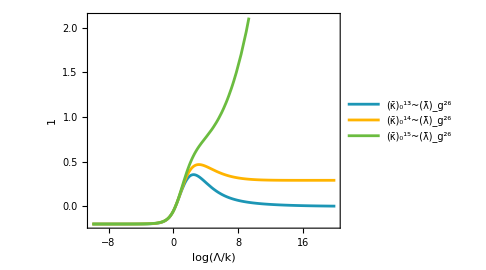

```mathematica
p1=Plot[{Interpolation[table1][t],Interpolation[table2][t],Interpolation[table3][t]},{t,-10,20},PlotLegends->Placed[{"(κ̄)_0^13~(λ̄)_g^26","(κ̄)_0^14~(λ̄)_g^26","(κ̄)_0^15~(λ̄)_g^26"},{Left,Top}],PlotStyle->{RGBColor["#1c96b5"],RGBColor["#ffb400"],RGBColor["#6bbc40"]},FrameLabel->{Log["Λ/k"],"1"},ImageSize->Medium,Frame->True,AxesStyle->Dashed,AspectRatio->3/4]
```

For the consequences of this analysis see again the main text and supplemental material.